```mathematica
Quit[]
```

```mathematica
SetOptions[EvaluationNotebook[],ShowGroupOpener->True];
```

## Loading ANATAR:

```mathematica
$QGrafPath="/home/pooja/WORK/Bonn/Project_3/Trial_Form/qgraf-3.6.5";
(*SetEnvironment["PATH"->"/usr/local/Wolfram/Mathematica/13.1/Executables:/home/pooja/.local/bin:/usr/local/sbin:/usr/local/bin:/usr/sbin:/usr/bin:/sbin:/bin:/usr/games:/usr/local/games:/snap/bin:/home/pooja/PROGRAMS/KIRA/bin:/home/pooja/PROGRAMS/ferl64/ferl64"]*)
SetEnvironment["PATH"->"/usr/local/Wolfram/Mathematica/13.1/Executables:/home/pooja/.local/bin:/usr/local/sbin:/usr/local/bin:/usr/sbin:/usr/bin:/sbin:/bin:/usr/games:/usr/local/games:/snap/bin:/home/pooja/Downloads:/home/pooja/PACKAGES_INSTALLED/ferl64"]
```

```mathematica
$AnatarPath="/home/pooja/WORK/Bonn/Project_3/ANATAR-main";
SetDirectory[$AnatarPath]
<<Anatar`;
```

/home/pooja/WORK/Bonn/Project_3/ANATAR-main

- ANATAR -

Version: 1.0.0, (28 Aug 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

## Loading MADGRAF:

```mathematica
$MadGrafDir="/home/pooja/PACKAGES_INSTALLED/MG5_aMC_v2_9_23";
Madgraf[process_String,model_String,dir_String, num_]:=
Block[{string1, string2},

SetDirectory[$MadGrafDir];

Export[dir<>".txt","
import "<>model<>"
generate "<>process<>"
output standalone "<>dir<>" 
"];

Run["
rm -r "<>dir<>"
./bin/mg5_aMC "<>dir<>".txt
cd "<>dir<>"/SubProcesses/P*
make
./check > log
exit
"];


string1=RunProcess[$SystemShell,"StandardOutput","
cd "<>dir<>"/SubProcesses/P*
cat log | tail -"<>ToString[3+num]<>" | head -n "<>ToString[num]<>" | awk '{$1=\"\"}1' | sed 's/^ *//' |  awk '{print \"{\"$0\"},\"}' |  awk '{for(i=1;i<NF;i++)if(i!=NF){$i=$i\",\"}  }1'
exit
"];
string2=RunProcess[$SystemShell,"StandardOutput","
cd "<>dir<>"/SubProcesses/P*
cat log | grep Matrix | awk '{print $4}'
exit
"];

"{"<>string1<>string2<>"}"//StringReplace[#,"E"->"*10^"]&//ToExpression
]
```

```mathematica
$MadGrafDir="/home/pooja/PACKAGES_INSTALLED/MG5_aMC_v2_9_23";
MadgrafwGauge[process_String,model_String,dir_String, num_,gauge_]:=
Block[{string1, string2},

SetDirectory[$MadGrafDir];
Export[dir<>".txt","
import "<>model<>"
set gauge "<>gauge<>"
generate "<>process<>"
output standalone "<>dir<>" 
"];

Run["
rm -r "<>dir<>"
./bin/mg5_aMC "<>dir<>".txt
cd "<>dir<>"/SubProcesses/P*
make
./check > log
exit
"];


string1=RunProcess[$SystemShell,"StandardOutput","
cd "<>dir<>"/SubProcesses/P*
cat log | tail -"<>ToString[3+num]<>" | head -n "<>ToString[num]<>" | awk '{$1=\"\"}1' | sed 's/^ *//' |  awk '{print \"{\"$0\"},\"}' |  awk '{for(i=1;i<NF;i++)if(i!=NF){$i=$i\",\"}  }1'
exit
"];
string2=RunProcess[$SystemShell,"StandardOutput","
cd "<>dir<>"/SubProcesses/P*
cat log | grep Matrix | awk '{print $4}'
exit
"];

"{"<>string1<>string2<>"}"//StringReplace[#,"E"->"*10^"]&//ToExpression
]
```

```mathematica
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
dot[p_,q_]:=p.eta.q
```

## Loading FORMCALC:

```mathematica
FormCalcPath="/home/pooja/PACKAGES_INSTALLED/FormCalc-9.10";
FeynArtsPath2="/home/pooja/PACKAGES_INSTALLED/FeynArts-3.12";
<<"/home/pooja/PACKAGES_INSTALLED/FeynArts-3.12/FeynArts.m"
Get[FormCalcPath<>"/FormCalc.m"]
```

FeynArts 3.12 (27 Mar 2025)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (16 Jan 2023)

by Thomas Hahn

```mathematica
LoadModel["SMQCD"];
```

loading classes model file /home/pooja/PACKAGES_INSTALLED/FeynArts-3.12/Models/SMQCD.mod

loading classes model file /home/pooja/PACKAGES_INSTALLED/FeynArts-3.12/Models/SM.mod

$CKM=False

### FromCalc Results:

```mathematica
$Debug=True;
```

```mathematica
ClearProcess[]
```

Excluding 0 Generic, 4 Classes, and 4 Particles fields

Excluding 2 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 4 Classes, and 4 Particles fields

Restoring 2 field point(s)

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

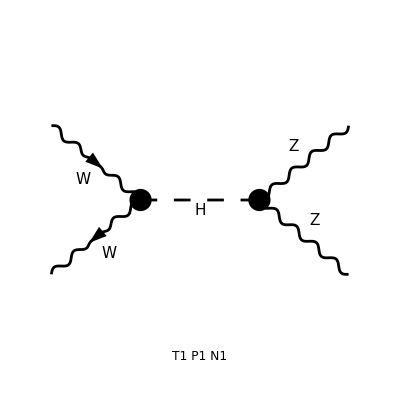

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-amp-9.frm

running FORM...

ok

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-pol-9.frm

running FORM...

ok

(Alfa2 π^2 (12 MW2^2-4 MW2 S+S^2) (12 MZ2^2-4 MZ2 S+S^2) Den[S,MH2]^2)/(CW2^2 MZ2^2 SW2^2)

```mathematica
Process={V[3],-V[3]}->{V[2],V[2]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},ExcludeParticles->{V[3],S[3]},ExcludeFieldPoints->{FieldPoint[V[3],-V[3],V[2],V[2]]}];
Paint[AA,SheetHeader->False,ImageSize->400];
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral,Dimension->D];
_Hel=0;
FormCalcResultwwzz=(PolarizationSum[res1,res1,Dimension->D]//.Subexpr[])//FullSimplify
```

Excluding 0 Generic, 2 Classes, and 2 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 2 Classes, and 2 Particles fields

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

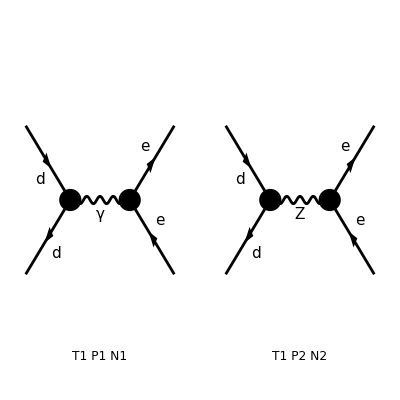

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-amp-9.frm

running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-hel-9.frm

running FORM...

ok

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-pol-9.frm

running FORM...

ok

1/(12 CW2^2 SW2^2)Alfa2 π^2 (-16 ME2 (2 MD2-S) SW2^2 (CW2 Den[S,0]+SW2 Den[S,MZ2]) (2 CW2 Den[S,0]+(-1+2 SW2) Den[S,MZ2])+4 SW2 (2 CW2 Den[S,0]+(-3+2 SW2) Den[S,MZ2]) (4 CW2 (MD2+ME2) S SW2 Den[S,0]+(3 ME2 (-2 MD2+S)+8 ME2 (MD2-S) SW2+4 (MD2+ME2) S SW2^2) Den[S,MZ2])-4 MD2 SW2 (4 CW2 SW2 Den[S,0]+(3+4 (-2+SW2) SW2) Den[S,MZ2]) (-2 CW2 (2 ME2+S) Den[S,0]+(S-2 (ME2+2 ME2 SW2+S SW2)) Den[S,MZ2])+4 SW2^2 (MD2+ME2-T)^2 ((2 CW2 Den[S,0]+(-3+2 SW2) Den[S,MZ2])^2+(2 CW2 Den[S,0]+(-1+2 SW2) Den[S,MZ2])^2)+(MD2+ME2-U)^2 (16 SW2^2 (CW2 Den[S,0]+SW2 Den[S,MZ2])^2+(4 CW2 SW2 Den[S,0]+(3+4 (-2+SW2) SW2) Den[S,MZ2])^2))

```mathematica
ClearProcess[]
Process={F[4,{1}],-F[4,{1}]}->{F[2,{1}],-F[2,{1}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},ExcludeParticles->{S[1],S[2]}(*,ExcludeFieldPoints->{FieldPoint[V[3],-V[3],V[2],V[2]]}*)];
Paint[AA,SheetHeader->False,ImageSize->400];
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral,Dimension->D];
_Hel=0;
FormCalcResultddee=(PolarizationSum[res1,res1,Dimension->D]//.Subexpr[])//FullSimplify
```

```mathematica
ClearProcess[]
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 1 Particles insertion

> Top. 25: 1 Particles insertion

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 2 Particles insertions

> Top. 1 afbg/chdhef/fggh.m, 0 diagrams

> Top. 2 afbg/chdheg/fgfh.m, 0 diagrams

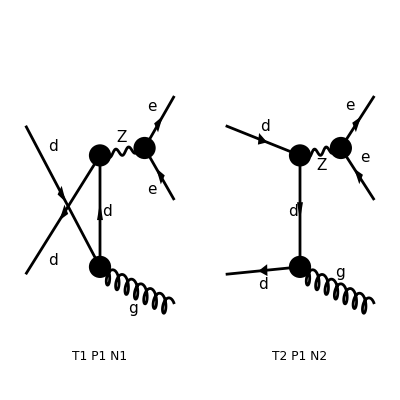

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-amp-11.frm

running FORM...

ok

Amp[{{F[4,{1,Col1}],k[1],MD,{-Charge/3,(2 ColorCharge)/(√3)}},{-F[4,{1,Col2}],k[2],MD,{Charge/3,-(2 ColorCharge)/(√3)}}}→{{F[2,{1}],k[3],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[4],ME,{Charge,-LeptonNumber}},{V[5,{Glu5}],k[5],0,{√3 ColorCharge}}}][(Alfa GS MD π Sub1 (1-2 SW2) Den[S34,MZ2] (1/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-1/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F1 SUN1])/CW2+(2 Alfa GS π (3-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F10 SUN1])/(3 CW2)+(2 Alfa GS π (1-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F11 SUN1])/(3 CW2)+(4 Alfa GS ME π Den[S34,MZ2] Den[3 MD2+2 ME2-S-T24-U,MD2] Mat[F12 SUN1])/(3 CW2)+(2 Alfa GS π (3-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F13 SUN1])/(3 CW2)-(Alfa GS π (1-2 SW2) (3-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F14 SUN1])/(3 CW2 SW2)+(Alfa GS MD π Sub1 (1-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F15 SUN1])/(3 CW2)+(2 Alfa GS π (1-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F16 SUN1])/(3 CW2)-(8 Alfa GS π SW2 Den[S34,MZ2] Den[3 MD2+2 ME2-S-T24-U,MD2] Mat[F17 SUN1])/(3 CW2)-(Alfa GS π (1-2 SW2) Den[S34,MZ2] (2/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-2/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F18 SUN1])/CW2-(4 Alfa GS π SW2 Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F19 SUN1])/(3 CW2)-(Alfa GS MD π Den[S34,MZ2] (2 Den[3 MD2+2 ME2-S-T-T14,MD2]-2 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F2 SUN1])/CW2+(2 Alfa GS π (1-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F20 SUN1])/(3 CW2)+(Alfa GS π SW2 Den[S34,MZ2] (4/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-4/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F21 SUN1])/CW2-(Alfa GS π (1-2 SW2) (3-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F22 SUN1])/(3 CW2 SW2)-(Alfa GS π (1-2 SW2) (3-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F23 SUN1])/(3 CW2 SW2)-(Alfa GS π (1-2 SW2) Den[S34,MZ2] (2/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-2/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F24 SUN1])/CW2+(2 Alfa GS ME π Sub2 (3-2 SW2) Den[S34,MZ2] Den[3 MD2+2 ME2-S-T24-U,MD2] Mat[F25 SUN1])/(3 CW2)-(4 Alfa GS ME π Den[S34,MZ2] Den[3 MD2+2 ME2-S-T24-U,MD2] Mat[F26 SUN1])/(3 CW2)-(Alfa GS (Pair1+Pair2) π SW2 Den[S34,MZ2] (4/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-4/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F27 SUN1])/CW2-(Alfa GS MD π Sub1 (1-2 SW2) Den[S34,MZ2] (1/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-1/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F28 SUN1])/CW2-(2 Alfa GS π (1-2 SW2) (3-2 SW2) Den[S34,MZ2] Den[3 MD2+2 ME2-S-T24-U,MD2] Mat[F29 SUN1])/(3 CW2 SW2)-(4 Alfa GS π SW2 Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F3 SUN1])/(3 CW2)+(Alfa GS MD π Den[S34,MZ2] (2 Den[3 MD2+2 ME2-S-T-T14,MD2]-2 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F30 SUN1])/CW2+(2 Alfa GS π (3-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F31 SUN1])/(3 CW2)+(Alfa GS π SW2 Den[S34,MZ2] (4/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-4/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F32 SUN1])/CW2+(4 Alfa GS π (3-2 SW2) Den[S34,MZ2] Den[3 MD2+2 ME2-S-T24-U,MD2] Mat[F33 SUN1])/(3 CW2)+(Alfa GS (Pair1+Pair2) π (1-2 SW2) Den[S34,MZ2] (2/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-2/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F34 SUN1])/CW2+(2 Alfa GS π (3-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F35 SUN1])/(3 CW2)+(Alfa GS π (1-2 SW2) (3-2 SW2) Den[S34,MZ2] (1/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-1/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F36 SUN1])/(CW2 SW2)-(Alfa GS π (3-2 SW2) Den[S34,MZ2] (2/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-2/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F37 SUN1])/CW2-(Alfa GS π (3-2 SW2) Den[S34,MZ2] (2/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-2/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F38 SUN1])/CW2+(Alfa GS π (1-2 SW2) (3-2 SW2) Den[S34,MZ2] (1/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-1/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F39 SUN1])/(CW2 SW2)+(2 Alfa GS MD π Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F4 SUN1])/CW2-(Alfa GS π (1-2 SW2) (3-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F40 SUN1])/(3 CW2 SW2)-(2 Alfa GS ME π Sub2 (3-2 SW2) Den[S34,MZ2] Den[3 MD2+2 ME2-S-T24-U,MD2] Mat[F41 SUN1])/(3 CW2)-(4 Alfa GS π SW2 Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F42 SUN1])/(3 CW2)+(Alfa GS (Pair1+Pair2) π (3-2 SW2) Den[S34,MZ2] (2/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-2/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F43 SUN1])/CW2-(Alfa GS (Pair1+Pair2) π (1-2 SW2) (3-2 SW2) Den[S34,MZ2] (1/3 Den[3 MD2+2 ME2-S-T-T14,MD2]-1/3 Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F44 SUN1])/(CW2 SW2)-(4 Alfa GS π (1-2 SW2) Den[S34,MZ2] Den[3 MD2+2 ME2-S-T-T14,MD2] Mat[F45 SUN1])/(3 CW2)+(8 Alfa GS π SW2 Den[S34,MZ2] Den[3 MD2+2 ME2-S-T-T14,MD2] Mat[F46 SUN1])/(3 CW2)+(2 Alfa GS π (1-2 SW2) (3-2 SW2) Den[S34,MZ2] Den[3 MD2+2 ME2-S-T-T14,MD2] Mat[F47 SUN1])/(3 CW2 SW2)-(4 Alfa GS π (3-2 SW2) Den[S34,MZ2] Den[3 MD2+2 ME2-S-T-T14,MD2] Mat[F48 SUN1])/(3 CW2)-(4 Alfa GS π SW2 Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F5 SUN1])/(3 CW2)-(2 Alfa GS MD π Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F6 SUN1])/CW2+(2 Alfa GS π (1-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F7 SUN1])/(3 CW2)+(4 Alfa GS π (1-2 SW2) Den[S34,MZ2] Den[3 MD2+2 ME2-S-T24-U,MD2] Mat[F8 SUN1])/(3 CW2)-(Alfa GS MD π Sub1 (1-2 SW2) Den[S34,MZ2] (Den[3 MD2+2 ME2-S-T-T14,MD2]+Den[3 MD2+2 ME2-S-T24-U,MD2]) Mat[F9 SUN1])/(3 CW2)]

> 2304 helicity matrix elements

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-hel-11.frm

running FORM...

ok

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-pol-11.frm

running FORM...

ok

```mathematica
Process={F[4,{1}],-F[4,{1}]}->{F[2,{1}],-F[2,{1}],V[5]};
top=CreateTopologies[0,2-> 3];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},ExcludeParticles->{S[1],S[2],V[1]}(*,ExcludeFieldPoints->{FieldPoint[V[3],-V[3],V[2],V[2]]}*),Model->"SMQCD"];
Paint[AA,SheetHeader->False,ImageSize->400];
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral,Dimension->D]
_Hel=0;
FormCalcResultddeeG=(PolarizationSum[res1,res1,Dimension->D]//.Subexpr[])
```

```mathematica
Variables[FormCalcResultddeeG]
```

{Abb652,Abb654,Abb655,Abb656,Abb657,Abb659,Abb660,Abb662,Abb666,Abb667,Abb668,Abb671,Abb672,Abb674,Abb675,Abb676,Abb677,Abb678,Abb679,Abb682,Abb683,Abb685,Abb688,Abb691,Abb694,Abb695,Abb696,Abb698,Abb699,Abb700,Abb701,Abb704,Abb705,Abb706,Abb707,Abb710,Abb711,Abb712,Abb715,Abb716,Abb719,Abb721,Abb722,Abb724,Abb725,Abb730,Abb733,Abb734,Abb735,Abb737,Abb738,Abb739,Abb740,Abb741,Abb742,Abb743,Abb746,Abb747,Abb748,Abb749,Abb752,Abb753,Abb754,Abb755,Abb756,Abb759,Abb760,Abb761,Abb762,Abb763,Abb764,Abb765,Abb766,Abb768,Abb770,Abb771,Abb772,Abb773,Abb774,Abb775,Abb776,Abb777,Abb778,Abb779,Abb781,Abb782,Abb783,Abb784,Abb785,Abb787,Abb788,Abb789,Abb791,Abb792,Abb793,Abb794,Abb795,Abb796,Abb798,Abb800,Abb802,Abb803,Abb804,Abb806,Alfa2,Alfas,CW2,MD2,ME2,S,S34,SW2,T,T14,T24,U,Den[S34,MZ2],Den[3 MD2+2 ME2-S-T-T14,MD2],Den[3 MD2+2 ME2-S-T24-U,MD2]}

```mathematica
FullSimplify[FormCalcResultddeeG/.Den[a_,b_]:>1/(a^2-b^2)/.MD2->0/.ME2->0,Assumptions->CW2+SW2==1]
```

$Aborted

```mathematica
ClearProcess[]
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

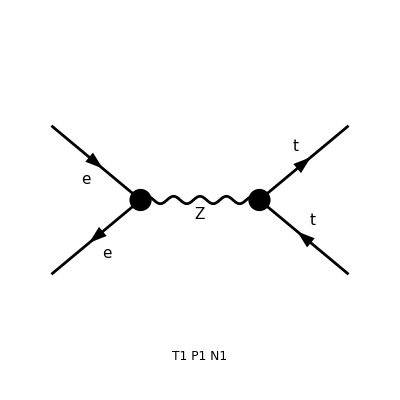

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-amp-11.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[3,{3,Col3}],k[3],MT,{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-F[3,{3,Col4}],k[4],MT,{-(2 Charge)/3,-(2 ColorCharge)/(√3)}}}][-(2 Alfa π (3-4 SW2) Den[S,MZ2] Mat[F1 SUN1])/(3 CW2)+(8 Alfa π SW2 Den[S,MZ2] Mat[F2 SUN1])/(3 CW2)+(Alfa π (3-4 SW2) (1-2 SW2) Den[S,MZ2] Mat[F3 SUN1])/(3 CW2 SW2)-(4 Alfa π (1-2 SW2) Den[S,MZ2] Mat[F4 SUN1])/(3 CW2)]

> 16 helicity matrix elements

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-hel-11.frm

running FORM...

ok

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-pol-11.frm

running FORM...

ok

1/(12 CW2^2 SW2^2)Alfa2 π^2 (-4 ME2 (2 MT2-S) (3-4 SW2)^2 SW2 (-1+2 SW2)+8 MT2 SW2 (-3+4 SW2) (-2 ME2+S-4 (2 ME2+S) SW2+8 (2 ME2+S) SW2^2)+4 SW2^2 (13+8 SW2 (-5+4 SW2)) (ME2+MT2-T)^2+64 SW2^3 (ME2 (2 MT2-S) (1-2 SW2)+SW2 (ME2+MT2-U)^2)+(3+2 SW2 (-5+4 SW2))^2 (ME2+MT2-U)^2) Den[S,MZ2]^2

```mathematica
Process={F[2,{1}],-F[2,{1}]}->{F[3,{3}],-F[3,{3}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},ExcludeParticles->{S[1],S[2],V[1]}(*,ExcludeFieldPoints->{FieldPoint[V[3],-V[3],V[2],V[2]]}*),Model->"SMQCD"];
Paint[AA,SheetHeader->False,ImageSize->400];
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral,Dimension->D]
_Hel=0;
FormCalcResulteett=(PolarizationSum[res1,res1,Dimension->D]//.Subexpr[])//FullSimplify
```

```mathematica
ClearProcess[]
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

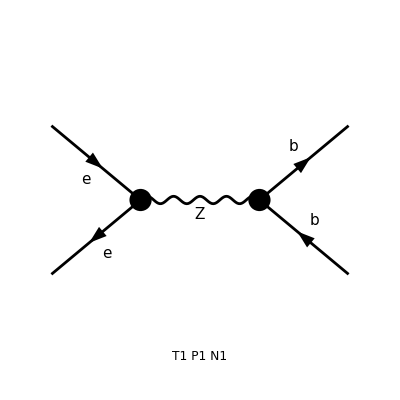

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-amp-11.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[4,{3,Col3}],k[3],MB,{-Charge/3,(2 ColorCharge)/(√3)}},{-F[4,{3,Col4}],k[4],MB,{Charge/3,-(2 ColorCharge)/(√3)}}}][-(Alfa π (1-2 SW2) (3-2 SW2) Den[S,MZ2] Mat[F1 SUN1])/(3 CW2 SW2)+(2 Alfa π (1-2 SW2) Den[S,MZ2] Mat[F2 SUN1])/(3 CW2)-(4 Alfa π SW2 Den[S,MZ2] Mat[F3 SUN1])/(3 CW2)+(2 Alfa π (3-2 SW2) Den[S,MZ2] Mat[F4 SUN1])/(3 CW2)]

> 16 helicity matrix elements

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-hel-11.frm

running FORM...

ok

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-pol-11.frm

running FORM...

ok

1/(12 CW2^2)Alfa2 π^2 (-(4 MB2 (2 ME2-S) (1-2 SW2)^2 (-3+2 SW2))/SW2+(4 ME2 (-1+2 SW2) (2 MB2 (-9+4 SW2 (-3+2 SW2))+S (9+4 SW2 (-3+2 SW2))))/SW2+8 (5+4 (-2+SW2) SW2) (MB2+ME2-T)^2+16 SW2 (MB2 (2 ME2-S) (3-2 SW2)+SW2 (MB2+ME2-U)^2)+((3+4 (-2+SW2) SW2)^2 (MB2+ME2-U)^2)/SW2^2) Den[S,MZ2]^2

```mathematica
Process={F[2,{1}],-F[2,{1}]}->{F[4,{3}],-F[4,{3}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},ExcludeParticles->{S[1],S[2],V[1]}(*,ExcludeFieldPoints->{FieldPoint[V[3],-V[3],V[2],V[2]]}*),Model->"SMQCD"];
Paint[AA,SheetHeader->False,ImageSize->400];
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral,Dimension->D]
_Hel=0;
FormCalcResulteebb=(PolarizationSum[res1,res1,Dimension->D]//.Subexpr[])//FullSimplify
```

```mathematica
ClearProcess[]
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 3 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

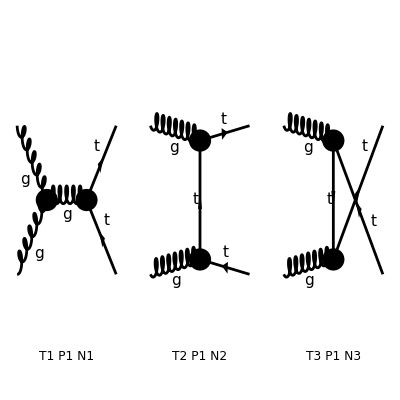

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-amp-11.frm

running FORM...

ok

Amp[{{V[5,{Glu1}],k[1],0,{√3 ColorCharge}},{V[5,{Glu2}],k[2],0,{√3 ColorCharge}}}→{{F[3,{3,Col3}],k[3],MT,{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-F[3,{3,Col4}],k[4],MT,{-(2 Charge)/3,-(2 ColorCharge)/(√3)}}}][-Alfas Pair2 π (8 Den[S,0]+4 Den[T,MT2]) Mat[F1 SUN1]+8 Alfas π (Pair4 Den[S,0]+Pair3 Den[T,MT2]) Mat[F2 SUN1]+Alfas Pair1 π (8 Den[S,0]+4 Den[T,MT2]) Mat[F3 SUN1]+Alfas Pair1 π (8 Den[S,0]+4 Den[T,MT2]) Mat[F4 SUN1]+8 Alfas π (Pair4 Den[S,0]+Pair3 Den[T,MT2]) Mat[F5 SUN1]+4 Alfas π Den[T,MT2] Mat[F6 SUN1]-Alfas Pair2 π (8 Den[S,0]+4 Den[T,MT2]) Mat[F7 SUN1]+4 Alfas π Den[T,MT2] Mat[F8 SUN1]+Alfas Pair2 π (8 Den[S,0]+4 Den[U,MT2]) Mat[F1 SUN2]-8 Alfas π (Pair4 Den[S,0]+Pair5 Den[U,MT2]) Mat[F2 SUN2]-Alfas Pair1 π (8 Den[S,0]+4 Den[U,MT2]) Mat[F3 SUN2]-Alfas Pair1 π (8 Den[S,0]+4 Den[U,MT2]) Mat[F4 SUN2]-8 Alfas π (Pair4 Den[S,0]+Pair5 Den[U,MT2]) Mat[F5 SUN2]+4 Alfas π Den[U,MT2] Mat[F6 SUN2]+Alfas Pair2 π (8 Den[S,0]+4 Den[U,MT2]) Mat[F7 SUN2]+4 Alfas π Den[U,MT2] Mat[F8 SUN2]]

> 64 helicity matrix elements

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-hel-11.frm

running FORM...

ok

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-pol-11.frm

running FORM...

ok

-16/3 Alfas2 π^2 (144 (Abb73-Abb132 MT2-Abb57 S) Den[S,0]^2+9 (2 Abb115-8 Abb65 S+Abb82 (MT2-T)+MT2 (Abb85+8 Abb216 MT2+8 Abb136 S-4 Abb186 S-Abb152 T+4 Abb169 T)-(Abb85-Abb152 MT2+4 Abb199 MT2) U) Den[S,0] Den[T,MT2]+4 (-4 Abb112+Abb103 MT2-16 Abb56 MT2-32 Abb67 MT2+8 Abb71 MT2-4 Abb163 MT2^2-2 Abb191 MT2^2+4 Abb221 MT2^2-2 Abb76 MT2^2+4 Abb56 S+16 Abb67 S+16 Abb150 MT2 S-4 Abb198 MT2 S-Abb103 T+8 Abb56 T+Abb80 T+4 Abb163 MT2 T-4 Abb174 MT2 T+Abb188 MT2 T+2 Abb76 MT2 T+2 Abb201 MT2^2 T-(Abb80+MT2 (Abb188+4 Abb189-2 (Abb191+Abb76-Abb201 MT2))+2 Abb76 T) U+2 Abb102 (-MT2+U)) Den[T,MT2]^2+(2 Den[S,0]+Den[T,MT2]) (9 (2 Abb98+Abb59 (-MT2+S+U)+Abb66 (-T+U)+MT2 (4 Abb142 MT2-4 Abb135 S-4 Abb142 T+Abb157 T-(4 Abb142+Abb157) U)) Den[S,0]+8 (2 Abb95+Abb70 MT2+Abb137 MT2^2+2 Abb214 MT2^2-Abb70 S-Abb137 MT2 S+2 Abb173 MT2 S+Abb75 T-2 Abb148 MT2 T-Abb156 MT2 T+2 Abb187 MT2 T-Abb201 MT2^2 T+2 Abb61 (-MT2+T)-(Abb70+Abb75-MT2 (-Abb137+2 Abb148+Abb156-2 Abb167+Abb201 MT2)) U+2 Abb62 (-MT2+U)) Den[T,MT2])+(9 (-2 Abb194+8 Abb108 S+Abb82 (-MT2+T)+MT2 (-Abb85+8 Abb216 MT2+8 Abb136 S-4 Abb195 S+Abb152 T-4 Abb200 T)+(Abb85-Abb152 MT2+4 Abb179 MT2) U) Den[S,0]+(-2 Abb196+8 Abb122 MT2+Abb138 MT2+Abb149 MT2+16 Abb56 MT2+Abb210 MT2^2+Abb212 MT2^2-8 Abb220 MT2^2+2 Abb76 MT2^2-4 Abb56 S-8 Abb146 MT2 S+2 Abb226 MT2 S+8 Abb117 (-2 MT2+S)-Abb138 T-8 Abb56 T-Abb80 T-Abb188 MT2 T-Abb212 MT2 T+2 Abb225 MT2 T-2 Abb76 MT2 T+(-Abb149+Abb80+(Abb188-Abb210+2 Abb218-2 Abb76) MT2+2 Abb76 T) U) Den[T,MT2]-(2 Abb128+Abb119 T+2 Abb61 (-MT2+T)-MT2 (2 Abb62+Abb137 MT2+2 Abb203 MT2-Abb137 S+2 Abb207 S+2 (Abb148+Abb181-Abb197) T-Abb201 MT2 T)+(-Abb119+2 Abb62+MT2 (Abb137+2 (Abb148+Abb181-Abb217)-Abb201 MT2)) U+Abb113 (-MT2+S+U)) (2 Den[S,0]+Den[T,MT2])) Den[U,MT2]+4 (4 Abb183+8 Abb129 MT2-2 Abb165 MT2-Abb176 MT2-16 Abb56 MT2-2 Abb208 MT2^2+4 Abb215 MT2^2-4 Abb223 MT2^2-2 Abb76 MT2^2+4 Abb56 S+16 Abb211 MT2 S-4 Abb224 MT2 S+16 Abb125 (-2 MT2+S)+Abb176 T+8 Abb56 T+Abb80 T+Abb188 MT2 T+2 Abb208 MT2 T-4 Abb219 MT2 T+2 Abb76 MT2 T-2 Abb201 MT2^2 T+(2 Abb165-Abb80-Abb188 MT2+2 MT2 (-2 Abb209+2 Abb223+Abb76+Abb201 MT2)-2 Abb76 T) U) Den[U,MT2]^2+(2 Den[S,0]+Den[U,MT2]) ((8 Abb64+18 Abb98-8 Abb147 MT2-8 Abb56 S+MT2 (-36 Abb135 S+36 Abb142 (MT2-T)+2 Abb137 T+9 Abb157 T+4 Abb60 (-MT2+T))-(9 Abb66-2 Abb70) (T-U)-((2 Abb137+36 Abb142+9 Abb157-4 Abb60) MT2+4 Abb60 T) U+Abb59 (-11 MT2+9 S+2 T+9 U)) Den[S,0]+(4 Abb64+2 Abb95-4 Abb147 MT2-Abb59 MT2-2 Abb61 MT2-2 Abb62 MT2+Abb70 MT2+Abb137 MT2^2+2 Abb214 MT2^2-2 Abb60 MT2^2-4 Abb56 S-Abb70 S-Abb137 MT2 S+2 Abb173 MT2 S+Abb59 T+2 Abb61 T+Abb70 T+Abb75 T+Abb137 MT2 T-2 Abb148 MT2 T-Abb156 MT2 T+2 Abb187 MT2 T+2 Abb60 MT2 T-Abb201 MT2^2 T+(2 Abb62-2 Abb70-Abb75-2 Abb137 MT2+MT2 (2 Abb148+Abb156-2 Abb167+2 Abb60+Abb201 MT2)-2 Abb60 T) U) Den[T,MT2]-8 (2 Abb128+Abb119 T+2 Abb61 (-MT2+T)-MT2 (2 Abb62+Abb137 MT2+2 Abb203 MT2-Abb137 S+2 Abb207 S+2 (Abb148+Abb181-Abb197) T-Abb201 MT2 T)+(-Abb119+2 Abb62+MT2 (Abb137+2 (Abb148+Abb181-Abb217)-Abb201 MT2)) U+Abb113 (-MT2+S+U)) Den[U,MT2])+4 (4 Abb64-4 Abb147 MT2-Abb59 MT2-2 Abb60 MT2^2-4 Abb56 S+Abb59 T+Abb70 T+Abb137 MT2 T+2 Abb60 MT2 T-(Abb70+Abb137 MT2-2 Abb60 MT2+2 Abb60 T) U) (8 Den[S,0]^2+Den[T,MT2]^2+Den[U,MT2]^2+4 Den[S,0] (Den[T,MT2]+Den[U,MT2])))

```mathematica
Process={V[5],V[5]}->{F[3,{3}],-F[3,{3}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},ExcludeParticles->{S[1],S[2],V[1]}(*,ExcludeFieldPoints->{FieldPoint[V[3],-V[3],V[2],V[2]]}*),Model->"SMQCD"];
Paint[AA,SheetHeader->False,ImageSize->400];
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral,Dimension->D]
_Hel=0;
FormCalcResultggtt=(PolarizationSum[res1,res1,Dimension->D]//.Subexpr[])//FullSimplify
```

```mathematica
ClearProcess[]
```

Excluding 0 Generic, 2 Classes, and 2 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

> Top. 3: 3 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 2 Classes, and 2 Particles fields

in total: 6 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

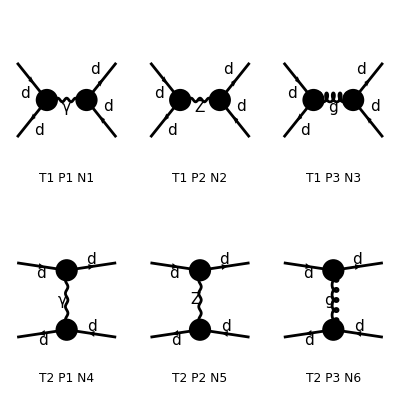

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 3 Particles amplitudes

in total: 6 Particles amplitudes

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-amp-11.frm

running FORM...

ok

> 36 helicity matrix elements

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-hel-11.frm

running FORM...

ok

preparing FORM code in /home/pooja/PACKAGES_INSTALLED/FeynCalc/fc-pol-11.frm

running FORM...

ok

1/(108 CW2^2 SW2^2)π^2 (96 (Alfa2+18 Alfas2) CW2^2 SW2^2 (8 MD2^2+T^2+4 MD2 (S-T-U)+U^2) Den[S,0]^2+3 Alfa2 (4 MD2^2 (81+4 SW2 (-3+2 SW2) (9+4 SW2 (-3+2 SW2)))+8 MD2 SW2 (-3+2 SW2) (S (9+4 SW2 (-3+2 SW2))+4 (3-2 SW2) SW2 T)-4 MD2 (81+8 SW2 (-3+2 SW2) (9+SW2 (-3+2 SW2))) U+81 U^2+8 SW2 (-3+2 SW2) (9 U^2+SW2 (-3+2 SW2) (T^2+U^2))) Den[S,MZ2]^2+8 CW2 SW2 Den[S,0] (3 Alfa2 (4 MD2^2 (3-4 SW2)^2+9 U^2+4 SW2 (-3+2 SW2) (T^2+U^2)+2 MD2 (S (3-4 SW2)^2-18 U-8 SW2 (-3+2 SW2) (T+U))) Den[S,MZ2]+8 (Alfa2+24 Alfa Alfas-18 Alfas2) CW2 SW2 (2 MD2 (2 MD2+S+T)-6 MD2 U+U^2) Den[T,0]+(Alfa2+12 Alfa Alfas) (2 MD2 (2 MD2+S) (9+4 SW2 (-3+2 SW2))+8 MD2 SW2 (-3+2 SW2) T-12 MD2 (3-6 SW2+4 SW2^2) U+(9+4 SW2 (-3+2 SW2)) U^2) Den[T,MZ2])+2 Den[S,MZ2] (4 (Alfa2+12 Alfa Alfas) CW2 SW2 (4 MD2^2 (9+4 SW2 (-3+2 SW2))+2 MD2 (4 SW2 (-3+2 SW2) (S+T-3 U)+9 (T-2 U))+(9+4 SW2 (-3+2 SW2)) U^2) Den[T,0]+Alfa2 (4 MD2^2 (81+4 SW2 (-3+2 SW2) (9-6 SW2+4 SW2^2))+(81+8 SW2 (-3+2 SW2) (9+SW2 (-3+2 SW2))) U^2+4 MD2 (-81 U+SW2 (-3+2 SW2) ((9+4 SW2 (-3+2 SW2)) (S+T)-12 (6+SW2 (-3+2 SW2)) U))) Den[T,MZ2])+3 (32 (Alfa2+18 Alfas2) CW2^2 SW2^2 (8 MD2^2+S^2+U^2-4 MD2 (S-T+U)) Den[T,0]^2+8 Alfa2 CW2 SW2 (4 MD2^2 (3-4 SW2)^2+18 MD2 (T-2 U)+9 U^2-16 MD2 SW2 (-3+2 SW2) (S-T+U)+4 SW2 (-3+2 SW2) (S^2+U^2)) Den[T,0] Den[T,MZ2]+Alfa2 (8 S^2 (3-2 SW2)^2 SW2^2+4 MD2^2 (81+4 SW2 (-3+2 SW2) (9+4 SW2 (-3+2 SW2)))+(81+8 SW2 (-3+2 SW2) (9+SW2 (-3+2 SW2))) U^2-4 MD2 (81 U+2 SW2 (-3+2 SW2) (-9 (T-4 U)+4 SW2 (-3+2 SW2) (S-T+U)))) Den[T,MZ2]^2))

```mathematica
Process={F[4,{1}],-F[4,{1}]}->{F[4,{1}],-F[4,{1}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},ExcludeParticles->{S[1],S[2]}(*,ExcludeFieldPoints->{FieldPoint[V[3],-V[3],V[2],V[2]]}*),Model->"SMQCD"];
Paint[AA,SheetHeader->False,ImageSize->400];
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral,Dimension->D];
_Hel=0;
FormCalcResultdddd=(PolarizationSum[res1,res1,Dimension->D]//.Subexpr[])//FullSimplify
```

## Checks with MADGRAPH

```mathematica
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,CA:> 3, CF:> 4/3};
```

## Process 1: b g > h b

```mathematica
Amp1=GenerateAmplitude[{b,G}->{H,b},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,1,1}},RemovePropagator->{{Z,0,0},{u,0,0},{d,0,0},{s,0,0},{c,0,0}},Dimension->4,RecycleAmplitude->False]
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bG_Hb.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bG_Hb/bG_Hb_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {b, G} -> {H, b}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{b[p1],G[p2]}→{H[p3],b[p4]}},Total→{1;;2},Name→bG_Hb,LoopOrder→0,Kinematics→{p1^2→MB^2,p1.p1→MB^2,1/(p1.p1)→1/MB^2,p2^2→0,p2.p2→0,p3^2→MH^2,p3.p3→MH^2,1/(p3.p3)→1/MH^2,p4^2→MB^2,p4.p4→MB^2,1/(p4.p4)→1/MB^2,p1.p2→1/2 (-MB^2+S),p1.p3→1/2 (MB^2+MH^2-T),p2.p3→1/2 (MH^2-U),1/(p1.p2)→2/(-MB^2+S),1/(p1.p3)→2/(MB^2+MH^2-T),1/(p2.p3)→2/(MH^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID[1]→-ⅈ GC10 GC42 MB Den[p1+p2,MB] GammaM[1,iSpin1,iSpin2] GammaM[1,Spin4,iSpin1] GammaM[Lor3,iSpin2,Spin1] PolV[-3,Lor3,p2,0,Gluon3] SpinorU[-1,p1,MB,Spin1,Colour1] SpinorUbar[-4,p4,MB,Spin4,iColour2] T[iColour2,Colour1,Gluon3]-ⅈ GC10 GC42 Den[p1+p2,MB] GammaM[1,Spin4,iSpin1] GammaM[Lor3,iSpin2,Spin1] GammaM[p1+p2,iSpin1,iSpin2] PolV[-3,Lor3,p2,0,Gluon3] SpinorU[-1,p1,MB,Spin1,Colour1] SpinorUbar[-4,p4,MB,Spin4,iColour2] T[iColour2,Colour1,Gluon3],DiagramID[2]→-ⅈ GC10 GC42 MB Den[p1-p3,MB] GammaM[1,iSpin1,iSpin2] GammaM[1,iSpin2,Spin1] GammaM[Lor3,Spin4,iSpin1] PolV[-3,Lor3,p2,0,Gluon3] SpinorU[-1,p1,MB,Spin1,iColour2] SpinorUbar[-4,p4,MB,Spin4,Colour4] T[Colour4,iColour2,Gluon3]-ⅈ GC10 GC42 Den[p1-p3,MB] GammaM[1,iSpin2,Spin1] GammaM[Lor3,Spin4,iSpin1] GammaM[p1-p3,iSpin1,iSpin2] PolV[-3,Lor3,p2,0,Gluon3] SpinorU[-1,p1,MB,Spin1,iColour2] SpinorUbar[-4,p4,MB,Spin4,Colour4] T[Colour4,iColour2,Gluon3]}|>

```mathematica
AmpC1=GenerateAmplitudeConjugate[{b,G}->{H,b},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,1,1}},RemovePropagator->{{Z,0,0},{u,0,0},{d,0,0},{s,0,0},{c,0,0}},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bG_Hb.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bG_Hb/bG_Hb_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {b, G} -> {H, b}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq1 = GenerateAmplitudeSquare[Amp1,AmpC1,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq1[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→MB^2+2 p1.p2,T→MB^2+MH^2-2 p1.p3,U→MH^2-2 p2.p3}}

```mathematica
resultAnatar1=Collect[AmpSq1[Amplitudes]/.{Den[p1+p2,MB]:>1/(S-MB^2),Den[p1-p3,MB]-> 1/(T-MB^2),U:>2 MB^2+MH^2-T-S,1/U->1/(2 MB^2+MH^2-T-S)},{gs,I2R,vev,ymdo}]//FullSimplify
AmpSq1[Kinematics];
```

-(4 CF gs^2 MB^2 Nc (20 MB^8-4 MB^6 (3 MH^2+4 (S+T))+MB^4 (2 MH^4+5 S^2-2 S T+5 T^2+10 MH^2 (S+T))-MB^2 (4 MH^2 S T+2 MH^4 (S+T)+(S-T)^2 (S+T))+S T (2 MH^4-2 MH^2 (S+T)+(S+T)^2)))/((MB^2-S)^2 (MB^2-T)^2 vev^2)

```mathematica
ResultMad=Madgraf["b g > h b","sm","bghb",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,CA->3,CF->4/3,Nc->3,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=Thread[%%->%]
```

{{500.011,0.,0.,499.989,4.7},{499.989,0.,0.,-499.989,0.},{507.802,38.9343,262.367,414.59,125.},{492.198,-38.9343,-262.367,-414.59,4.7},0.000954539}

{{500.011,0.,0.,499.989,4.7},{499.989,0.,0.,-499.989,0.},{507.802,38.9343,262.367,414.59,125.},{492.198,-38.9343,-262.367,-414.59,4.7}}

{S,T,U}

{999978.+MB^2,-93231.8+MB^2+MH^2,-922371.+MH^2}

{S→999978.+MB^2,T→-93231.8+MB^2+MH^2,U→-922371.+MH^2}

```mathematica
(resultAnatar1/2/2/3/8)/.STUNum/.MomSubs/.ParamSubs//FullSimplify
ANAvsMAD=SetPrecision[1-((%)/ResultMad[[5]]),10]
```

0.00095454

-1.430205585×10^-7

## Process 2: d d~ > t t~(via A,G)

```mathematica
Amp2=GenerateAmplitude[{d,dbar}->{t,tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,0,2}},RemovePropagator->{Z,u,b,s,c},Dimension->4,Gauges->{"QCD"->"Feynman","EW"->"Unitary"}];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ddbar_ttbar/ddbar_ttbar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {d, dbar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC2=GenerateAmplitudeConjugate[{d,dbar}->{t,tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,0,2}},RemovePropagator->{Z,u,b,s,c},Dimension->4,Gauges->{"QCD"->"Feynman","EW"->"Unitary"}];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ddbar_ttbar/ddbar_ttbar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {d, dbar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq2 = GenerateAmplitudeSquare[Amp2,AmpC2,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq2[Kinematics];
relevantRules=Select[AmpSq2[Kinematics],!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;3]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→MT^2-2 p1.p3,U→MT^2-2 p2.p3}}

```mathematica
resultAnatar2=Collect[AmpSq2[Amplitudes]/.{Den[a_,b_]:>1/(S)}/.AN$Kinematics/.STURules,{gs,I2R,vev,ymdo}]//FullSimplify;
```

```mathematica
ResultMad=Madgraf["d d~ > t t~ /a","sm","ddtt",4]
ps=ResultMad[[1;;4]]
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,313.105,179.052,-299.961,173.},{500.,-313.105,-179.052,299.961,173.},0.722973}

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,313.105,179.052,-299.961,173.},{500.,-313.105,-179.052,299.961,173.}}

```mathematica
(resultAnatar2/(2^2*3^2))/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs/.ParamSubs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

{0.000657155}

{0.999091}

## Process 4: u u~ > u u~(via A,Z,G)

```mathematica
Amp4=GenerateAmplitude[{u,ubar}->{u, ubar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_uubar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_uubar/uubar_uubar_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {u, ubar} -> {u, ubar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC4=GenerateAmplitudeConjugate[{u,ubar}->{u, ubar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_uubar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_uubar/uubar_uubar_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {u, ubar} -> {u, ubar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq4 = GenerateAmplitudeSquare[Amp4,AmpC4,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq4[Kinematics];
relevantRules=Select[AmpSq4[Kinematics],!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;3]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar4=AmpSq4[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.{sw2:>sw^2}/.AN$Kinematics/.{U->-S-T}/.DotSubs3//.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2};
Variables[%]
```

{ee,S,T,MZ,cw,sw}

```mathematica
Cases[resultAnatar4,Dot[a_,b_],Infinity]//DeleteDuplicates
%/.{Dot[a_,b_]:>Distribute[Dot[a,b]]}/.{Dot[-a_,-b_]:>Dot[a,b]}/.{Dot[-a_,b_]:>-Dot[a,b]}/.{Dot[a_,-b_]:>-Dot[a,b]}/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics
DotSubs3=Thread[%% -> %]
```

{}

{}

{}

```mathematica
ResultMad=Madgraf["u u~ > u u~ / g QED=2","sm","uuuu",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,ymup:>173.0};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=SetPrecision[Thread[%%->%],10]
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,256.379,-135.445,407.339,0.0000194512},{500.,-256.379,135.445,-407.339,9.34406×10^-6},1.30375}

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,256.379,-135.445,407.339,0.0000194512},{500.,-256.379,135.445,-407.339,9.34406×10^-6}}

{S,T,U}

{1.×10^6,-92661.4,-907339.}

{S→1.×10^6,T→-92661.4,U→-907338.6}

```mathematica
SetPrecision[resultAnatar4/(2^2*3^2)/.STUNum/.ParamSubs,10]
ANAvsMAD=1-(%)/ResultMad[[5]]
```

1.303755154

-1.32145×10^-6

## Process 5: b b~ > b b~(via A,Z,G)

```mathematica
Amp5=GenerateAmplitude[{b,bbar}->{b,bbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{G0,u,b,s,c},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bbbar_bbbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbbar_bbbar/bbbar_bbbar_0

Computing amplitudes...

A total of 8 diagrams have been generated for the process {b, bbar} -> {b, bbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC5=GenerateAmplitudeConjugate[{b,bbar}->{b,bbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{G0,u,b,s,c},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bbbar_bbbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbbar_bbbar/bbbar_bbbar_0

Computing amplitudes...

A total of 8 diagrams have been generated for the process {b, bbar} -> {b, bbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq5 = GenerateAmplitudeSquare[Amp5,AmpC5,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq5[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MB^2+p1.p2),T→2 (MB^2-p1.p3),U→2 (MB^2-p2.p3)}}

```mathematica
resultAnatar5=AmpSq5[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar5];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
resultAnatar5=AmpSq5[Amplitudes]/.{sw2:>sw^2}/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.DotSubs1//.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2}/.AN$Kinematics;
Variables[%]
```

{ee,MB,S,gs,MZ,cw,sw,T,U,MH,vev}

```mathematica
ResultMad=Madgraf["b b~ > b b~  QED=2","sm","bbbb",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=SetPrecision[Thread[%%->%],10]
```

{{500.,0.,0.,499.978,4.7},{500.,0.,0.,-499.978,4.7},{500.,-388.919,301.85,87.2142,4.7},{500.,388.919,-301.85,-87.2142,4.7},8.50992}

{{500.,0.,0.,499.978,4.7},{500.,0.,0.,-499.978,4.7},{500.,-388.919,301.85,87.2142,4.7},{500.,388.919,-301.85,-87.2142,4.7}}

{S,T,U}

{2 (499978.+MB^2),2 (-206395.+MB^2),2 (-293605.+MB^2)}

{S→2. (499977.9005+MB^2),T→2. (-206394.8424+MB^2),U→2. (-293605.1576+MB^2)}

```mathematica
SetPrecision[(resultAnatar5/(2^2*3^2))/.STUNum/.ParamSubs,10]
ANAvsMAD=1-(%)/ResultMad[[5]]
```

8.509918772

5.05419×10^-8

## Process 6: t t~ > t t~

```mathematica
Amp6=GenerateAmplitude[{t, tbar}->{t,tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{u,b,s,c},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_ttbar/ttbar_ttbar_0

Computing amplitudes...

A total of 10 diagrams have been generated for the process {t, tbar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC6=GenerateAmplitudeConjugate[{t, tbar}->{t, tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{u,b,s,c},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_ttbar/ttbar_ttbar_0

Computing amplitudes...

A total of 10 diagrams have been generated for the process {t, tbar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq6 = GenerateAmplitudeSquare[Amp6,AmpC6,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq6[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MT^2+p1.p2),T→2 (MT^2-p1.p3),U→2 (MT^2-p2.p3)}}

```mathematica
resultAnatar6=AmpSq6[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar6];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar6/.DotSubs1/.{sw2:>sw^2}//.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2};
Variables[test]
```

{ee,MT,S,gs,MZ,cw,sw,T,U,vev,MH}

```mathematica
ResultMad=MadgrafwGauge["t t~ > t t~ QED=2QCD=2 ","sm","tttt",4,"Feynman"]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT->173.0,MW->80.419002445756163,MH->125.0,MB->4.7,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=Thread[%%->%]
```

{{692.,0.,0.,670.026,173.},{692.,0.,0.,-670.026,173.},{692.,263.968,168.27,-592.403,173.},{692.,-263.968,-168.27,592.403,173.},0.349161}

{{692.,0.,0.,670.026,173.},{692.,0.,0.,-670.026,173.},{692.,263.968,168.27,-592.403,173.},{692.,-263.968,-168.27,592.403,173.}}

{S,T,U}

{2 (927799.+MT^2),2 (-875789.+MT^2),2 (-81938.5+MT^2)}

{S→2 (927799.+MT^2),T→2 (-875789.+MT^2),U→2 (-81938.5+MT^2)}

```mathematica
test/(2^2*3^2)/.STUNum/.ParamSubs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.349161

2.12889×10^-8

## Process 7: tau+ tau- > tau+ tau-(via A,Z)

```mathematica
Amp7=GenerateAmplitude[{ta,tabar}->{ta,tabar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tatabar_tatabar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/tatabar_tatabar/tatabar_tatabar_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {ta, tabar} -> {ta, tabar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC7=GenerateAmplitudeConjugate[{ta,tabar}->{ta,tabar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tatabar_tatabar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/tatabar_tatabar/tatabar_tatabar_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {ta, tabar} -> {ta, tabar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq7 = GenerateAmplitudeSquare[Amp7,AmpC7,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq7[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MTA^2+p1.p2),T→2 (MTA^2-p1.p3),U→2 (MTA^2-p2.p3)}}

```mathematica
resultAnatar7=AmpSq7[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar7];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar7/.DotSubs1/.{sw2:>sw^2}//.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2};
Variables[test]
```

{ee,MTA,S,MZ,cw,sw,T,U,MH,vev}

```mathematica
ResultMad=Madgraf["ta+ ta- > ta+ ta-","sm","tatatata",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MTA->1.7769999999999999,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=Thread[%%->%]
```

{{500.,0.,0.,499.997,1.777},{500.,0.,0.,-499.997,1.777},{500.,415.705,233.454,-150.617,1.777},{500.,-415.705,-233.454,150.617,1.777},0.0220515}

{{500.,0.,0.,499.997,1.777},{500.,0.,0.,-499.997,1.777},{500.,415.705,233.454,-150.617,1.777},{500.,-415.705,-233.454,150.617,1.777}}

{S,T,U}

{2 (499997.+MTA^2),2 (-325308.+MTA^2),2 (-174692.+MTA^2)}

{S→2 (499997.+MTA^2),T→2 (-325308.+MTA^2),U→2 (-174692.+MTA^2)}

```mathematica
(test/(2^2))/.STUNum/.ParamSubs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.0220515

3.16473×10^-7

## Process 8: e+ e- > e+ e-(via A,Z,G)

```mathematica
Amp8=GenerateAmplitude[{e,ebar}->{e,ebar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{A,u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_eebar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/eebar_eebar/eebar_eebar_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {e, ebar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC8=GenerateAmplitudeConjugate[{e,ebar}->{e,ebar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{A,u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_eebar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/eebar_eebar/eebar_eebar_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {e, ebar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq8 = GenerateAmplitudeSquare[Amp8,AmpC8,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq8[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar8=AmpSq8[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar8];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test8=resultAnatar8/.DotSubs1/.{sw2:>sw^2}//.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2}/.{U->-T-S}//FullSimplify;
Variables[test]
```

{ee,MTA,S,MZ,cw,sw,T,U,MH,vev}

```mathematica
ResultMad=Madgraf["e+ e- > e+ e- /a","sm","eeee",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,I2R->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=Thread[%%->%];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-32.2738,492.127,-82.2764,8.79244×10^-6},{500.,32.2738,-492.127,82.2764,5.95569×10^-6},0.00757468}

```mathematica
(test8/(2^2))/.STUNum/.ParamSubs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.00757468

-9.07777×10^-8

## Process 9: e+ e- > e+ e- A (via A,Z,G)

```mathematica
Amp9=GenerateAmplitude[{e,ebar}->{e,ebar, A},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_eebarA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/eebar_eebarA/eebar_eebarA_0

Computing amplitudes...

A total of 16 diagrams have been generated for the process {e, ebar} -> {e, ebar, A}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC9=GenerateAmplitudeConjugate[{e,ebar}->{e,ebar, A},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_eebarA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/eebar_eebarA/eebar_eebarA_0

Computing amplitudes...

A total of 16 diagrams have been generated for the process {e, ebar} -> {e, ebar, A}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq9 = GenerateAmplitudeSquare[Amp9,AmpC9,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq9[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S12|S34|T13|T14|T23|T24]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S12|S34|T13|T14|T23|T24]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S12,S34,T13,T14,T23,T24}]
```

{{S12→2 p1.p2,S34→2 p3.p4,T13→-2 p1.p3,T14→-2 p1.p4,T23→-2 p2.p3,T24→-2 p2.p4}}

```mathematica
resultAnatar9=AmpSq9[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar9];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar9/.DotSubs1/.{sw2:>sw^2}/.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2};
Variables[test]
```

{ee,S12,S34,T13,T14,MZ,cw,sw,T23,T24}

```mathematica
ResultMad=Madgraf["e+ e- > e+ e- A","sm","eeeeA",5]
ps=ResultMad[[1;;5]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]],p5->ps[[5]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,I2R->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3};
STUvar={S12,S34,T13,T14,T23,T24};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=Thread[%%->%];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{372.092,-192.814,189.414,-255.731,7.13665×10^-6},{423.64,23.6316,-207.069,368.829,9.34406×10^-6},{204.268,169.182,17.6558,-113.098,2.33602×10^-6},5.50433×10^-7}

```mathematica
(test/(2^2))/.STUNum/.ParamSubs
ANAvsMAD=1-(%)/ResultMad[[6]]
```

5.50433×10^-7

1.21224×10^-7

## Process 10: d d~ > Z G

```mathematica
Amp10=GenerateAmplitude[{d,dbar}->{Z, G},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,1,1}},RemovePropagator->{{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_ZG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ddbar_ZG/ddbar_ZG_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {d, dbar} -> {Z, G}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC10=GenerateAmplitudeConjugate[{d,dbar}->{Z, G},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,1,1}},RemovePropagator->{{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_ZG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ddbar_ZG/ddbar_ZG_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {d, dbar} -> {Z, G}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq10 = GenerateAmplitudeSquare[Amp10,AmpC10,nnVectorSimplification->True,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq10[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→MZ^2-2 p1.p3,U→MZ^2-2 p2.p3}}

```mathematica
resultAnatar10=AmpSq10[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar10];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar10/.DotSubs1/.{sw2:>sw^2}//.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2}//FullSimplify;
Variables[test]
```

{cw,ee,gs,sw,T,U,S}

```mathematica
ResultMad=Madgraf["d d~ > Z G","sm","ddzg",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,I2R->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=Thread[%%->%];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{504.158,298.161,357.182,171.408,91.188},{495.842,-298.161,-357.182,-171.408,0.0000133514},0.177032}

```mathematica
(test/(2^2*3^2))/.STUNum/.ParamSubs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.177032

-8.76657×10^-8

## Process 11: e+ e- > tau+ tau-

```mathematica
Amp14=GenerateAmplitude[{e,ebar}->{ta,tabar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{A,0,0},{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_tatabar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/eebar_tatabar/eebar_tatabar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {e, ebar} -> {ta, tabar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC14=GenerateAmplitudeConjugate[{e,ebar}->{ta,tabar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{A,0,0},{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_tatabar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/eebar_tatabar/eebar_tatabar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {e, ebar} -> {ta, tabar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq14 = GenerateAmplitudeSquare[Amp14,AmpC14,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq14[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→MTA^2-2 p1.p3,U→MTA^2-2 p2.p3}}

```mathematica
resultAnatar14=AmpSq14[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar14];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar14/.DotSubs1/.{sw2:>sw^2}//.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2};
Variables[test]
```

{ee,MTA,MZ,S,cw,sw,T,U}

```mathematica
ResultMad=Madgraf["e+ e- > ta+ ta- / a QED=2","sm","eetata",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MTA->1.7769999999999999,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,I2R->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-290.123,315.289,257.718,1.777},{500.,290.123,-315.289,-257.718,1.777},0.00161157}

```mathematica
SetPrecision[(test/(2^2))/.STUNum/.ParamSubs,10]
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.001611569182

-8.93764×10^-8

## Process 12: g g > g g

```mathematica
Amp17=GenerateAmplitude[{G,G}->{G,G},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{A,G0,u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_GG_GG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/GG_GG/GG_GG_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {G, G} -> {G, G}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{G,G}->{G,G},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{A,G0,u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_GG_GG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/GG_GG/GG_GG_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {G, G} -> {G, G}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->True,CasimirValues->True,Dimension->4,OverallFactor->1/(2^2*8^2*2)]//AssociationMap[FullSimplify,#]&
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{G[p1],G[p2]}→{G[p3],G[p4]}},Name→GG_GG,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→(9 gs^4 (T^2+T U+U^2)^3)/(4 T^2 U^2 (T+U)^2)|>

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar17=FullSimplify[AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics,Assumptions->S+T+U==0]
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

(9 gs^4 (T^2+T U+U^2)^3)/(4 T^2 U^2 (T+U)^2)

{gs,T,U}

```mathematica
ResultMad=Madgraf["g g > g g ","sm","gggg",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]}
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,ymup:>173.0,cA:> 3, cR:> 4/3};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=SetPrecision[Thread[%%->%],10]
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-222.075,369.947,-252.631,0.0000174811},{500.,222.075,-369.947,252.631,0.0000220792},76.9308}

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-222.075,369.947,-252.631,0.0000174811},{500.,222.075,-369.947,252.631,0.0000220792}}

{p1→{500.,0.,0.,500.},p2→{500.,0.,0.,-500.},p3→{500.,-222.075,369.947,-252.631},p4→{500.,222.075,-369.947,252.631}}

{S,T,U}

{1.×10^6,-752631.,-247369.}

{S→1.×10^6,T→-752630.9,U→-247369.1}

```mathematica
SetPrecision[test/.STUNum/.ParamSubs,10]
ANAvsMAD=1-(%)/ResultMad[[5]]
```

76.93078183

-3.00214×10^-7

## Process 13: g g > t t~

```mathematica
Amp18=GenerateAmplitude[{G,G}->{t,tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_GG_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/GG_ttbar/GG_ttbar_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {G, G} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC18=GenerateAmplitudeConjugate[{G,G}->{t,tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_GG_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/GG_ttbar/GG_ttbar_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {G, G} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq18 = GenerateAmplitudeSquare[Amp18,AmpC18,nnVectorSimplification->True,CasimirValues->True,Dimension->4]//AssociationMap[FullSimplify,#]&
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{G[p1],G[p2]}→{t[p3],tbar[p4]}},Name→GG_ttbar,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→S/2,p1.p3→1/2 (MT^2-T),p2.p3→1/2 (MT^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MT^2-T),1/(p2.p3)→2/(MT^2-U),p4→p1+p2-p3},Amplitudes→-(16 gs^4 (7 S^2+9 (T-U)^2) (3 S^4+(T-U)^4+12 S^3 (T+U)+4 S (T-U)^2 (T+U)+4 S^2 (3 T^2+2 T U+3 U^2)))/(3 S^2 (S+T-U)^2 (S-T+U)^2)|>

```mathematica
AmpSq18[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→MT^2-2 p1.p3,U→MT^2-2 p2.p3}}

```mathematica
resultAnatar18=AmpSq18[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar18];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar18/.DotSubs1//FullSimplify;
Variables[test]
```

{gs,S,T,U}

```mathematica
ResultMad=Madgraf["g g > t t~ ","sm","ggtt",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,I2R->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,ymup:>173.0,cA:> 3, cR:> 4/3};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=SetPrecision[Thread[%%->%],10]
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-211.912,-262.123,326.276,173.},{500.,211.912,262.123,-326.276,173.},1.39599}

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-211.912,-262.123,326.276,173.},{500.,211.912,262.123,-326.276,173.}}

{S,T,U}

{1.×10^6,-173724.+MT^2,-826276.+MT^2}

{S→1.×10^6,T→-173724.2+MT^2,U→-826275.8+MT^2}

```mathematica
SetPrecision[test/(2^2*8^2)/.STUNum/.ParamSubs,10]
ANAvsMAD=1-(%)/ResultMad[[5]]
```

1.395997554

-2.07868×10^-6

## Process 14: t tbar -> W W

```mathematica
DefineKinematics["ttbar_WWbar",p4->p1+p2-p3,{Dot[p1,p1]->MT^2,Dot[p2,p2]->MT^2,Dot[p3,p3]->MW^2},{Dot[p1,p2]->((S)-2 MT^2)/2,Dot[p1,p3]->(T-MT^2-MW^2)/2,Dot[p2,p3]->(U-MW^2-MT^2)/2}];
```

```mathematica
Amp17=GenerateAmplitude[{t,tbar}->{W,Wbar},OutputName->"ttbar_WWbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,0,4}},Gauges->{"EW"->"Feynman"},SelectAmplitudes->{1;;4},RemovePropagator->{G0,u,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_WWbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_WWbar/ttbar_WWbar_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {t, tbar} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{t,tbar}->{W,Wbar},OutputName->"ttbar_WWbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,0,4}},SelectAmplitudes->{1;;4},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,u,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_WWbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_WWbar/ttbar_WWbar_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {t, tbar} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4]//AssociationMap[FullSimplify,#]&;
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MT^2+p1.p2),T→MT^2+MW^2+2 p1.p3,U→MT^2+MW^2+2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,MW,sw2,cw,MT,MZ,S,T,U,MH,MB}

```mathematica
ResultMad=Madgraf["t t~ > W+ W- ","sm","ttWW",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]}
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=SetPrecision[Thread[%%->%],10]
```

{{506.838,0.,0.,476.399,173.},{506.838,0.,0.,-476.399,173.},{506.838,-338.502,-355.818,-96.0606,80.419},{506.838,338.502,355.818,96.0606,80.419},0.11538}

{{506.838,0.,0.,476.399,173.},{506.838,0.,0.,-476.399,173.},{506.838,-338.502,-355.818,-96.0606,80.419},{506.838,338.502,355.818,96.0606,80.419}}

{p1→{506.838,0.,0.,476.399},p2→{506.838,0.,0.,-476.399},p3→{506.838,-338.502,-355.818,-96.0606},p4→{506.838,338.502,355.818,96.0606}}

{S,T,U}

{2 (483840.+MT^2),605296.+MT^2+MW^2,422243.+MT^2+MW^2}

{S→2. (483840.4796+MT^2),T→605295.7683+MT^2+MW^2,U→422243.2647+MT^2+MW^2}

```mathematica
SetPrecision[(test/9/4)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.1153789385

5.98025×10^-6

## Process 15: u ubar -> GG

```mathematica
Amp17=GenerateAmplitude[{u,ubar}->{G,G},OutputName->"uubar_GG",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_GG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_GG/uubar_GG_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {G, G}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{u,ubar}->{G,G},OutputName->"uubar_GG",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_GG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_GG/uubar_GG_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {G, G}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->True,CasimirValues->True,Dimension->4]//AssociationMap[FullSimplify,#]&
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{u[p1],ubar[p2]}→{G[p3],G[p4]}},Name→uubar_GG,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→(32 gs^4 (T^2+U^2) (4 T^2-T U+4 U^2))/(3 T U (T+U)^2)|>

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{gs,T,U}

```mathematica
ResultMad=Madgraf["u u~ > g g ","sm","uugg",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]}
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=SetPrecision[Thread[%%->%],10]
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,115.879,67.1789,481.725,0.0000328153},{500.,-115.879,-67.1789,-481.725,0.0000228882},67.1941}

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,115.879,67.1789,481.725,0.0000328153},{500.,-115.879,-67.1789,-481.725,0.0000228882}}

{p1→{500.,0.,0.,500.},p2→{500.,0.,0.,-500.},p3→{500.,115.879,67.1789,481.725},p4→{500.,-115.879,-67.1789,-481.725}}

{S,T,U}

{1.×10^6,-18274.9,-981725.}

{S→1.×10^6,T→-18274.9,U→-981725.1}

```mathematica
SetPrecision[(test/9/4/2)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

67.19399263

2.07344×10^-6

## Process 16: u ubar -> WW

```mathematica
Amp17=GenerateAmplitude[{u,ubar}->{W,Wbar},OutputName->"uubar_WW",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_WW.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_WW/uubar_WW_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{u,ubar}->{W,Wbar},OutputName->"uubar_WW",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_WW.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_WW/uubar_WW_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→MW^2-2 p1.p3,U→MW^2-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,MW,S,MZ,sw2,cw,T,U}

```mathematica
ResultMad=Madgraf["u u~ > W+ W- ","sm","uuww",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]}
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=SetPrecision[Thread[%%->%],10]
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,118.838,-310.213,-364.936,80.419},{500.,-118.838,310.213,364.936,80.419},0.00249874}

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,118.838,-310.213,-364.936,80.419},{500.,-118.838,310.213,364.936,80.419}}

{p1→{500.,0.,0.,500.},p2→{500.,0.,0.,-500.},p3→{500.,118.838,-310.213,-364.936},p4→{500.,-118.838,310.213,364.936}}

{S,T,U}

{1.×10^6,-864936.+MW^2,-135064.+MW^2}

{S→1.×10^6,T→-864936.2+MW^2,U→-135063.8+MW^2}

```mathematica
SetPrecision[(test/9/4)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.002498377679

0.000146131

## Process 17: u ubar -> ZZ

```mathematica
DefineKinematics["uubar_ZZ",p4->p1+p2-p3,{Dot[p1,p1]->0,Dot[p2,p2]->0,Dot[p3,p3]->MZ^2},{Dot[p1,p2]->(S)/2,Dot[p1,p3]->(T-MZ^2)/2,Dot[p2,p3]->(U-MZ^2)/2}];
```

```mathematica
Amp17=GenerateAmplitude[{u,ubar}->{Z,Z},OutputName->"uubar_ZZ",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_ZZ.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_ZZ/uubar_ZZ_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {u, ubar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{u,ubar}->{Z,Z},OutputName->"uubar_ZZ",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_ZZ.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_ZZ/uubar_ZZ_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {u, ubar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→MZ^2+2 p1.p3,U→MZ^2+2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,MZ,T,S,cw,sw2,U}

```mathematica
ResultMad=Madgraf["u u~ > z z ","sm","uuzz",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,208.514,-15.1122,444.948,91.188},{500.,-208.514,15.1122,-444.948,91.188},0.0165079}

```mathematica
SetPrecision[(test/9/4/2)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.01650794055

1.40889×10^-7

## Process 18: u ubar -> ZA

```mathematica
DefineKinematics["uubar_ZA",p4->p1+p2-p3,{Dot[p1,p1]->0,Dot[p2,p2]->0,Dot[p3,p3]->MZ^2},{Dot[p1,p2]->(S)/2,Dot[p1,p3]->(T-MZ^2)/2,Dot[p2,p3]->(U-MZ^2)/2}];
```

```mathematica
Amp17=GenerateAmplitude[{u,ubar}->{Z,A},OutputName->"uubar_ZA",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_ZA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_ZA/uubar_ZA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {u, ubar} -> {Z, A}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{u,ubar}->{Z,A},OutputName->"uubar_ZA",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_ZA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_ZA/uubar_ZA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {u, ubar} -> {Z, A}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→MZ^2+2 p1.p3,U→MZ^2+2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,MZ,T,S,cw,sw2,U}

```mathematica
ResultMad=Madgraf["u u~ > z a ","sm","uuza",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{504.158,-119.149,-291.052,383.343,91.188},{495.842,119.149,291.052,-383.343,0.0000178925},0.00911222}

```mathematica
SetPrecision[(test/9/4)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.00911222463

-7.31208×10^-7

## Process 19: u ubar -> AA

```mathematica
Amp17=GenerateAmplitude[{u,ubar}->{A,A},OutputName->"uubar_AA",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_AA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_AA/uubar_AA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {u, ubar} -> {A, A}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{u,ubar}->{A,A},OutputName->"uubar_AA",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_AA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_AA/uubar_AA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {u, ubar} -> {A, A}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,S,T,U}

```mathematica
ResultMad=Madgraf["u u~ > a a ","sm","uuaa",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,371.2,-334.218,22.5506,5.08005×10^-6},{500.,-371.2,334.218,-22.5506,8.16214×10^-6},0.00118919}

```mathematica
SetPrecision[(test/9/4/2)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.001189193692

3.29581×10^-11

## Process 20: t tbar -> GG

```mathematica
Amp17=GenerateAmplitude[{t,tbar}->{G,G},OutputName->"ttbar_GG",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_GG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_GG/ttbar_GG_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {t, tbar} -> {G, G}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{t,tbar}->{G,G},OutputName->"ttbar_GG",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_GG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_GG/ttbar_GG_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {t, tbar} -> {G, G}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->True,CasimirValues->True,Dimension->4]//AssociationMap[FullSimplify,#]&
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{t[p1],tbar[p2]}→{G[p3],G[p4]}},Name→ttbar_GG,LoopOrder→0,Kinematics→{p1^2→MT^2,p1.p1→MT^2,1/(p1.p1)→1/MT^2,p2^2→MT^2,p2.p2→MT^2,1/(p2.p2)→1/MT^2,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→1/2 (-2 MT^2+S),p1.p3→1/2 (MT^2-T),p2.p3→1/2 (MT^2-U),1/(p1.p2)→2/(-2 MT^2+S),1/(p1.p3)→2/(MT^2-T),1/(p2.p3)→2/(MT^2-U),p4→p1+p2-p3},Amplitudes→-(16 gs^4 (7 S^2+9 (T-U)^2) (3 S^4+(T-U)^4+12 S^3 (T+U)+4 S (T-U)^2 (T+U)+4 S^2 (3 T^2+2 T U+3 U^2)))/(3 S^2 (S+T-U)^2 (S-T+U)^2)|>

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MT^2+p1.p2),T→MT^2-2 p1.p3,U→MT^2-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{gs,S,T,U}

```mathematica
ResultMad=Madgraf["t t~ > g g ","sm","ttgg",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,469.117,173.},{500.,0.,0.,-469.117,173.},{500.,-227.006,-130.825,-425.856,0.0000132145},{500.,227.006,130.825,425.856,5.3948×10^-6},10.3322}

```mathematica
SetPrecision[(test/9/4/2)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

10.33226176

-6.89643×10^-6

## Process 21: t tbar -> ZA

```mathematica
Amp17=GenerateAmplitude[{t,tbar}->{Z,A},OutputName->"ttbar_ZA",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_ZA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_ZA/ttbar_ZA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {t, tbar} -> {Z, A}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{t,tbar}->{Z,A},OutputName->"ttbar_ZA",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_ZA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_ZA/ttbar_ZA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {t, tbar} -> {Z, A}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MT^2+p1.p2),T→MT^2+MZ^2-2 p1.p3,U→MT^2+MZ^2-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,MT,T,MZ,S,cw,sw2,U}

```mathematica
ResultMad=Madgraf["t t~ > z a ","sm","ttza",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,469.117,173.},{500.,0.,0.,-469.117,173.},{504.158,461.848,-158.867,-85.5413,91.188},{495.842,-461.848,158.867,85.5413,0.0000147126},0.0301522}

```mathematica
SetPrecision[(test/9/4)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.03015220619

-7.6181×10^-7

## Process 22: t tbar -> AA

```mathematica
Amp17=GenerateAmplitude[{t,tbar}->{A,A},OutputName->"ttbar_AA",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_AA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_AA/ttbar_AA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {t, tbar} -> {A, A}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{t,tbar}->{A,A},OutputName->"ttbar_AA",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_AA.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_AA/ttbar_AA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {t, tbar} -> {A, A}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MT^2+p1.p2),T→MT^2-2 p1.p3,U→MT^2-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,MT,T,S,U}

```mathematica
ResultMad=Madgraf["t t~ > a a ","sm","ttaa",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,469.117,173.},{500.,0.,0.,-469.117,173.},{500.,-166.278,452.742,131.818,0.0000126519},{500.,166.278,-452.742,-131.818,0.0000213248},0.00160228}

```mathematica
SetPrecision[(test/9/4/2)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.001602277019

-6.52322×10^-7

## Process 23: t tbar -> WW

```mathematica
DefineKinematics["ttbar_WW",p4->p1+p2-p3,{Dot[p1,p1]->MT^2,Dot[p2,p2]->MT^2,Dot[p3,p3]->MW^2},{Dot[p1,p2]->((S)-2 MT^2)/2,Dot[p1,p3]->(-(T-MT^2-MW^2))/2,Dot[p2,p3]->(-(U-MT^2-MW^2))/2}];
```

```mathematica
Amp17=GenerateAmplitude[{t,tbar}->{W,Wbar},OutputName->"ttbar_WW",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_WW.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_WW/ttbar_WW_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {t, tbar} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{t,tbar}->{W,Wbar},OutputName->"ttbar_WW",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_WW.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_WW/ttbar_WW_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {t, tbar} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MT^2+p1.p2),T→MT^2+MW^2-2 p1.p3,U→MT^2+MW^2-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,MT,MW,S,MZ,MH,sw2,cw,T,MB,U}

```mathematica
ResultMad=MadgrafwGauge["t t~ > W+ W- ","sm","ttWW",4,"Feynman"]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{506.838,0.,0.,476.399,173.},{506.838,0.,0.,-476.399,173.},{506.838,298.57,108.54,-386.643,80.419},{506.838,-298.57,-108.54,386.643,80.419},0.0293028}

```mathematica
SetPrecision[(test/9/4)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.02930244798

0.0000116426

## Process 24: WW -> ZZ(other channels)

```mathematica
AN$Fields
```

{G0,GP,H,A,ghWm,W,ghWp,ghA,Z,ghZ,ghG,G,t,b,vt,ta,e,mu,c,u,d,s,ve,vm}

```mathematica
AWWZZ=GenerateAmplitude[{W,Wbar}->{Z,Z},OutputName->"WWZZ",Dimension->4,RemovePropagator->{GP,H},Gauges->{"QCD"->"Feynman","EW"->"Unitary"}]//AmplitudesFullSimplify;
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_WWZZ.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/WWZZ/WWZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {W, Wbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AWWZZC=GenerateAmplitudeConjugate[{W,Wbar}->{Z,Z},OutputName->"WWZZ",Dimension->4,RemovePropagator->{GP,H},Gauges->{"QCD"->"Feynman","EW"->"Unitary"}]//AmplitudesFullSimplify;
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_WWZZ.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/WWZZ/WWZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {W, Wbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17=GenerateAmplitudeSquare[AWWZZ,AWWZZC,Dimension->4,OverallFactor->1/9/2];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MW^2+p1.p2),T→MW^2+MZ^2-2 p1.p3,U→MW^2+MZ^2-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{cw,ee,sw2,MW,MZ,S,T,U}

```mathematica
ResultMad=Madgraf["W+ W- > Z Z /h","sm","WWZZ",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,493.49,80.419},{500.,0.,0.,-493.49,80.419},{500.,98.6682,10.7129,-481.492,91.188},{500.,-98.6682,-10.7129,481.492,91.188},510.548}

```mathematica
SetPrecision[(test)/.sw2->sw^2/.STUNum/.ParamSubs,15]//Abs
ANAvsMAD=SetPrecision[1-(%)/ResultMad[[5]],10]
```

510.481247948075

0.0001313856812

## Process 25: u ubar -> ssbar

```mathematica
Amp17=GenerateAmplitude[{u,ubar}->{s,sbar},OutputName->"uubar_ssbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_ssbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_ssbar/uubar_ssbar_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {s, sbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{u,ubar}->{s,sbar},OutputName->"uubar_ssbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_ssbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_ssbar/uubar_ssbar_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {s, sbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,S,T,gs,MZ,cw,sw2,U}

```mathematica
ResultMad=Madgraf["u u~ > s s~ ","sm","uuss",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,165.002,-470.796,33.5525,7.80616×10^-6},{500.,-165.002,470.796,-33.5525,0.0000132231},0.49082}

```mathematica
SetPrecision[(test/9/4)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.4941593094

-0.00680296

## Process 26: u dbar -> csbar

```mathematica
Amp17=GenerateAmplitude[{u,dbar}->{c,sbar},OutputName->"uubar_csbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_csbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_csbar/uubar_csbar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {u, dbar} -> {c, sbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{u,dbar}->{c,sbar},OutputName->"uubar_csbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uubar_csbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/uubar_csbar/uubar_csbar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {u, dbar} -> {c, sbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,S,MW,sw2,U,T}

```mathematica
ResultMad=Madgraf["u d~ > c s~ ","sm","udcs",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,26.0887,352.685,-353.458,0.0000107896},{500.,-26.0887,-352.685,353.458,0.0000100927},0.000990308}

```mathematica
SetPrecision[(test/9/4)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.0009903081081

4.7254×10^-8

## Process 27: u s -> cd

```mathematica
Amp17=GenerateAmplitude[{u,s}->{c,d},OutputName->"usbar_cdbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,4}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_usbar_cdbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/usbar_cdbar/usbar_cdbar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {u, s} -> {c, d}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{u,s}->{c,d},OutputName->"usbar_cdbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_usbar_cdbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/usbar_cdbar/usbar_cdbar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {u, s} -> {c, d}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,S,sw2,T,MW,U}

```mathematica
ResultMad=Madgraf["u s > c d ","sm","uscd",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-327.29,-58.1488,373.497,0.0000120631},{500.,327.29,58.1488,-373.497,0.0000132145},0.0587871}

```mathematica
SetPrecision[(test/9/4)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.05878713091

2.56548×10^-8

## Process 28: t tbar -> uubar

```mathematica
Amp17=GenerateAmplitude[{t,tbar}->{u,ubar},OutputName->"ttbar_uubar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_uubar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_uubar/ttbar_uubar_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {t, tbar} -> {u, ubar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{t,tbar}->{u,ubar},OutputName->"ttbar_uubar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_uubar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_uubar/ttbar_uubar_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {t, tbar} -> {u, ubar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MT^2+p1.p2),T→MT^2-2 p1.p3,U→MT^2-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,MT,S,gs,MZ,cw,sw2,T,U}

```mathematica
ResultMad=Madgraf["t t~ > u u~ QED=2","sm","ttuu",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,469.117,173.},{500.,0.,0.,-469.117,173.},{500.,-458.432,-199.42,8.4903,0.0000190381},{500.,458.432,199.42,-8.4903,5.74559×10^-6},0.551376}

```mathematica
SetPrecision[(test/9/4)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.5513759118

-3.37073×10^-7

## Process 29: t tbar -> ZZ

```mathematica
Amp17=GenerateAmplitude[{t,tbar}->{Z,Z},OutputName->"ttbar_ZZ",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_ZZ.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_ZZ/ttbar_ZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {t, tbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{t,tbar}->{Z,Z},OutputName->"ttbar_ZZ",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,4},{ee,0,2}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{G0,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttbar_ZZ.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ttbar_ZZ/ttbar_ZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {t, tbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq17[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 (MT^2+p1.p2),T→MT^2+MZ^2-2 p1.p3,U→MT^2+MZ^2-2 p2.p3}}

```mathematica
resultAnatar17=AmpSq17[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar17];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar17/.DotSubs1;
Variables[test]
```

{ee,MT,MH,S,MZ,cw,sw2,T,U}

```mathematica
ResultMad=Madgraf["t t~ > z z ","sm","ttza",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,TF->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{528.376,0.,0.,499.252,173.},{528.376,0.,0.,-499.252,173.},{528.376,172.056,51.8811,-488.437,91.188},{528.376,-172.056,-51.8811,488.437,91.188},0.407561}

```mathematica
SetPrecision[(test/9/4/2)/.sw2->sw^2/.STUNum/.ParamSubs,10]//Abs
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.4075577896

8.54591×10^-6

## Process 30: e+ e- > ne+ ne-

```mathematica
AN$Fields
```

{G0,GP,H,A,ghWm,W,ghWp,ghA,Z,ghZ,ghG,G,t,b,vt,ta,e,mu,c,u,d,s,ve,vm}

```mathematica
Amp14=GenerateAmplitude[{e,ebar}->{ve,vebar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{{A,0,0},{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_vevebar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/eebar_vevebar/eebar_vevebar_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {ve, vebar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC14=GenerateAmplitudeConjugate[{e,ebar}->{ve,vebar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{{A,0,0},{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_vevebar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/eebar_vevebar/eebar_vevebar_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {ve, vebar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq14 = GenerateAmplitudeSquare[Amp14,AmpC14,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
AmpSq14[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar14=AmpSq14[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar14];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar14/.DotSubs1/.{sw2:>sw^2}//.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2};
Variables[test]
```

{ee,S,MZ,T,cw,sw,U,MW}

```mathematica
FullSimplify[test,Assumptions->S+T+U==0&&sw^2+cw^2==1]
FormCalc=(ee^4 (4 sw^4 (MW^2-T)^2 T^2+(MW^2 (1-2 sw^2)+2 MZ^2 (-1+sw^2)+(-3+4 sw^2) T)^2 U^2+4 (-1+sw^2) (MW^2 (1-2 sw^2)+2 MZ^2 (-1+sw^2)+(-3+4 sw^2) T) U^3+4 (-1+sw^2)^2 U^4))/(4 sw^4 (-1+sw^2)^2 (MW^2-T)^2 (MZ^2+T+U)^2);
FullSimplify[(%/.{MW2->MW^2,MZ2->MZ^2})-%%,Assumptions->S+T+U==0&&sw^2+cw^2==1]
```

(ee^4 (4 sw^4 (MW^2-T)^2 T^2+(MW^2 (1-2 sw^2)+2 MZ^2 (-1+sw^2)+(-3+4 sw^2) T)^2 U^2+4 (-1+sw^2) (MW^2 (1-2 sw^2)+2 MZ^2 (-1+sw^2)+(-3+4 sw^2) T) U^3+4 (-1+sw^2)^2 U^4))/(4 cw^4 sw^4 (MW^2-T)^2 (MZ^2+T+U)^2)

0

```mathematica
ResultMad=Madgraf["e+ e- > ve~ ve","sm","eeveve",4]
ps=ResultMad[[1;;4]];
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MTA->1.7769999999999999,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,I2R->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,cA:> 3, cR:> 4/3};
STUvar={S,T,U};
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs];
STUNum=SetPrecision[Thread[%%->%],10];
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-61.4446,-267.18,418.138,0.0000235154},{500.,61.4446,267.18,-418.138,0.0000235154},5.23625}

```mathematica
SetPrecision[(test/(2^2))/.STUNum/.ParamSubs,10]
ANAvsMAD=1-(%)/ResultMad[[5]]
```

5.236271751

-4.39354×10^-6

## Process 31: g g > t t~

```mathematica
Amp18=GenerateAmplitude[{G,G}->{t,tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_GG_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/GG_ttbar/GG_ttbar_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {G, G} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC18=GenerateAmplitudeConjugate[{G,G}->{t,tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_GG_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/GG_ttbar/GG_ttbar_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {G, G} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq18 = GenerateAmplitudeSquare[Amp18,AmpC18,nnVectorSimplification->True,CasimirValues->True,Dimension->4]//AssociationMap[FullSimplify,#]&
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{G[p1],G[p2]}→{t[p3],tbar[p4]}},Name→GG_ttbar,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→S/2,p1.p3→1/2 (MT^2-T),p2.p3→1/2 (MT^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MT^2-T),1/(p2.p3)→2/(MT^2-U),p4→p1+p2-p3},Amplitudes→-(16 gs^4 (7 S^2+9 (T-U)^2) (3 S^4+(T-U)^4+12 S^3 (T+U)+4 S (T-U)^2 (T+U)+4 S^2 (3 T^2+2 T U+3 U^2)))/(3 S^2 (S+T-U)^2 (S-T+U)^2)|>

```mathematica
AmpSq18[Kinematics];
relevantRules=Select[%,!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{{S→2 p1.p2,T→MT^2-2 p1.p3,U→MT^2-2 p2.p3}}

```mathematica
resultAnatar18=AmpSq18[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Variables[resultAnatar18];
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates;
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics;
DotSubs1=Thread[%%->%];
test=resultAnatar18/.DotSubs1//FullSimplify;
Variables[test]
```

{gs,S,T,U}

```mathematica
ResultMad=Madgraf["g g > t t~ ","sm","ggtt",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,I2R->1/2,NA->8,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,NR->3,ymup:>173.0,cA:> 3, cR:> 4/3};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=SetPrecision[Thread[%%->%],10]
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-217.709,258.835,-325.082,173.},{500.,217.709,-258.835,325.082,173.},1.38245}

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,-217.709,258.835,-325.082,173.},{500.,217.709,-258.835,325.082,173.}}

{S,T,U}

{1.×10^6,-825082.+MT^2,-174918.+MT^2}

{S→1.×10^6,T→-825082.1+MT^2,U→-174917.9+MT^2}

```mathematica
SetPrecision[test/(2^2*8^2)/.STUNum/.ParamSubs,10]
ANAvsMAD=1-(%)/ResultMad[[5]]
```

1.382453031

-1.64466×10^-6

## Checks with FormCalc

## Process : W+W- ->ZZ

```mathematica
DefineKinematics["WWbar_ZZ",p4->p1+p2-p3,{Dot[p1,p1]->MW^2,Dot[p2,p2]->MW^2,Dot[p3,p3]->MZ^2},{Dot[p1,p2]->((S)-2 MW^2)/2,Dot[p1,p3]->(T-MW^2-MZ^2)/2,Dot[p2,p3]->(U-MW^2-MZ^2)/2}];
```

```mathematica
Amp=GenerateAmplitude[{W,Wbar}->{Z,Z},OutputName->"WWbar_ZZ",QGrafOptions->"notadpole,nosnail,onshell",Loops->"0",CouplingsOrder->{{gs,0,0},{ee,4,4}},RemovePropagator->{{H,1,1}},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_WWbar_ZZ.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/WWbar_ZZ/WWbar_ZZ_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {W, Wbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
Ampc=GenerateAmplitudeConjugate[{W,Wbar}->{Z,Z},QGrafOptions->"notadpole,nosnail,onshell",Loops->"0",CouplingsOrder->{{gs,0,0},{ee,4,4}},RemovePropagator->{{H,1,1}},SelectAmplitudes->{1},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_WWbar_ZZ.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/WWbar_ZZ/WWbar_ZZ_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {W, Wbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq=GenerateAmplitudeSquare[Amp,Ampc,Dimension->4]//AssociationMap[FullSimplify,#]&
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{W[p1],Wbar[p2]}→{Z[p3],Z[p4]}},Name→WWbar_ZZ,LoopOrder→0,Kinematics→{p1.p1→MW^2,p2.p2→MW^2,p3.p3→MZ^2,p1.p2→1/2 (-2 MW^2+S),p1.p3→1/2 (-MW^2-MZ^2+T),p2.p3→1/2 (-MW^2-MZ^2+U),p1^2→MW^2,p2^2→MW^2,p3^2→MZ^2,1/(p1.p1)→1/MW^2,1/(p2.p2)→1/MW^2,1/(p3.p3)→1/MZ^2,1/(p1.p2)→2/(-2 MW^2+S),1/(p1.p3)→-2/(MW^2+MZ^2-T),1/(p2.p3)→-2/(MW^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→(ee^8 (12 MW^4-4 MW^2 S+S^2) (cw^2+sw2)^4 (4 MW^4+16 MZ^4+(T+U)^2-4 MZ^2 (S+T+U)+MW^2 (8 MZ^2-4 (T+U))) vev^4 Den[-p1-p2,MH]^2)/(256 cw^4 MW^4 MZ^4 sw2^4)|>

```mathematica
AmpSq[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.{1/((-MH^2+(-p1-p2).(-p1-p2))^2):>1/((-MH^2+S)^2)}
FullSimplify[(%/.{T+U->-S+2 MW^2+2 MZ^2}),{cw^2+sw2==1}]
```

(ee^8 (12 MW^4-4 MW^2 S+S^2) (cw^2+sw2)^4 (4 MW^4+16 MZ^4+(T+U)^2-4 MZ^2 (S+T+U)+MW^2 (8 MZ^2-4 (T+U))) vev^4)/(256 cw^4 MW^4 MZ^4 (-MH^2+S)^2 sw2^4)

(ee^8 (12 MW^4-4 MW^2 S+S^2) (12 MZ^4-4 MZ^2 S+S^2) vev^4)/(256 cw^4 MW^4 MZ^4 (MH^2-S)^2 sw2^4)

```mathematica
FormCalcResultwwzz=(Alfa2 π^2 (12 MW2^2-4 MW2 S+S^2) (12 MZ2^2-4 MZ2 S+S^2) Den[S,MH2]^2)/(CW2^2 MZ2^2 SW2^2);
```

## Process : d d~ > e+ e-(Z,A)

```mathematica
Amp11=GenerateAmplitude[{d,dbar}->{e,ebar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{A,u,b,s,c}(*,Gauges->{"QCD"->"Feynman","EW"->"Unitary"}*)(*,SelectAmplitudes->{2},*),Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_eebar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/ddbar_eebar/ddbar_eebar_0

A total of 1 diagrams have been generated for the process {d, dbar} -> {e, ebar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC11=GenerateAmplitudeConjugate[{d,dbar}->{e,ebar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{A,u,b,s,c}(*,Gauges->{"QCD"->"Feynman","EW"->"Unitary"}*)(*,SelectAmplitudes->{2},*),Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_eebar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/ddbar_eebar/ddbar_eebar_0

A total of 1 diagrams have been generated for the process {d, dbar} -> {e, ebar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq11 = GenerateAmplitudeSquare[Amp11,AmpC11,nnVectorSimplification->True,CasimirValues->True,Dimension->4]//AssociationMap[FullSimplify,#]&
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{d[p1],dbar[p2]}→{e[p3],ebar[p4]}},Name→ddbar_eebar,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→(ee^4 (8 sw2^2 (5 cw^4+2 cw^2 sw2+sw2^2) T^2+(9 cw^8-12 cw^6 sw2-2 cw^4 sw2^2+4 cw^2 sw2^3+17 sw2^4) U^2))/(12 cw^4 sw2^2 (MZ^2+T+U)^2)|>

```mathematica
AmpSq11[Kinematics]
relevantRules=Select[AmpSq11[Kinematics],!FreeQ[#[[2]],S|T|U]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S|T|U]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S,T,U}]
```

{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3}

{{S→2 p1.p2,T→-2 p1.p3,U→-2 p2.p3}}

```mathematica
resultAnatar11=AmpSq11[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics
DotSubs1=Thread[%%->%]
test=FullSimplify[resultAnatar11/.DotSubs1/.{sw2:>sw^2}/.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2}/.{d->4}(*/.{nn->p1}/.{AN$LeviCivita[p2,p1,p3,p4]->-AN$LeviCivita[p1,p2,p3,p4]}*),Assumptions->cw^2+sw^2==1&&S+T+U==0]
Variables[test]
```

{}

{}

{}

(ee^4 (8 sw^4 (5-8 sw^2+4 sw^4) T^2+(9+8 sw^2 (-6+11 sw^2-8 sw^4+4 sw^6)) U^2))/(12 cw^4 sw^4 (MZ^2+T+U)^2)

{cw,ee,sw,MZ,T,U}

```mathematica
ResultMad=Madgraf["d d~ > e+ e- / a","sm","ddee",4]
ps=ResultMad[[1;;4]]
eta={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
MomSubs={p1->ps[[1]][[1;;4]],p2->ps[[2]][[1;;4]],p3->ps[[3]][[1;;4]],p4->ps[[4]][[1;;4]]};
ParamSubs={ee:>0.30795376724436879,MT:>173.0,MW->80.419002445756163,MH->125.00,MB->4.7,gs->2*0.34351128074635334*√Pi,vev->246.21845810181637,ymdo->4.7,sw->0.47143025548407230,cw->0.88190334743339216,MZ->91.188000000000002,CA->3,CF->4/3,TF->1/2,Nc->3};
STUvar={S,T,U}
Flatten[STUvar/.STURules/.{Dot[p_,q_]:>p.eta.q}/.{1/Dot[p_,q_]:>1/(p.eta.q)}/.MomSubs]
STUNum=Thread[%%->%]
```

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,110.924,444.831,-199.553,9.72561×10^-6},{500.,-110.924,-444.831,199.553,0.0000100927},0.000798724}

{{500.,0.,0.,500.,0.},{500.,0.,0.,-500.,0.},{500.,110.924,444.831,-199.553,9.72561×10^-6},{500.,-110.924,-444.831,199.553,0.0000100927}}

{S,T,U}

{1.×10^6,-699553.,-300447.}

{S→1.×10^6,T→-699553.,U→-300447.}

```mathematica
((test)/(2^2*3^2))/.STUNum/.ParamSubs//FullSimplify
ANAvsMAD=1-(%)/ResultMad[[5]]
```

0.000599915

0.248908

```mathematica
FormCalc=1/(12 CW2^2 SW2^2)Alfa2 π^2 (-16 ME2 (2 MD2-S) SW2^2 (CW2 Den[S,0]+SW2 Den[S,MZ2]) (2 CW2 Den[S,0]+(-1+2 SW2) Den[S,MZ2])+4 SW2 (2 CW2 Den[S,0]+(-3+2 SW2) Den[S,MZ2]) (4 CW2 (MD2+ME2) S SW2 Den[S,0]+(3 ME2 (-2 MD2+S)+8 ME2 (MD2-S) SW2+4 (MD2+ME2) S SW2^2) Den[S,MZ2])-4 MD2 SW2 (4 CW2 SW2 Den[S,0]+(3+4 (-2+SW2) SW2) Den[S,MZ2]) (-2 CW2 (2 ME2+S) Den[S,0]+(S-2 (ME2+2 ME2 SW2+S SW2)) Den[S,MZ2])+4 SW2^2 (MD2+ME2-T)^2 ((2 CW2 Den[S,0]+(-3+2 SW2) Den[S,MZ2])^2+(2 CW2 Den[S,0]+(-1+2 SW2) Den[S,MZ2])^2)+(MD2+ME2-U)^2 (16 SW2^2 (CW2 Den[S,0]+SW2 Den[S,MZ2])^2+(4 CW2 SW2 Den[S,0]+(3+4 (-2+SW2) SW2) Den[S,MZ2])^2));
```

```mathematica
test1=FullSimplify[test/.{d->4,sw2->sw^2},Assumptions->cw^2+sw^2==1]
```

(ee^4 (8 sw^4 (5-8 sw^2+4 sw^4) T^2+(9+8 sw^2 (-6+11 sw^2-8 sw^4+4 sw^6)) U^2))/(12 cw^4 sw^4 (MZ^2+T+U)^2)

```mathematica
feynCalcresult=FullSimplify[-((CA ee^4 (9 (S+T) U-48 sw^2 (S+T) U+8 sw^4 (5 S T+11 S U+16 T U+4 sw^2 (-2+sw^2) (2 T U+S (T+U)))))/(36 cw^4 sw^4 (MZ^2+T+U)^2)),Assumptions->cw^2+sw^2==1&&S+T+U==0&&CA==3]/.CA->3
((%)/(2^2*3^2))/.STUNum/.ParamSubs//FullSimplify
FullSimplify[%%-test1,Assumptions->cw^2+sw^2==1&&S+T+U==0&&CA==3]
```

(ee^4 (8 sw^4 (5-8 sw^2+4 sw^4) T^2+(9+8 sw^2 (-6+11 sw^2-8 sw^4+4 sw^6)) U^2))/(12 cw^4 sw^4 (MZ^2+T+U)^2)

0.000599915

0

## Process : d d~ > e+ e- G (Taking too long to simplify the formCalc result..I have FeynCalc result)

```mathematica
Amp11=GenerateAmplitude[{d,dbar}->{e,ebar, G},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,1,1}},RemovePropagator->{A,u,b,s,c},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},SelectAmplitudes->{2},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_eebarG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/ddbar_eebarG/ddbar_eebarG_0

A total of 2 diagrams have been generated for the process {d, dbar} -> {e, ebar, G}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC11=GenerateAmplitudeConjugate[{d,dbar}->{e,ebar, G},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,1,1}},RemovePropagator->{A,u,b,s,c},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},SelectAmplitudes->{2},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_eebarG.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/ddbar_eebarG/ddbar_eebarG_0

A total of 2 diagrams have been generated for the process {d, dbar} -> {e, ebar, G}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq11 = GenerateAmplitudeSquare[Amp11,AmpC11,nnVectorSimplification->True,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
Variables[AmpSq11[Amplitudes]]
```

{cw,ee,gs,MZ,S34,sw2,T13,T14,p1.nn,p2.nn,p3.nn,p4.nn,T23,T24}

```mathematica
AmpSq11[Kinematics]
relevantRules=Select[AmpSq11[Kinematics],!FreeQ[#[[2]],S12|S34|T13|T14|T23|T24]&&!MatchQ[#[[2]],1/(_?(FreeQ[#,S12|S34|T13|T14|T23|T24]&))]&];
equations=Replace[relevantRules,Rule[lhs_,rhs_]:>lhs==rhs,{1}][[1;;6]];
STURules=Solve[equations,{S12,S34,T13,T14,T23,T24}]
```

{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p5^2→0,p5.p5→0,p1.p2→S12/2,p1.p3→-T13/2,p1.p4→-T14/2,p2.p3→-T23/2,p2.p4→-T24/2,p3.p4→S34/2,1/(p1.p2)→2/S12,1/(p1.p3)→-2/T13,1/(p1.p4)→-2/T14,1/(p2.p3)→-2/T23,1/(p2.p4)→-2/T24,1/(p3.p4)→2/S34,p5→p1+p2-p3-p4}

{{S12→2 p1.p2,S34→2 p3.p4,T13→-2 p1.p3,T14→-2 p1.p4,T23→-2 p2.p3,T24→-2 p2.p4}}

```mathematica
resultAnatar11=AmpSq11[Amplitudes]/.{Den[a_,b_]:>1/(Dot[a,a]-b^2)}/.AN$Kinematics;
Cases[%,Dot[a_,b_],Infinity]//DeleteDuplicates
%/.AN$Kinematics/.Dot[a_,b_]:>Distribute[Dot[a,b]]/.Dot[-a_,b_]:>-Distribute[Dot[a,b]]/.Dot[a_,-b_]:>-Distribute[Dot[a,b]]/.AN$Kinematics/.Dot[a_,b_]:>Dot[b,a]/.AN$Kinematics
DotSubs1=Thread[%%->%]
test=FullSimplify[resultAnatar11/.DotSubs1/.{sw2:>sw^2}/.{cw^8->(1-sw^2)^4,cw^6->(1-sw^2)^3,cw^4:>(1-sw^2)^2,cw^2->1-sw^2}/.{d->4}(*/.{nn->p1}/.{AN$LeviCivita[p2,p1,p3,p4]->-AN$LeviCivita[p1,p2,p3,p4]}*),Assumptions->cw^2+sw^2==1&&S12+S34+T13+T14+T23+T24==0]
Variables[test]
```

{p1.nn,p2.nn,p3.nn,p4.nn}

{nn.p1,nn.p2,nn.p3,nn.p4}

{p1.nn→nn.p1,p2.nn→nn.p2,p3.nn→nn.p3,p4.nn→nn.p4}

-((2 ee^4 gs^2 ((8 S34 sw^4 (5-8 sw^2+4 sw^4) T13+S34 (9+8 sw^2 (-6+11 sw^2-8 sw^4+4 sw^6)) T14+(9-12 sw^2+8 sw^4) (1-4 sw^2+8 sw^4) T13 T14) nn.p1+((9+8 sw^2 (-6+11 sw^2-8 sw^4+4 sw^6)) T14 T23+8 sw^4 (5-8 sw^2+4 sw^4) T13 T24) nn.p2+(-8 S34 sw^4 (5-8 sw^2+4 sw^4) T13-8 sw^4 (5-8 sw^2+4 sw^4) T13 T14+(9+8 sw^2 (-6+11 sw^2-8 sw^4+4 sw^6)) T14^2) nn.p3+(8 sw^4 (5-8 sw^2+4 sw^4) T13^2-(9+8 sw^2 (-6+11 sw^2-8 sw^4+4 sw^6)) (S34+T13) T14) nn.p4))/(9 cw^4 (MZ^2-S34)^2 sw^4 (S34+T13+T14) (nn.p1+nn.p2-nn.p3-nn.p4)))

{cw,ee,gs,MZ,S34,sw,T13,T14,nn.p1,nn.p2,nn.p3,nn.p4,T23,T24}

```mathematica
feynCalcresult=FullSimplify[(((-1+CA^2) ee^4 gs^2 ((-9 T14 (S34+T13-T23)+48 sw^2 T14 (S34+T13-T23)+8 sw^4 (-5 S34 T13-11 S34 T14-16 T13 T14+11 T14 T23+5 T13 T24-4 sw^2 (-2+sw^2) (2 T13 T14+S34 (T13+T14)-T14 T23-T13 T24))) nn.p2-(-9 (S34+T13) T14+48 sw^2 (S34+T13) T14-8 sw^4 (5 S34 T13+11 S34 T14+16 T13 T14)+64 sw^6 (2 T13 T14+S34 (T13+T14))-32 sw^8 (2 T13 T14+S34 (T13+T14))) (nn.p1+nn.p2-nn.p3-nn.p4)+(S12+T23+T24) ((-9+8 sw^2 (6-11 sw^2+8 sw^4-4 sw^6)) T14 nn.p3-8 sw^4 (5-8 sw^2+4 sw^4) T13 nn.p4)))/(36 cw^4 (-MZ^2+S34)^2 sw^4 (S12+T23+T24) (nn.p1+nn.p2-nn.p3-nn.p4))),Assumptions->cw^2+sw^2==1&&S12+S34+T13+T14+T23+T24==0&&CA==3]
FullSimplify[((%/.{Dot[a_,b_]:>Dot[b,a]}/.{1/(-p1.nn-p2.nn+p3.nn+p4.nn)->-1/(nn.p1+nn.p2-nn.p3-nn.p4)}/.{Dot[a_,b_]:>Dot[b,a]})-(test/.{Dot[a_,b_]:>Dot[b,a]}))/.{p1.nn->nn.p1,p2.nn->nn.p2,p3.nn->nn.p3,p4.nn->nn.p4},Assumptions->cw^2+sw^2==1&&S12+S34+T13+T14+T23+T24==0&&CA==3]
```

(2 ee^4 gs^2 ((-9 T14 (S34+T13-T23)+48 sw^2 T14 (S34+T13-T23)+8 sw^4 (-5 S34 T13-11 S34 T14-16 T13 T14+11 T14 T23+5 T13 T24-4 sw^2 (-2+sw^2) (2 T13 T14+S34 (T13+T14)-T14 T23-T13 T24))) nn.p2-(-9 (S34+T13) T14+48 sw^2 (S34+T13) T14-8 sw^4 (5 S34 T13+11 S34 T14+16 T13 T14)+64 sw^6 (2 T13 T14+S34 (T13+T14))-32 sw^8 (2 T13 T14+S34 (T13+T14))) (nn.p1+nn.p2-nn.p3-nn.p4)+(S12+T23+T24) ((-9+8 sw^2 (6-11 sw^2+8 sw^4-4 sw^6)) T14 nn.p3-8 sw^4 (5-8 sw^2+4 sw^4) T13 nn.p4)))/(9 cw^4 (MZ^2-S34)^2 sw^4 (S34+T13+T14) (-nn.p1-nn.p2+nn.p3+nn.p4))

0

## Process : e+ e- > t t~

```mathematica
Amp13=GenerateAmplitude[{e,ebar}->{t,tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{A,0,0},{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/eebar_ttbar/eebar_ttbar_0

A total of 1 diagrams have been generated for the process {e, ebar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC13=GenerateAmplitudeConjugate[{e,ebar}->{t,tbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{A,0,0},{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_ttbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/eebar_ttbar/eebar_ttbar_0

A total of 1 diagrams have been generated for the process {e, ebar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq13 = GenerateAmplitudeSquare[Amp13,AmpC13,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
Variables[AmpSq13[Amplitudes]]
```

{ee,MT,Den[-p1-p2,MZ],S,cw,sw2,T,U}

```mathematica
FormCalcResulteett=FullSimplify[1/(12 CW2^2 SW2^2)Alfa2 π^2 (-4 ME2 (2 MT2-S) (3-4 SW2)^2 SW2 (-1+2 SW2)+8 MT2 SW2 (-3+4 SW2) (-2 ME2+S-4 (2 ME2+S) SW2+8 (2 ME2+S) SW2^2)+4 SW2^2 (13+8 SW2 (-5+4 SW2)) (ME2+MT2-T)^2+64 SW2^3 (ME2 (2 MT2-S) (1-2 SW2)+SW2 (ME2+MT2-U)^2)+(3+2 SW2 (-5+4 SW2))^2 (ME2+MT2-U)^2) Den[S,MZ2]^2/.Den[a_,b_]:>1/(a^2-b^2)/.ME2->0,Assumptions->CW2+SW2==1&&S+T+U==2MT2]
```

(Alfa2 π^2 (8 MT2 S SW2 (-3+4 SW2) (1-4 SW2+8 SW2^2)+4 SW2^2 (13+8 SW2 (-5+4 SW2)) (MT2-T)^2+64 SW2^4 (MT2-U)^2+(3+2 SW2 (-5+4 SW2))^2 (MT2-U)^2))/(12 CW2^2 (MZ2^2-S^2)^2 SW2^2)

```mathematica
FeynCalcresult = (1/(36 cw^4 (MZ^2-S)^2 sw^4)CA ee^4 (-MT^4 (1-4 sw^2+8 sw^4) (9-24 sw^2+32 sw^4)-9 (S+T) U+60 sw^2 (S+T) U-4 sw^4 (13 S T+37 S U+50 T U)+160 sw^6 (2 T U+S (T+U))-128 sw^8 (2 T U+S (T+U))+MT^2 (1-4 sw^2+8 sw^4) (9 (S+T+U)+8 sw^2 (-3+4 sw^2) (2 S+T+U))));
FullSimplify[((FeynCalcresult//.{cw^8->(1-sw^2)^6,cw^6->(1-sw^2)^4,cw^4:>(1-sw^2)^2,cw^2->1-sw^2}/.CA->3) - 0(AmpSq13[Amplitudes]/.{sw2->sw^2}/.Den[-p1-p2,MZ]->1/(S-MZ^2))),Assumptions->cw^2+sw^2==1&&S+T+U==2 MT^2]
```

(ee^4 (3 S^2 (1-4 sw^2+8 sw^4) (3-24 sw^2+32 sw^4)+(1-4 sw^2+8 sw^4) (9-24 sw^2+32 sw^4) (T-U)^2+2 S ((9+4 sw^2 (-21+56 sw^2-80 sw^4+64 sw^6)) T+(-9+4 sw^2 (9+8 sw^2-80 sw^4+64 sw^6)) U)))/(48 cw^4 (MZ2-S)^2 sw^4)

## Process : e+ e- > b b~

```mathematica
Amp15=GenerateAmplitude[{e,ebar}->{b,bbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{A,0,0},{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_bbbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/eebar_bbbar/eebar_bbbar_0

A total of 1 diagrams have been generated for the process {e, ebar} -> {b, bbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC15=GenerateAmplitudeConjugate[{e,ebar}->{b,bbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{{A,0,0},{G0,0,0},{u,0,0},{b,0,0},{s,0,0},{c,0,0}},Gauges->{"QCD"->"Feynman","EW"->"Unitary"},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebar_bbbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/eebar_bbbar/eebar_bbbar_0

A total of 1 diagrams have been generated for the process {e, ebar} -> {b, bbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq15 = GenerateAmplitudeSquare[Amp15,AmpC15,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
FeynCalcresult=1/(36 cw^4 (MZ^2-S)^2 sw^4)CA ee^4 (-MB^4 (9-12 sw^2+8 sw^4) (1-4 sw^2+8 sw^4)-9 (S+T) U+48 sw^2 (S+T) U-8 sw^4 (5 S T+11 S U+16 T U)+64 sw^6 (2 T U+S (T+U))-32 sw^8 (2 T U+S (T+U))+MB^2 (1-4 sw^2+8 sw^4) (9 (S+T+U)+4 sw^2 (-3+2 sw^2) (2 S+T+U)));
FullSimplify[(FeynCalcresult//.{cw^8->(1-sw^2)^6,cw^6->(1-sw^2)^4,cw^4:>(1-sw^2)^2,cw^2->1-sw^2}/.CA->3) - (AmpSq15[Amplitudes]/.{sw2->sw^2,Den[-p1-p2,MZ]->1/(S-MZ^2)}),Assumptions->cw^2+sw^2==1]
```

0

```mathematica
FormCalcResulteebb=FullSimplify[(1/(12 CW2^2)Alfa2 π^2 (-(4 MB2 (2 ME2-S) (1-2 SW2)^2 (-3+2 SW2))/SW2+(4 ME2 (-1+2 SW2) (2 MB2 (-9+4 SW2 (-3+2 SW2))+S (9+4 SW2 (-3+2 SW2))))/SW2+8 (5+4 (-2+SW2) SW2) (MB2+ME2-T)^2+16 SW2 (MB2 (2 ME2-S) (3-2 SW2)+SW2 (MB2+ME2-U)^2)+((3+4 (-2+SW2) SW2)^2 (MB2+ME2-U)^2)/SW2^2) Den[S,MZ2]^2)/.Den[a_,b_]:>1/(a^2-b^2)/.ME2->0,Assumptions->CW2+SW2==1&&S+T+U==2MB2]
```

(Alfa2 π^2 ((4 MB2 S (1-2 SW2)^2 (-3+2 SW2))/SW2+8 (5+4 (-2+SW2) SW2) (MB2-T)^2+16 SW2 (MB2 S (-3+2 SW2)+SW2 (MB2-U)^2)+((3+4 (-2+SW2) SW2)^2 (MB2-U)^2)/SW2^2))/(12 CW2^2 (MZ2^2-S^2)^2)

## Process : tau+ tau- -> W W(I have FeynCalc)

```mathematica
AN$Fields
```

{G0,GP,H,A,ghWm,W,ghWp,ghA,Z,ghZ,ghG,G,t,b,vt,ta,e,mu,c,u,d,s,ve,vm}

```mathematica
Amp17=GenerateAmplitude[{ta,tabar}->{W,Wbar},OutputName->"tautaubar_WWbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,0,4}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{A,H,Z,b,G0,u,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tautaubar_WWbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/tautaubar_WWbar/tautaubar_WWbar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {ta, tabar} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC17=GenerateAmplitudeConjugate[{ta,tabar}->{W,Wbar},OutputName->"tautaubar_WWbar",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,0,4}},Gauges->{"QCD"->"Feynman","EW"->"Feynman"},RemovePropagator->{A,H,Z,b,G0,u,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tautaubar_WWbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/tautaubar_WWbar/tautaubar_WWbar_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {ta, tabar} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq17 = GenerateAmplitudeSquare[Amp17,AmpC17,nnVectorSimplification->False,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
feyncalc=(1/(4 MW^4 sw^4 U^2)ee^4 (MTA^8+(S+T) U^2 (S+U)+2 MW^6 (S+T+U)-MTA^6 (S+T+3 U)+MW^4 (U^2-4 MW^2 (S+T+U))-2 MW^2 U (S (S+T)+(S+T) U+U^2-MW^2 (2 (S+T)+U))+MTA^4 (-MW^4+4 S U+3 U (T+U)+2 MW^2 (S+T+U)-2 MW^2 (MW^2+S+T+3 U))+MTA^2 (-2 MW^6+MW^4 (4 MW^2+S+T-3 U)-U ((2 MW^2+S) (S+T)+(4 S+3 T) U+U^2)+2 MW^2 (MW^2 (S+T-3 U)+U (3 S+2 T+3 U)))));
Variables[%]
FullSimplify[test-(feyncalc/.{CA->3}),Assumptions->S+T+U==2 MTA^2+2 MW^2&&cw^2+sw^2==1]
```

{ee,MW,sw,U,MTA,S,T}

0

## Process : d d~ > d d~(via A,Z,G)

```mathematica
Amp3=GenerateAmplitude[{d,dbar}->{d, dbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_ddbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ddbar_ddbar/ddbar_ddbar_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {d, dbar} -> {d, dbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
AmpC3=GenerateAmplitudeConjugate[{d,dbar}->{d, dbar},QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,2}},RemovePropagator->{u,b,s,c},Dimension->4];
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddbar_ddbar.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/ddbar_ddbar/ddbar_ddbar_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {d, dbar} -> {d, dbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq3 = GenerateAmplitudeSquare[Amp3,AmpC3,CasimirValues->True,Dimension->4];
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
FormCalcResultdddd=1/(108 CW2^2 SW2^2)π^2 (96 (Alfa2+18 Alfas2) CW2^2 SW2^2 (8 MD2^2+T^2+4 MD2 (S-T-U)+U^2) Den[S,0]^2+3 Alfa2 (4 MD2^2 (81+4 SW2 (-3+2 SW2) (9+4 SW2 (-3+2 SW2)))+8 MD2 SW2 (-3+2 SW2) (S (9+4 SW2 (-3+2 SW2))+4 (3-2 SW2) SW2 T)-4 MD2 (81+8 SW2 (-3+2 SW2) (9+SW2 (-3+2 SW2))) U+81 U^2+8 SW2 (-3+2 SW2) (9 U^2+SW2 (-3+2 SW2) (T^2+U^2))) Den[S,MZ2]^2+8 CW2 SW2 Den[S,0] (3 Alfa2 (4 MD2^2 (3-4 SW2)^2+9 U^2+4 SW2 (-3+2 SW2) (T^2+U^2)+2 MD2 (S (3-4 SW2)^2-18 U-8 SW2 (-3+2 SW2) (T+U))) Den[S,MZ2]+8 (Alfa2+24 Alfa Alfas-18 Alfas2) CW2 SW2 (2 MD2 (2 MD2+S+T)-6 MD2 U+U^2) Den[T,0]+(Alfa2+12 Alfa Alfas) (2 MD2 (2 MD2+S) (9+4 SW2 (-3+2 SW2))+8 MD2 SW2 (-3+2 SW2) T-12 MD2 (3-6 SW2+4 SW2^2) U+(9+4 SW2 (-3+2 SW2)) U^2) Den[T,MZ2])+2 Den[S,MZ2] (4 (Alfa2+12 Alfa Alfas) CW2 SW2 (4 MD2^2 (9+4 SW2 (-3+2 SW2))+2 MD2 (4 SW2 (-3+2 SW2) (S+T-3 U)+9 (T-2 U))+(9+4 SW2 (-3+2 SW2)) U^2) Den[T,0]+Alfa2 (4 MD2^2 (81+4 SW2 (-3+2 SW2) (9-6 SW2+4 SW2^2))+(81+8 SW2 (-3+2 SW2) (9+SW2 (-3+2 SW2))) U^2+4 MD2 (-81 U+SW2 (-3+2 SW2) ((9+4 SW2 (-3+2 SW2)) (S+T)-12 (6+SW2 (-3+2 SW2)) U))) Den[T,MZ2])+3 (32 (Alfa2+18 Alfas2) CW2^2 SW2^2 (8 MD2^2+S^2+U^2-4 MD2 (S-T+U)) Den[T,0]^2+8 Alfa2 CW2 SW2 (4 MD2^2 (3-4 SW2)^2+18 MD2 (T-2 U)+9 U^2-16 MD2 SW2 (-3+2 SW2) (S-T+U)+4 SW2 (-3+2 SW2) (S^2+U^2)) Den[T,0] Den[T,MZ2]+Alfa2 (8 S^2 (3-2 SW2)^2 SW2^2+4 MD2^2 (81+4 SW2 (-3+2 SW2) (9+4 SW2 (-3+2 SW2)))+(81+8 SW2 (-3+2 SW2) (9+SW2 (-3+2 SW2))) U^2-4 MD2 (81 U+2 SW2 (-3+2 SW2) (-9 (T-4 U)+4 SW2 (-3+2 SW2) (S-T+U)))) Den[T,MZ2]^2));
```

## Others with

## Process : Top-Self-Energy:

```mathematica
Clear[Gauges]
```

```mathematica
cOrders={{gs,0,4},{ee,0},{MT,0}};
noPart={H,u,d,c,s,G0};
(*gauges={"QCD"->"RXi","EW"->"Feynman"};*)
M1 = GenerateAmplitude[{t}->{t},OutputName->"topself1",Loops->1,QGrafOptions->"onepi",PolarizationTrim->True,CouplingsOrder->cOrders,RemovePropagator->noPart];
```

Starting diagrams computation at one-loop in model sm

Writing control file for QGraf under the name cardQG_topself1.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/topself1/topself1_1

Computing amplitudes...

A total of 1 diagrams have been generated for the process {t} -> {t}

Amplitudes were obtained succesfully and are written in the file Amp_1.log

Done!

```mathematica
Projector[projTT1]
```

<|Name→projTT1,Spins→{1/2,1/2},ColourRepresentation→{3,3},PCoefficient→1/(4 p1.p2),PLorentz→GammaM[p1,Spin1,Spin2],PColour→Metric[Colour1,Colour2],Operator→(GammaM[p1,Spin1,Spin2] Metric[Colour1,Colour2])/(4 p1.p2)|>

```mathematica
PM2=ProjectAmplitude[M1,{projTT1,projTT2}]/.{MB->0}
```

Projectors for the process {t[p1]} -> {t[p2]} were found

Contracting the amplitudes with the projectors...

Done!

<|Process→{{t[p1]}→{t[p2]}},Total→{1;;1},Name→topself1,LoopOrder→1,Projectors→2,Kinematics→{p1^2→S,p1.p1→S,1/(p1.p1)→1/S,p2→p1},Amplitudes→{{DiagramID[1],projTT1}→Den[k1,MT] Den[k1-p1,0] (-(2 CF GC10^2 Nc p1.k1)/S+(CF d GC10^2 Nc p1.k1)/S),{DiagramID[1],projTT2}→-CF d GC10^2 Nc Den[k1,MT] Den[k1-p1,0]}|>

```mathematica
(Normal[PM2])[[7,2]];
amplitude1=DeleteCases[Map[Select[#,#[[2]]=!=0&]&,%],{}];
(*amplitude1={{DiagramID[1],projTT1}->Den[k1,MT] Den[k2,0] Den[k1-p1,0] Den[-k1+p1,0] ((2 ⅈ CA CF GC10^2 GC12 Nc p1.k1)/S-(3 ⅈ CA CF d GC10^2 GC12 Nc p1.k1)/S+(ⅈ CA CF d^2 GC10^2 GC12 Nc p1.k1)/S)(*+(ⅈ CA CF d GC10^2 GC12 Nc-ⅈ CA CF d^2 GC10^2 GC12 Nc) Den[k1,MT] Den[k2,MT] Den[k1-p1,0] Den[-k1+p1,0]+(ⅈ CA CF d GC10^2 GC12 Nc-ⅈ CA CF d^2 GC14^2 GC12 Nc) Den[k1,MT] Den[k2,MT] Den[k1-p2,0] Den[-k1+p1,0]*)};*)
denoAmp=Cases[amplitude1,Rule[{DiagramID[_],projTT1},stuff_]:>Times@@Cases[stuff,Den[__],All]];
DeleteDuplicates@Select[Flatten@Map[(Times@@(Cases[#,Den[__]|Power[Den[__],_],{0,Infinity}]/. Den[a_,b_]^_.:>Den[a,b]))&/@Level[Expand[#],1]&,Cases[amplitude1,Rule[{DiagramID[_],_},rhs_]:>rhs]],#=!=1&]
(*DeleteDuplicates@Select[(Times@@(Cases[#,Den[__]|Power[Den[__],_],{0,Infinity}]/. Den[a_,b_]^_.:>Den[a,b]))&/@Flatten[Cases[amplitude1,({DiagramID[_],_}->rhs_):>rhs],1],#=!=1&];
DeleteDuplicates@MultipleDenFunc@Select[(Times@@(Cases[#,Den[__]|Power[Den[__],_],{0,Infinity}]/. Den[a_,b_]^_.:>Den[a,b]))&/@Flatten[Level[Expand[#],1]&/@Cases[amplitude1,({DiagramID[_],_}->rhs_):>rhs],1],#=!=1&];
Flatten[Cases[amplitude1,({DiagramID[_],_}->rhs_):>rhs],1];*)
Cases[amplitude1,rule:({DiagramID[_],_}->rhs_):>(Times@@DeleteDuplicates@Cases[rhs,Den[a_,b_]^_.:>Den[a,b],{0,Infinity}])]//DeleteDuplicates;
DeleteDuplicates@Select[Flatten@Map[If[Head[Expand[#]]===Plus,(Times@@MultipleDenFunc@(Cases[#,Den[__]|Power[Den[__],_],{0,Infinity}]/. Den[a_,b_]^_.:>Den[a,b]))&/@Level[Expand[#],1],{Times@@DeleteDuplicates@MultipleDenFunc@Cases[#,Den[a_,b_]^_.:>Den[a,b],{0,Infinity}]}]&,Cases[amplitude1,Rule[{DiagramID[_],_},rhs_]:>rhs]],#=!=1&]
```

{Den[k1,MT] Den[k2,0] Den[k1-p1,0] Den[-k1+p1,0],Den[-k1,0] Den[-k1-k2,0] Den[-k2,0] Den[-k1+p1,MT] Den[k2+p1,MT],Den[-k1,0] Den[-k1-k2,MT] Den[-k2,MT] Den[-k1+p1,MT] Den[k2+p1,0],Den[-k1,0] Den[k2,MT] Den[k1+k2-p1,0] Den[-k1+p1,MT]^2,Den[k1,MT] Den[-k2,0] Den[k1-p1,0] Den[k1+k2-p1,0] Den[-k1+p1,0],Den[k1,MT] Den[k2,0] Den[k1-p1,0] Den[k1+k2-p1,0] Den[-k1+p1,0],Den[k1,MT] Den[k2,MT] Den[k1-p1,0] Den[k1+k2-p1,MT] Den[-k1+p1,0]}

{Den[k1,MT] Den[k2,0] Den[k1-p1,0],Den[-k1,0] Den[-k1-k2,0] Den[-k2,0] Den[-k1+p1,MT] Den[k2+p1,MT],Den[-k1,0] Den[-k1-k2,MT] Den[-k2,MT] Den[-k1+p1,MT] Den[k2+p1,0],Den[-k1,0] Den[k2,MT] Den[k1+k2-p1,0] Den[-k1+p1,MT],Den[k1,MT] Den[-k2,0] Den[k1-p1,0] Den[k1+k2-p1,0],Den[k1,MT] Den[k2,0] Den[k1-p1,0] Den[k1+k2-p1,0],Den[k1,MT] Den[k2,MT] Den[k1-p1,0] Den[k1+k2-p1,MT]}

```mathematica
MultipleDenFunc[{Den[k1,MT] Den[k1-p1,0],Den[k1,MT]^2,Den[k1-p1,0],Den[-k1+p1,0]}]
```

{Den[k1,MT],Den[k1-p1,0],Den[k1,MT] Den[k1-p1,0]}

```mathematica
FindTopology[PM2,DefineTopology->False]
```

Finding the topologies for the projected amplitude ...

{{Den[k1,MT],Den[k1-p1,0]}}

The following topologies are found:

Done!

{TOPO1→{Den[k1,MT],Den[k1-p1,0]}}

```mathematica
AllTopologies[]={}
DefineTopology[BubbleTT,{k1},{p1},{Den[k1,MT],Den[k1-p1,0]}]
(*DefineTopology[topoTT1,{k1,k2},{p1},{Den[k1,0],Den[k2,MT],Den[k1-p1,MT],Den[k2-p1,0],Den[k1-k2,MT]}];
DefineTopology[topoTT2,{k1,k2},{p1},{Den[k1,MT],Den[k2,MT],Den[k1-p1,0],Den[k2-p1,0],Den[k1-k2,0]}];*)
```

{}

```mathematica
AllTopologies[]
```

{BubbleTT}

```mathematica
FM1=AmplitudeToTopologies[PM2,Topologies->{BubbleTT}];
```

Finding loop-momentum shifts for the amplitudes given by projector number 1...

Rewriting the numerators for the case of projector number 1...

Finding loop-momentum shifts for the amplitudes given by projector number 2...

Rewriting the numerators for the case of projector number 2...

Done!

```mathematica
basis={TopInt[topoTT1,1,1,1,1,0],TopInt[topoTT1,1,1,1,0,0],TopInt[topoTT1,1,1,1,1,1],TopInt[topoTT1,0,1,1,0,1],TopInt[topoTT1,0,1,1,0,2],TopInt[topoTT1,1,0,0,1,1],TopInt[topoTT1,1,0,0,1,2],TopInt[topoTT1,0,1,1,0,0]};
```

```mathematica
REsult1=IntegralReduceKira[FM1,BasisMI->basis]
```

Integrals have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/topself1/kira_reduction2L/preferredBasis

The integrals in the amplitudes have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/topself1/kira_reduction2L/amplitude2L

Running Kira

IBP's computed.

Performing the reduction of integrals in the amplitude...

Summing up all the amplitudes and simplifying...

8 Master Integrals found in the final expression of the amplitude. They can be found in the MasterIntegrals[] list.

Done!

```mathematica
MasterIntegrals[]
```

{TopInt[topoTT1,1,0,0,1,1],TopInt[topoTT1,1,0,0,1,2],TopInt[topoTT1,0,1,1,0,0],TopInt[topoTT1,1,1,1,0,0],TopInt[topoTT1,1,1,1,1,0],TopInt[topoTT1,0,1,1,0,1],TopInt[topoTT1,0,1,1,0,2],TopInt[topoTT1,1,1,1,1,1]}

```mathematica
REsult1[Amplitudes][[1,2]]//Simplify
```

-(CF (-2+d) GC10^2 Nc (TopInt[BubbleTT,1,0]-(MT^2+S) TopInt[BubbleTT,1,1]))/(2 S)

```mathematica
REsult1[Amplitudes][[1,2]]/.{RXi->1}//Simplify
```

-(CF (-2+d) GC10^2 Nc (TopInt[BubbleTT,1,0]-(MT^2+S) TopInt[BubbleTT,1,1]))/(2 S)

```mathematica
FindFermionLoop[PM2]
```

Diagrams {7,8} contains one fermion loop

## Process : b b~ -> H (1Loop )

```mathematica
DefineKinematics["bbH_1",p3->p1+p2,{Dot[p1,p1]->0,Dot[p2,p2]->0,Dot[p3,p3]->MH^2},{Dot[p1,p2]->(SS)/2}];
```

```mathematica
AmpbbH1 = GenerateAmplitude[{b,bbar}->{H},OutputName->"bbH_1",Loops->"1",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,2,2}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{t,0,0},{tbar,0,0}},SubstitutionRules->{MB->0}(*,SelectAmplitudes->{1;;4},PolarizationTrim->True*)(*,Dimension->D*)]//AssociationMap[FullSimplify,#]&
```

Starting diagrams computation at one-loop in model sm

Writing control file for QGraf under the name cardQG_bbH_1.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbH_1/bbH_1_1

Computing amplitudes...

A total of 1 diagrams have been generated for the process {b, bbar} -> {H}

Amplitudes were obtained succesfully and are written in the file Amp_1.log

Done!

<|Process→{{b[p1],bbar[p2]}→{H[p3]}},Total→{1;;1},Name→bbH_1,LoopOrder→1,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MH^2,p1.p2→S/2,p1^2→0,p2^2→0,p3^2→MH^2,1/(p3.p3)→1/MH^2,1/(p1.p2)→2/S,p3→p1+p2},Amplitudes→{DiagramID[1]→GC10^2 GC42 Den[-k1,0] Den[-k1+p1,0] Den[-k1-p2,0] GammaM[1,iSpin6,iSpin3] GammaM[iLor2,iSpin4,Spin1] GammaM[iLor2,Spin3,iSpin5] GammaM[-k1+p1,iSpin3,iSpin4] GammaM[-k1-p2,iSpin5,iSpin6] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour4,iGluon2] T[iColour4,Colour1,iGluon2]}|>

```mathematica
AmpbbH0 = GenerateAmplitudeConjugate[{b,bbar}->{H},OutputName->"bbH_1",Loops->"0",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{t,0,0},{tbar,0,0}},SubstitutionRules->{MB->0}(*,SelectAmplitudes->{1;;4},PolarizationTrim->True*)(*,Dimension->D*)]//AssociationMap[FullSimplify,#]&
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bbH_1.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbH_1/bbH_1_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {b, bbar} -> {H}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{b[p1],bbar[p2]}→{H[p3]}},Total→{1;;1},Name→bbH_1,LoopOrder→0,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MH^2,p1.p2→S/2,p1^2→0,p2^2→0,p3^2→MH^2,1/(p3.p3)→1/MH^2,1/(p1.p2)→2/S,p3→p1+p2},Amplitudes→{DiagramID[1]→-ⅈ GC42 GammaM[1,SpinC1,SpinC3] SpinorUbarC[-1,p1,0,SpinC1,ColourC3] SpinorVC[-3,p2,0,SpinC3,ColourC3]}|>

```mathematica
AmpSqbBH=GenerateAmplitudeSquare[AmpbbH1,AmpbbH0]//AssociationMap[FullSimplify,#]&
```

Amplitude Square were obtained succesfully and written in AmpSq_10.log

<|Process→{{b[p1],bbar[p2]}→{H[p3]}},Name→bbH_1,LoopOrder→1,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MH^2,p1.p2→S/2,p1^2→0,p2^2→0,p3^2→MH^2,1/(p3.p3)→1/MH^2,1/(p1.p2)→2/S,p3→p1+p2},Amplitudes→1/vev^2 2 ⅈ CF gs^2 MB^2 Nc S Den[-k1,0] Den[-k1+p1,0] Den[-k1-p2,0] (2 S-d k1.k1+4 p1.k1-4 p2.k1)|>

```mathematica
(*AN$AllTopologies={};*)
FindTopology[AmpSqbBH,(*{k1},{p1,p2},*)DefineTopology->False]
```

Finding the topologies for the amplitude square ...

The following topologies are found:

Done!

{TOPO1→{Den[-k1,0],Den[-k1+p1,0],Den[-k1-p2,0]}}

```mathematica
AllTopologies[]={};
DefineTopology[A1,{k1},{p1,p2},{Den[k1,0],Den[k1-p1,0],Den[k1-p1-p2,0]}]
```

```mathematica
AllTopologies[]
```

{A1}

```mathematica
AmpToTopobbH10=AmplitudeToTopologies[AmpSqbBH(*,{k1},{p1,p2}*)]
```

Finding loop-momentum shifts for the amplitude square...

Rewriting the numerators for the amplitude square...

Done!

<|Process→{{b[p1],bbar[p2]}→{H[p3]}},Name→bbH_1,LoopOrder→1,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MH^2,p1.p2→S/2,p1^2→0,p2^2→0,p3^2→MH^2,1/(p3.p3)→1/MH^2,1/(p1.p2)→2/S,p3→p1+p2},Amplitudes→{-(4 ⅈ CF gs^2 MB^2 Nc S TopInt[A1,0,1,1])/vev^2+(8 ⅈ CF gs^2 MB^2 Nc S TopInt[A1,1,0,1])/vev^2-(2 ⅈ CF d gs^2 MB^2 Nc S TopInt[A1,1,0,1])/vev^2-(4 ⅈ CF gs^2 MB^2 Nc S TopInt[A1,1,1,0])/vev^2+(4 ⅈ CF gs^2 MB^2 Nc S^2 TopInt[A1,1,1,1])/vev^2}|>

```mathematica
bBH1MI={TopInt[A1,1,0,1]};
```

```mathematica
AmpToKira10=IntegralReduceKira[AmpToTopobbH10,(*{k1},{p1,p2},{p3},*)BasisMI->bBH1MI]
```

Integrals have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbH_1/kira_reduction1L/preferredBasis

The integrals in the amplitudes have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbH_1/kira_reduction1L/amplitude1L

Running Kira

IBP's computed.

Performing the reduction of integrals in the amplitude...

Summing up all the amplitudes and simplifying...

1 Master Integrals found in the final expression of the amplitude. They can be found in the MasterIntegrals[] list.

Done!

<|Process→{{b[p1],bbar[p2]}→{H[p3]}},Name→bbH_1,LoopOrder→1,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MH^2,p1.p2→S/2,p1^2→0,p2^2→0,p3^2→MH^2,1/(p3.p3)→1/MH^2,1/(p1.p2)→2/S,p3→p1+p2},Amplitudes→{(8 ⅈ CF gs^2 MB^2 Nc S TopInt[A1,1,0,1])/vev^2+(4 ⅈ CF (6-2 d) gs^2 MB^2 Nc S TopInt[A1,1,0,1])/((-4+d) vev^2)-(2 ⅈ CF d gs^2 MB^2 Nc S TopInt[A1,1,0,1])/vev^2}|>

```mathematica
FullSimplify[#]&/@AmpToKira10[Amplitudes]
```

{-(2 ⅈ CF (-2+d)^2 gs^2 MB^2 Nc S TopInt[A1,1,0,1])/((-4+d) vev^2)}

```mathematica
FullSimplify[#]&/@AmpToKira10[Amplitudes]
```

{-(2 ⅈ CF (-2+d)^2 gs^2 MB^2 Nc S TopInt[A1,1,0,1])/((-4+d) vev^2)}

## Process : b b~ -> H (2Loop )

```mathematica
DefineKinematics["bbH_2",p3->p1+p2,{Dot[p1,p1]->0,Dot[p2,p2]->0,Dot[p3,p3]->MH^2},{Dot[p1,p2]->(SS)/2}];
```

```mathematica
Amp2 = GenerateAmplitude[{b,bbar}->{H},OutputName->"bbH_2",Loops->"2",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,4,4}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{t,0,0},{tbar,0,0}},SubstitutionRules->{MB->0},(*SelectAmplitudes->{14},*)SimplifiedOutput->True]//AssociationMap[FullSimplify,#]&;
```

Starting diagrams computation at two-loop in model sm

Writing control file for QGraf under the name cardQG_bbH_2.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbH_2/bbH_2_2

Computing amplitudes...

A total of 14 diagrams have been generated for the process {b, bbar} -> {H}

Amplitudes were obtained succesfully and are written in the file Amp_2.log

Done!

```mathematica
FindFermionLoop[Amp2]
```

Diagrams {3,4,13,14} contains one fermion loop

```mathematica
Amp0 = GenerateAmplitudeConjugate[{b,bbar}->{H},OutputName->"bbH_2",Loops->"0",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{t,0,0},{tbar,0,0}},SubstitutionRules->{MB->0}(*,SelectAmplitudes->{1;;4},PolarizationTrim->True*)]//AssociationMap[FullSimplify,#]&
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bbH_2.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbH_2/bbH_2_0

Computing amplitudes...

A total of 1 diagrams have been generated for the process {b, bbar} -> {H}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{b[p1],bbar[p2]}→{H[p3]}},Total→{1;;1},Name→bbH_2,LoopOrder→0,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MH^2,p1.p2→S/2,p1^2→0,p2^2→0,p3^2→MH^2,1/(p3.p3)→1/MH^2,1/(p1.p2)→2/S,p3→p1+p2},Amplitudes→{DiagramID[1]→-ⅈ GC42 GammaM[1,SpinC1,SpinC3] SpinorUbarC[-1,p1,0,SpinC1,ColourC3] SpinorVC[-3,p2,0,SpinC3,ColourC3]}|>

```mathematica
AmpSq20=GenerateAmplitudeSquare[Amp2,Amp0]//AssociationMap[FullSimplify,#]&;
```

Amplitude Square were obtained succesfully and written in AmpSq_20.log

```mathematica
AllTopologies[]={};
FindTopology[AmpSq20,(*{k1,k2},{p1,p2},*)DefineTopology->False]
```

Finding the topologies for the amplitude square ...

The following topologies are found:

Done!

{TOPO1→{Den[-k1,0],Den[-k1-k2,0],Den[-k2,0],Den[k1-p1,0],Den[k2-p2,0],Den[-k1-k2+p1+p2,0]},TOPO2→{Den[-k1,0],Den[-k2,0],Den[k1-p1,0],Den[k1-k2-p1,0],Den[-k1-p2,0],Den[-k2-p1-p2,0]},TOPO3→{Den[-k1,0],Den[-k2,0],Den[k1-p1,0],Den[k1-k2-p1,0],Den[k2-p2,0],Den[k1-p1-p2,0]},TOPO4→{Den[-k1,0],Den[-k2,0],Den[k2-p1,0],Den[k1-p2,0],Den[k1-k2-p2,0],Den[k1-p1-p2,0]}}

```mathematica
AllTopologies[]={};
DefineTopology[A1,{k1,k2},{p1,p2},{Den[k1,0],Den[k2,0],Den[k1-k2,0],Den[k1-p1,0],Den[k1-p1-p2,0],Den[k2-p1,0],Den[k2-p1-p2,0]}]
DefineTopology[A2,{k1,k2},{p1,p2},{Den[k1,0],Den[k2,0],Den[k1-k2,0],Den[k1-p2,0],Den[k1-p1-p2,0],Den[k2-p1,0],Den[k1-k2-p2,0]}]
```

```mathematica
AllTopologies[]
```

{A1,A2}

```mathematica
AmpToTopo20=AmplitudeToTopologies[AmpSq20(*,{k1,k2},{p1,p2}*)]
```

Finding loop-momentum shifts for the amplitude square...

Rewriting the numerators for the amplitude square...

Done!

```mathematica
bBH2MI={TopInt[A1,0,1,1,0,1,0,0],TopInt[A2,1,1,1,0,1,1,1],TopInt[A1,0,1,1,1,0,0,1]};
```

```mathematica
AmpToKira20=IntegralReduceKira[AmpToTopo20,(*{k1,k2},{p1,p2},{p3},*)BasisMI->bBH2MI];
```

Integrals have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbH_2/kira_reduction2L/preferredBasis

The integrals in the amplitudes have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbH_2/kira_reduction2L/amplitude2L

Running Kira

IBP's computed.

Performing the reduction of integrals in the amplitude...

Summing up all the amplitudes and simplifying...

4 Master Integrals found in the final expression of the amplitude. They can be found in the MasterIntegrals[] list.

Done!

```mathematica
Variables[AmpToKira20[Amplitudes]]
MasterIntegrals[]
```

{CA,CF,d,gs,MB,Nc,S,TF,vev,TopInt[A1,0,1,1,0,1,0,0],TopInt[A1,0,1,1,1,0,0,1],TopInt[A1,1,1,0,0,1,0,1],TopInt[A2,1,1,1,0,1,1,1]}

{TopInt[A1,0,1,1,0,1,0,0],TopInt[A1,0,1,1,1,0,0,1],TopInt[A1,1,1,0,0,1,0,1],TopInt[A2,1,1,1,0,1,1,1]}

```mathematica
Diagram1=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/VV/QCD/LiteRedk2/RedOut/1CCall/"<>ToString[i]],{i,1,14}];
OldRes=Simplify[Diagram1];
Cases[OldRes,j[a__],Infinity]//DeleteDuplicates
Coefficient[OldRes,j[A1,0,1,1,1,0,0,1],1]//FullSimplify
Coefficient[OldRes,nf,1]//Simplify
```

{j[A1,0,1,1,0,1,0,0],j[A1,0,1,1,1,0,0,1],j[A1,1,1,0,0,1,0,1],j[A2,1,1,1,0,1,1,1]}

1/(8 (-4+d)^2 (-1+d) (-7+2 d) N)gs4gBbH2 (-1+N^2) (32 (-80+119 N^2)+d (7192-7848 d+4252 d^2-1185 d^3+156 d^4-7 d^5+4 (-2652+d (2710+d (-1343+d (344+d (-43+2 d))))) N^2)+8 (-4+d) (-3+d) (-2+d)^2 (-7+2 d) N nf) s12

((-3+d) (-2+d)^2 gs4gBbH2 (-1+N) (1+N) s12 j[A1,0,1,1,1,0,0,1])/((-4+d) (-1+d))

```mathematica
AmpToKira20[Amplitudes]//FullSimplify;
Coefficient[%,TopInt[A1,0,1,1,1,0,0,1],1]/.{CF->(N^2-1)/(2N),CA->N,Nc->N}//Expand//FullSimplify
```

{1/(8 (-4+d)^2 (-1+d) (-7+2 d) N vev^2)gs^4 MB^2 (-1+N^2) S (32 (-80+119 N^2)+d (7192-7848 d+4252 d^2-1185 d^3+156 d^4-7 d^5+4 (-2652+d (2710+d (-1343+d (344+d (-43+2 d))))) N^2)+32 (-4+d) (-3+d) (-2+d)^2 (-7+2 d) N TF)}

## Process : q q~ -> Z (1Loop )

```mathematica
DefineKinematics["DY_1",p3->p1+p2,{Dot[p1,p1]->0,Dot[p2,p2]->0,Dot[p3,p3]->MZ^2},{Dot[p1,p2]->(SS)/2}];
```

```mathematica
Amp1 = GenerateAmplitude[{u,ubar}->{Z},OutputName->"DY_1",Loops->"1",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,3,3}},RemovePropagator->{{Z,0,0},{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{b,0,0},{bbar,0,0},{t,0,0},{tbar,0,0}}(*SubstitutionRules->{MB->0}*)(*,SelectAmplitudes->{1;;4},PolarizationTrim->True*)]//AssociationMap[FullSimplify,#]&
```

Starting diagrams computation at one-loop in model sm

Writing control file for QGraf under the name cardQG_DY_1.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_9/Outputs/DY_1/DY_1_1

A total of 1 diagrams have been generated for the process {u, ubar} -> {Z}

Amplitudes were obtained succesfully and are written in the file Amp_1.log

Done!

<|Process→{{u[p1],ubar[p2]}→{Z[p3]}},Total→{1;;1},Name→DY_1,LoopOrder→1,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MZ^2,p1.p2→S/2,p3→p1+p2,p1^2→0,p2^2→0,p3^2→MZ^2,1/(p3.p3)→1/MZ^2,1/(p1.p2)→2/S},Amplitudes→{DiagramID[1]→1/2 GC2^2 Den[-k1,0] Den[-k1+p1,0] Den[-k1-p2,0] GammaM[iLor2,iSpin4,Spin1] GammaM[iLor2,Spin3,iSpin5] GammaM[-k1+p1,iSpin3,iSpin4] GammaM[-k1-p2,iSpin5,iSpin6] ((GC23+5 GC30) GammaM[Lor2,iSpin6,iSpin3]-ⅈ (GC23-3 GC30) GammaM[Lor2,5,iSpin6,iSpin3]) PolV[-2,Lor2,p3,MZ] SpinorU[-1,p1,0,Spin1,iColour4] SpinorVbar[-3,p2,0,Spin3,iColour4]}|>

```mathematica
Amp0 = GenerateAmplitudeConjugate[{u,ubar}->{Z},OutputName->"DY_1",Loops->"0",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,1,1}},RemovePropagator->{{Z,0,0},{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{b,0,0},{bbar,0,0},{t,0,0},{tbar,0,0}}(*SubstitutionRules->{MB->0}*)(*,SelectAmplitudes->{1;;4},PolarizationTrim->True*)]//AssociationMap[FullSimplify,#]&
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_DY_1.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_9/Outputs/DY_1/DY_1_0

A total of 1 diagrams have been generated for the process {u, ubar} -> {Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{u[p1],ubar[p2]}→{Z[p3]}},Total→{1;;1},Name→DY_1,LoopOrder→0,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MZ^2,p1.p2→S/2,p3→p1+p2,p1^2→0,p2^2→0,p3^2→MZ^2,1/(p3.p3)→1/MZ^2,1/(p1.p2)→2/S},Amplitudes→{DiagramID[1]→1/2 (-ⅈ (GC23+5 GC30) GammaM[LorC2,SpinC1,SpinC3]+(GC23-3 GC30) GammaM[5,LorC2,SpinC1,SpinC3]) PolVC[-2,LorC2,p3,MZ] SpinorUbarC[-1,p1,0,SpinC1,ColourC3] SpinorVC[-3,p2,0,SpinC3,ColourC3]}|>

```mathematica
AmpSq10=GenerateAmplitudeSquare[{u,ubar}->{Z},Amp1,Amp0]//AssociationMap[FullSimplify,#]&
```

Amplitude Square were obtained succesfully and written in AmpSq_10.log

<|Process→{{u[p1],ubar[p2]}→{Z[p3]}},Name→DY_1,LoopOrder→1,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MZ^2,p1.p2→S/2,p3→p1+p2,p1^2→0,p2^2→0,p3^2→MZ^2,1/(p3.p3)→1/MZ^2,1/(p1.p2)→2/S},Amplitudes→-1/(162 cw^2 MZ^2 sw2)ⅈ ee^4 Nc Den[-k1,0] Den[-k1+p1,0] Den[-k1-p2,0] (S (9 cw^4 ((4+(-6+d) d) MZ^2+4 S)-6 cw^2 ((68+d (-38+5 d)) MZ^2+4 (-7+2 d) S) sw2+((196+d (-166+25 d)) MZ^2+4 (1+4 d) S) sw2^2) k1.k1-2 S (9 cw^4 ((-2+d) MZ^2+2 S)-6 cw^2 ((-18+5 d) MZ^2+2 S) sw2+((-66+25 d) MZ^2+34 S) sw2^2) (S-2 p2.k1)+4 p1.k1 (S (-9 cw^4 ((-2+d) MZ^2+2 S)+6 cw^2 ((-18+5 d) MZ^2+2 S) sw2+((66-25 d) MZ^2-34 S) sw2^2)+8 MZ^2 (9 cw^4+6 cw^2 (7-2 d) sw2+(1+4 d) sw2^2) p2.k1))|>

```mathematica
FindTopology[AmpSq10,{k1},{p1,p2},DefineTopology->False]
```

Finding the topologies for the amplitude square ...

The following topologies are found:

Done!

{TOPO1→{Den[-k1,0],Den[-k1+p1,0],Den[-k1-p2,0]}}

```mathematica
AllTopologies[]={};
DefineTopology[A1,{k1},{p1,p2},{Den[k1,0],Den[k1-p1,0],Den[k1-p1-p2,0]}]
```

```mathematica
AllTopologies[]
```

{A1}

```mathematica
AmpToTopo10=AmplitudeToTopologies[AmpSq10,{k1},{p1,p2}];
```

Finding loop-momentum shifts for the amplitude square...

Rewriting the numerators for the amplitude square...

Done!

```mathematica
DY1MI={TopInt[A1,1,0,1]};
```

```mathematica
AmpToKira10=IntegralReduceKira[AmpToTopo10,{k1},{p1,p2},{p3},BasisMI->DY1MI]
```

Integrals have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_9/Outputs/DY_1/kira_reduction/preferredBasis

The integrals in the amplitudes have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_9/Outputs/DY_1/kira_reduction/amplitude1

Running Kira

IBP's computed.

Performing the reduction of integrals in the amplitude...

Kira reduced the integrals in the amplitude to 1 Master Integrals.

Summing up all the amplitudes and simplifying...

1 Master Integrals found in the final expression of the amplitude. They can be found in the AN$MasterIntegrals list.

Done!

<|Process→{{u[p1],ubar[p2]}→{Z[p3]}},Name→DY_1,LoopOrder→1,Kinematics→{p1.p1→0,p2.p2→0,p3.p3→MZ^2,p1.p2→S/2,p3→p1+p2,p1^2→0,p2^2→0,p3^2→MZ^2,1/(p3.p3)→1/MZ^2,1/(p1.p2)→2/S},Amplitudes→{112/27 ⅈ ee^4 Nc S TopInt[A1,1,0,1]+(4 ⅈ (6-2 d) ee^4 Nc S TopInt[A1,1,0,1])/(3 (-4+d))-50/27 ⅈ d ee^4 Nc S TopInt[A1,1,0,1]-(10 ⅈ (6-2 d) d ee^4 Nc S TopInt[A1,1,0,1])/(27 (-4+d))+5/27 ⅈ d^2 ee^4 Nc S TopInt[A1,1,0,1]-(4 ⅈ ee^4 Nc S^2 TopInt[A1,1,0,1])/(3 MZ^2)-(4 ⅈ (6-2 d) ee^4 Nc S^2 TopInt[A1,1,0,1])/(27 (-4+d) MZ^2)+(8 ⅈ d ee^4 Nc S^2 TopInt[A1,1,0,1])/(27 MZ^2)-(8 ⅈ cw^2 ee^4 Nc S TopInt[A1,1,0,1])/(9 sw2)-(2 ⅈ cw^2 (6-2 d) ee^4 Nc S TopInt[A1,1,0,1])/(9 (-4+d) sw2)+(5 ⅈ cw^2 d ee^4 Nc S TopInt[A1,1,0,1])/(9 sw2)+(ⅈ cw^2 (6-2 d) d ee^4 Nc S TopInt[A1,1,0,1])/(9 (-4+d) sw2)-(ⅈ cw^2 d^2 ee^4 Nc S TopInt[A1,1,0,1])/(18 sw2)+(2 ⅈ cw^2 ee^4 Nc S^2 TopInt[A1,1,0,1])/(9 MZ^2 sw2)+(2 ⅈ cw^2 (6-2 d) ee^4 Nc S^2 TopInt[A1,1,0,1])/(9 (-4+d) MZ^2 sw2)-(232 ⅈ ee^4 Nc S sw2 TopInt[A1,1,0,1])/(81 cw^2)-(22 ⅈ (6-2 d) ee^4 Nc S sw2 TopInt[A1,1,0,1])/(27 cw^2 (-4+d))+(125 ⅈ d ee^4 Nc S sw2 TopInt[A1,1,0,1])/(81 cw^2)+(25 ⅈ (6-2 d) d ee^4 Nc S sw2 TopInt[A1,1,0,1])/(81 cw^2 (-4+d))-(25 ⅈ d^2 ee^4 Nc S sw2 TopInt[A1,1,0,1])/(162 cw^2)+(22 ⅈ ee^4 Nc S^2 sw2 TopInt[A1,1,0,1])/(27 cw^2 MZ^2)+(34 ⅈ (6-2 d) ee^4 Nc S^2 sw2 TopInt[A1,1,0,1])/(81 cw^2 (-4+d) MZ^2)-(8 ⅈ d ee^4 Nc S^2 sw2 TopInt[A1,1,0,1])/(81 cw^2 MZ^2)}|>

```mathematica
FullSimplify[#]&/@AmpToKira10[Amplitudes]
```

{-1/(162 cw^2 (-4+d) MZ^2 sw2)ⅈ ee^4 Nc S (9 cw^4 (-2+d) ((20+(-8+d) d) MZ^2+4 S)-6 cw^2 ((-232+5 d (36+(-10+d) d)) MZ^2+4 (30+d (-15+2 d)) S) sw2+((-1064+25 d (36+(-10+d) d)) MZ^2+4 (30+d (-15+4 d)) S) sw2^2) TopInt[A1,1,0,1]}

## Process : q q~ -> Z (2Loop )

```mathematica
DefineKinematics["DY_2",p3->p1+p2,{Dot[p1,p1]->0,Dot[p2,p2]->0,Dot[p3,p3]->MZ^2},{Dot[p1,p2]->(SS)/2}];
```

```mathematica
Amp2 = GenerateAmplitude[{u,ubar}->{Z},OutputName->"DY_2",Loops->"2",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,5,5}},RemovePropagator->{{Z,0,0},{H,0,0},{W,0,0},{ghWm,0,0},{ta,0,0},{e,0,0},{mu,0,0},{ghWp,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{b,0,0},{bbar,0,0},{t,0,0},{tbar,0,0}}(*SubstitutionRules->{MB->0}*)(*,SelectAmplitudes->{1;;4},PolarizationTrim->True*)]//AssociationMap[FullSimplify,#]&;
```

Starting diagrams computation at two-loop in model sm

Writing control file for QGraf under the name cardQG_DY_2.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_9/Outputs/DY_2/DY_2_2

A total of 9 diagrams have been generated for the process {u, ubar} -> {Z}

Amplitudes were obtained succesfully and are written in the file Amp_2.log

Done!

```mathematica
Amp0 = GenerateAmplitudeConjugate[{u,ubar}->{Z},OutputName->"DY_2",Loops->"0",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,0,0},{ee,1,1}},RemovePropagator->{{Z,0,0},{H,0,0},{W,0,0},{ghWm,0,0},{ta,0,0},{e,0,0},{mu,0,0},{ghWp,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{b,0,0},{bbar,0,0},{t,0,0},{tbar,0,0}}(*SubstitutionRules->{MB->0}*)(*,SelectAmplitudes->{1;;4},PolarizationTrim->True*)]//AssociationMap[FullSimplify,#]&;
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_DY_2.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_9/Outputs/DY_2/DY_2_0

A total of 1 diagrams have been generated for the process {u, ubar} -> {Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq20=GenerateAmplitudeSquare[{u,ubar}->{Z},Amp2,Amp0]//AssociationMap[Simplify,#/.AN$LeviCivita[p1,p2,k1,k2]->0]&
```

Amplitude Square were obtained succesfully and written in AmpSq_20.log

```mathematica
Variables[AmpSq20[Amplitudes]]
```

{cw,ee,MZ,Nc,sw2,Den[k1,0],Den[k1-p1,0],Den[k2,0],Den[-k1+k2+p1,0],Den[-k1-p2,0],Den[k2+p1+p2,0],S,d,k1.k2,k2.k2,p1.k2,p2.k1,p1.k1,p2.k2,k1.k1,Den[-k2,0],Den[k1-k2-p1,0],Den[k2-p2,0],Den[k1-p1-p2,0],Den[-k2-p1-p2,0],Den[-k1,0],Den[k2-p1,0],Den[k1-p2,0],Den[-k1+k2+p2,0],Den[-k1+p1+p2,0],Den[-k1+k2-p1,0],Den[k1+p1,0],Den[-k1-p1,0],Den[-k1-p1-p2,0],Den[-k1+p1,0],Den[-k1+k2-p2,0],Den[-k1-k2,0],Den[-k1-k2+p1+p2,0]}

```mathematica
FindFermionLoop["DY_2/DY_2_2"]
```

Diagrams {3,4,9} contains one fermion loop

```mathematica
AllTopologies[]={};
FindTopology[AmpSq20,{k1,k2},{p1,p2},DefineTopology->False]
```

Finding the topologies for the amplitude square ...

The following topologies are found:

Done!

{TOPO1→{Den[-k1,0],Den[-k1-k2,0],Den[-k2,0],Den[k1-p1,0],Den[k2-p2,0],Den[-k1-k2+p1+p2,0]},TOPO2→{Den[-k1,0],Den[-k2,0],Den[k1-p1,0],Den[k1-k2-p1,0],Den[-k1-p2,0],Den[-k2-p1-p2,0]},TOPO3→{Den[-k1,0],Den[-k2,0],Den[k1-p1,0],Den[k1-k2-p1,0],Den[k2-p2,0],Den[k1-p1-p2,0]}}

```mathematica
AllTopologies[]={};
DefineTopology[A1,{k1,k2},{p1,p2},{Den[k1,0],Den[k2,0],Den[k1-k2,0],Den[k1-p1,0],Den[k1-p1-p2,0],Den[k2-p1,0],Den[k2-p1-p2,0]}]
DefineTopology[A2,{k1,k2},{p1,p2},{Den[k1,0],Den[k2,0],Den[k1-k2,0],Den[k1-p2,0],Den[k1-p1-p2,0],Den[k2-p1,0],Den[k1-k2-p2,0]}]
```

```mathematica
AllTopologies[]
```

{A1,A2}

```mathematica
AmpToTopo20=AmplitudeToTopologies[AmpSq20,{k1,k2},{p1,p2}]
```

Finding loop-momentum shifts for the amplitude square...

Rewriting the numerators for the amplitude square...

Done!

```mathematica
Variables[AmpToTopo20[Amplitudes]]
```

{cw,d,ee,MZ,Nc,S,sw2,TopInt[A1,-1,0,1,1,1,0,1],TopInt[A1,-1,0,1,1,1,1,0],TopInt[A1,-1,0,1,2,1,0,0],TopInt[A1,-1,0,1,2,1,1,-1],TopInt[A1,-1,1,1,0,1,0,1],TopInt[A1,-1,1,1,0,1,1,0],TopInt[A1,-1,1,1,1,1,0,0],TopInt[A1,-1,1,1,1,1,1,-1],TopInt[A1,0,-1,1,0,1,1,1],TopInt[A1,0,-1,1,1,0,1,1],TopInt[A1,0,-1,1,1,1,0,1],TopInt[A1,0,-1,1,1,1,1,0],TopInt[A1,0,-1,1,2,0,1,0],TopInt[A1,0,-1,1,2,1,0,0],TopInt[A1,0,-1,1,2,1,1,-1],TopInt[A1,0,0,0,0,1,1,1],TopInt[A1,0,0,0,0,2,0,1],TopInt[A1,0,0,0,1,0,1,1],TopInt[A1,0,0,0,1,1,0,1],TopInt[A1,0,0,0,1,1,1,0],TopInt[A1,0,0,0,1,1,1,1],TopInt[A1,0,0,0,1,2,0,1],TopInt[A1,0,0,0,2,0,1,0],TopInt[A1,0,0,0,2,1,0,0],TopInt[A1,0,0,0,2,1,1,-1],TopInt[A1,0,0,0,2,1,1,0],TopInt[A1,0,0,1,-1,1,1,1],TopInt[A1,0,0,1,0,0,1,1],TopInt[A1,0,0,1,0,1,0,1],TopInt[A1,0,0,1,0,1,1,0],TopInt[A1,0,0,1,0,1,1,1],TopInt[A1,0,0,1,0,2,0,0],TopInt[A1,0,0,1,1,0,0,1],TopInt[A1,0,0,1,1,0,1,0],TopInt[A1,0,0,1,1,1,-1,1],TopInt[A1,0,0,1,1,1,0,0],TopInt[A1,0,0,1,1,1,0,1],TopInt[A1,0,0,1,1,1,1,-1],TopInt[A1,0,0,1,1,1,1,0],TopInt[A1,0,0,1,1,2,0,0],TopInt[A1,0,0,1,2,0,0,0],TopInt[A1,0,0,1,2,0,1,-1],TopInt[A1,0,0,1,2,1,-1,0],TopInt[A1,0,0,1,2,1,0,-1],TopInt[A1,0,0,1,2,1,0,0],TopInt[A1,0,0,1,2,1,1,-2],TopInt[A1,0,0,1,2,1,1,-1],TopInt[A1,0,1,0,0,1,0,1],TopInt[A1,0,1,0,0,1,1,0],TopInt[A1,0,1,0,0,1,1,1],TopInt[A1,0,1,0,1,0,1,0],TopInt[A1,0,1,0,1,1,0,0],TopInt[A1,0,1,0,1,1,1,-1],TopInt[A1,0,1,0,1,1,1,0],TopInt[A1,0,1,1,-1,1,0,1],TopInt[A1,0,1,1,-1,1,1,0],TopInt[A1,0,1,1,-1,1,1,1],TopInt[A1,0,1,1,0,0,0,1],TopInt[A1,0,1,1,0,0,1,0],TopInt[A1,0,1,1,0,0,1,1],TopInt[A1,0,1,1,0,1,-1,1],TopInt[A1,0,1,1,0,1,0,0],TopInt[A1,0,1,1,0,1,0,1],TopInt[A1,0,1,1,0,1,1,-1],TopInt[A1,0,1,1,0,1,1,0],TopInt[A1,0,1,1,0,1,1,1],TopInt[A1,0,1,1,1,0,0,0],TopInt[A1,0,1,1,1,0,1,-1],TopInt[A1,0,1,1,1,1,-1,0],TopInt[A1,0,1,1,1,1,0,-1],TopInt[A1,0,1,1,1,1,0,0],TopInt[A1,0,1,1,1,1,1,-2],TopInt[A1,0,1,1,1,1,1,-1],TopInt[A1,0,2,1,0,0,-1,1],TopInt[A1,0,2,1,0,0,0,0],TopInt[A1,0,2,1,0,0,0,1],TopInt[A1,0,2,1,0,0,1,0],TopInt[A1,0,2,1,0,0,1,1],TopInt[A1,1,-2,1,0,1,1,1],TopInt[A1,1,-2,1,1,0,1,1],TopInt[A1,1,-2,1,1,1,1,0],TopInt[A1,1,-2,1,2,0,1,0],TopInt[A1,1,-1,0,0,1,1,1],TopInt[A1,1,-1,0,1,0,1,1],TopInt[A1,1,-1,0,1,1,1,0],TopInt[A1,1,-1,0,1,1,1,1],TopInt[A1,1,-1,0,2,0,1,0],TopInt[A1,1,-1,0,2,1,1,0],TopInt[A1,1,-1,1,-1,1,1,1],TopInt[A1,1,-1,1,0,0,1,1],TopInt[A1,1,-1,1,0,1,0,1],TopInt[A1,1,-1,1,0,1,1,0],TopInt[A1,1,-1,1,0,1,1,1],TopInt[A1,1,-1,1,1,-1,1,1],TopInt[A1,1,-1,1,1,0,0,1],TopInt[A1,1,-1,1,1,0,1,0],TopInt[A1,1,-1,1,1,0,1,1],TopInt[A1,1,-1,1,1,1,0,0],TopInt[A1,1,-1,1,1,1,0,1],TopInt[A1,1,-1,1,1,1,1,-1],TopInt[A1,1,-1,1,1,1,1,0],TopInt[A1,1,-1,1,2,-1,1,0],TopInt[A1,1,-1,1,2,0,0,0],TopInt[A1,1,-1,1,2,0,1,-1],TopInt[A1,1,-1,1,2,0,1,0],TopInt[A1,1,-1,1,2,1,0,0],TopInt[A1,1,-1,1,2,1,1,-1],TopInt[A1,1,0,-1,1,1,1,1],TopInt[A1,1,0,-1,2,1,1,0],TopInt[A1,1,0,0,-1,1,1,1],TopInt[A1,1,0,0,-1,2,0,1],TopInt[A1,1,0,0,0,0,1,1],TopInt[A1,1,0,0,0,1,0,1],TopInt[A1,1,0,0,0,1,1,0],TopInt[A1,1,0,0,0,1,1,1],TopInt[A1,1,0,0,0,2,0,1],TopInt[A1,1,0,0,1,0,0,1],TopInt[A1,1,0,0,1,0,1,0],TopInt[A1,1,0,0,1,0,1,1],TopInt[A1,1,0,0,1,1,0,0],TopInt[A1,1,0,0,1,1,0,1],TopInt[A1,1,0,0,1,1,1,-1],TopInt[A1,1,0,0,1,1,1,0],TopInt[A1,1,0,0,1,1,1,1],TopInt[A1,1,0,0,1,2,0,1],TopInt[A1,1,0,0,2,0,0,0],TopInt[A1,1,0,0,2,0,1,0],TopInt[A1,1,0,0,2,1,0,0],TopInt[A1,1,0,0,2,1,1,-1],TopInt[A1,1,0,0,2,1,1,0],TopInt[A1,1,0,1,-2,1,1,1],TopInt[A1,1,0,1,-1,0,1,1],TopInt[A1,1,0,1,-1,1,0,1],TopInt[A1,1,0,1,-1,1,1,0],TopInt[A1,1,0,1,-1,1,1,1],TopInt[A1,1,0,1,-1,2,0,0],TopInt[A1,1,0,1,0,-1,1,1],TopInt[A1,1,0,1,0,0,0,1],TopInt[A1,1,0,1,0,0,1,0],TopInt[A1,1,0,1,0,0,1,1],TopInt[A1,1,0,1,0,1,-1,1],TopInt[A1,1,0,1,0,1,0,0],TopInt[A1,1,0,1,0,1,0,1],TopInt[A1,1,0,1,0,1,1,-1],TopInt[A1,1,0,1,0,1,1,0],TopInt[A1,1,0,1,0,1,1,1],TopInt[A1,1,0,1,0,2,0,0],TopInt[A1,1,0,1,1,-1,0,1],TopInt[A1,1,0,1,1,-1,1,0],TopInt[A1,1,0,1,1,0,-1,1],TopInt[A1,1,0,1,1,0,0,0],TopInt[A1,1,0,1,1,0,0,1],TopInt[A1,1,0,1,1,0,1,-1],TopInt[A1,1,0,1,1,0,1,0],TopInt[A1,1,0,1,1,1,-1,1],TopInt[A1,1,0,1,1,1,0,-1],TopInt[A1,1,0,1,1,1,0,0],TopInt[A1,1,0,1,1,1,0,1],TopInt[A1,1,0,1,1,1,1,-2],TopInt[A1,1,0,1,1,1,1,-1],TopInt[A1,1,0,1,1,1,1,0],TopInt[A1,1,0,1,1,2,0,0],TopInt[A1,1,0,1,2,-1,0,0],TopInt[A1,1,0,1,2,0,-1,0],TopInt[A1,1,0,1,2,0,0,-1],TopInt[A1,1,0,1,2,0,0,0],TopInt[A1,1,0,1,2,1,-1,0],TopInt[A1,1,0,1,2,1,0,-1],TopInt[A1,1,0,1,2,1,0,0],TopInt[A1,1,1,-1,0,1,1,1],TopInt[A1,1,1,-1,1,1,1,0],TopInt[A1,1,1,0,-1,1,0,1],TopInt[A1,1,1,0,-1,1,1,0],TopInt[A1,1,1,0,-1,1,1,1],TopInt[A1,1,1,0,0,0,0,1],TopInt[A1,1,1,0,0,0,1,0],TopInt[A1,1,1,0,0,0,1,1],TopInt[A1,1,1,0,0,1,0,0],TopInt[A1,1,1,0,0,1,0,1],TopInt[A1,1,1,0,0,1,1,-1],TopInt[A1,1,1,0,0,1,1,0],TopInt[A1,1,1,0,0,1,1,1],TopInt[A1,1,1,0,1,0,0,0],TopInt[A1,1,1,0,1,0,1,0],TopInt[A1,1,1,0,1,1,0,0],TopInt[A1,1,1,0,1,1,1,-1],TopInt[A1,1,1,0,1,1,1,0],TopInt[A1,1,1,1,-2,1,1,0],TopInt[A1,1,1,1,-2,1,1,1],TopInt[A1,1,1,1,-1,0,0,1],TopInt[A1,1,1,1,-1,0,1,0],TopInt[A1,1,1,1,-1,0,1,1],TopInt[A1,1,1,1,-1,1,0,0],TopInt[A1,1,1,1,-1,1,0,1],TopInt[A1,1,1,1,-1,1,1,-1],TopInt[A1,1,1,1,-1,1,1,0],TopInt[A1,1,1,1,-1,1,1,1],TopInt[A1,1,1,1,0,-1,0,1],TopInt[A1,1,1,1,0,-1,1,1],TopInt[A1,1,1,1,0,0,-1,1],TopInt[A1,1,1,1,0,0,0,0],TopInt[A1,1,1,1,0,0,0,1],TopInt[A1,1,1,1,0,0,1,-1],TopInt[A1,1,1,1,0,0,1,0],TopInt[A1,1,1,1,0,0,1,1],TopInt[A1,1,1,1,0,1,-1,1],TopInt[A1,1,1,1,0,1,0,-1],TopInt[A1,1,1,1,0,1,0,0],TopInt[A1,1,1,1,0,1,0,1],TopInt[A1,1,1,1,0,1,1,-2],TopInt[A1,1,1,1,0,1,1,-1],TopInt[A1,1,1,1,0,1,1,0],TopInt[A1,1,1,1,0,1,1,1],TopInt[A1,1,1,1,1,-1,0,0],TopInt[A1,1,1,1,1,0,-1,0],TopInt[A1,1,1,1,1,0,0,-1],TopInt[A1,1,1,1,1,0,0,0],TopInt[A1,1,1,1,1,1,-1,0],TopInt[A1,1,1,1,1,1,0,-1],TopInt[A1,1,1,1,1,1,0,0],TopInt[A1,1,2,0,0,0,-1,1],TopInt[A1,1,2,0,0,0,0,0],TopInt[A1,1,2,0,0,0,0,1],TopInt[A1,1,2,0,0,0,1,0],TopInt[A1,1,2,0,0,0,1,1],TopInt[A2,-1,0,1,0,1,1,1],TopInt[A2,-1,1,1,-1,1,1,1],TopInt[A2,-1,1,1,0,0,1,1],TopInt[A2,-1,1,1,0,1,0,1],TopInt[A2,-1,1,1,0,1,1,1],TopInt[A2,0,-1,1,0,1,1,1],TopInt[A2,0,0,0,0,1,1,1],TopInt[A2,0,0,1,-1,1,1,1],TopInt[A2,0,0,1,0,0,1,1],TopInt[A2,0,0,1,0,1,0,1],TopInt[A2,0,0,1,0,1,1,0],TopInt[A2,0,0,1,0,1,1,1],TopInt[A2,0,1,0,-1,1,1,1],TopInt[A2,0,1,0,0,0,1,1],TopInt[A2,0,1,0,0,1,0,1],TopInt[A2,0,1,0,0,1,1,1],TopInt[A2,0,1,1,-2,1,1,1],TopInt[A2,0,1,1,-1,0,1,1],TopInt[A2,0,1,1,-1,1,0,1],TopInt[A2,0,1,1,-1,1,1,0],TopInt[A2,0,1,1,-1,1,1,1],TopInt[A2,0,1,1,0,-1,1,1],TopInt[A2,0,1,1,0,0,0,1],TopInt[A2,0,1,1,0,0,1,0],TopInt[A2,0,1,1,0,0,1,1],TopInt[A2,0,1,1,0,1,-1,1],TopInt[A2,0,1,1,0,1,0,0],TopInt[A2,0,1,1,0,1,0,1],TopInt[A2,0,1,1,0,1,1,0],TopInt[A2,0,1,1,0,1,1,1],TopInt[A2,1,-1,1,-1,1,1,1],TopInt[A2,1,-1,1,0,1,1,1],TopInt[A2,1,0,0,-1,1,1,1],TopInt[A2,1,0,0,0,0,1,1],TopInt[A2,1,0,0,0,1,1,1],TopInt[A2,1,0,1,-2,1,1,1],TopInt[A2,1,0,1,-1,0,1,1],TopInt[A2,1,0,1,-1,1,0,1],TopInt[A2,1,0,1,-1,1,1,0],TopInt[A2,1,0,1,-1,1,1,1],TopInt[A2,1,0,1,0,0,1,0],TopInt[A2,1,0,1,0,0,1,1],TopInt[A2,1,0,1,0,1,0,1],TopInt[A2,1,0,1,0,1,1,0],TopInt[A2,1,0,1,0,1,1,1],TopInt[A2,1,1,-1,-1,1,1,1],TopInt[A2,1,1,-1,0,0,1,1],TopInt[A2,1,1,0,-2,1,1,1],TopInt[A2,1,1,0,-1,0,1,1],TopInt[A2,1,1,0,-1,1,0,1],TopInt[A2,1,1,0,-1,1,1,0],TopInt[A2,1,1,0,-1,1,1,1],TopInt[A2,1,1,0,0,-1,1,1],TopInt[A2,1,1,0,0,0,0,1],TopInt[A2,1,1,0,0,0,1,0],TopInt[A2,1,1,0,0,0,1,1],TopInt[A2,1,1,0,0,1,0,1],TopInt[A2,1,1,0,0,1,1,0],TopInt[A2,1,1,0,0,1,1,1],TopInt[A2,1,1,1,-3,1,1,1],TopInt[A2,1,1,1,-2,0,1,1],TopInt[A2,1,1,1,-2,1,0,1],TopInt[A2,1,1,1,-2,1,1,0],TopInt[A2,1,1,1,-2,1,1,1],TopInt[A2,1,1,1,-1,-1,1,1],TopInt[A2,1,1,1,-1,0,0,1],TopInt[A2,1,1,1,-1,0,1,0],TopInt[A2,1,1,1,-1,0,1,1],TopInt[A2,1,1,1,-1,1,-1,1],TopInt[A2,1,1,1,-1,1,0,0],TopInt[A2,1,1,1,-1,1,0,1],TopInt[A2,1,1,1,-1,1,1,-1],TopInt[A2,1,1,1,-1,1,1,0],TopInt[A2,1,1,1,-1,1,1,1],TopInt[A2,1,1,1,0,-1,1,0],TopInt[A2,1,1,1,0,-1,1,1],TopInt[A2,1,1,1,0,0,0,0],TopInt[A2,1,1,1,0,0,0,1],TopInt[A2,1,1,1,0,0,1,-1],TopInt[A2,1,1,1,0,0,1,0],TopInt[A2,1,1,1,0,0,1,1],TopInt[A2,1,1,1,0,1,0,0],TopInt[A2,1,1,1,0,1,0,1],TopInt[A2,1,1,1,0,1,1,-1],TopInt[A2,1,1,1,0,1,1,0],TopInt[A2,1,1,1,0,1,1,1]}

```mathematica
DY2MI={TopInt[A1,0,1,1,0,1,0,0],TopInt[A2,1,1,1,0,1,1,1],TopInt[A1,0,1,1,1,0,0,1]};
```

```mathematica
AmpToKira20=IntegralReduceKira[AmpToTopo20,{k1,k2},{p1,p2},{p3},BasisMI->DY2MI]
```

Integrals have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_9/Outputs/DY_2/kira_reduction/preferredBasis

The integrals in the amplitudes have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_9/Outputs/DY_2/kira_reduction/amplitude1

Running Kira

IBP's computed.

Performing the reduction of integrals in the amplitude...

Kira reduced the integrals in the amplitude to 4 Master Integrals.

Summing up all the amplitudes and simplifying...

4 Master Integrals found in the final expression of the amplitude. They can be found in the AN$MasterIntegrals list.

Done!

```mathematica
AN$MasterIntegrals
```

{TopInt[A1,0,1,1,0,1,0,0],TopInt[A1,0,1,1,1,0,0,1],TopInt[A1,1,1,0,0,1,0,1],TopInt[A2,1,1,1,0,1,1,1]}

## Process : bBH_Real

```mathematica
DefineKinematics["bbh_R",p4->p1+p2-p3,{Dot[p1,p1]->0,Dot[p2,p2]->0(*,Dot[p3,p3]->0,Dot[p4,p4]->MH^2*)},{Dot[p1,p2]->(S)/2}];
```

```mathematica
Amp1 = GenerateAmplitude[{b,bbar}->{G,H},OutputName->"bbh_R",Loops->"0",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,1,1}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0}},SubstitutionRules->{MB->0},SelectAmplitudes->{1,2}(*,PolarizationTrim->True*),Dimension->D]//AssociationMap[FullSimplify,#]&
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bbh_R.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/bbh_R/bbh_R_0

A total of 2 diagrams have been generated for the process {b, bbar} -> {G, H}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{b[p1],bbar[p2]}→{G[p3],H[p4]}},Total→{1,2},Name→bbh_R,LoopOrder→0,Kinematics→{p1.p1→0,p2.p2→0,p1.p2→S/2,p1^2→0,p2^2→0,1/(p1.p2)→2/S,p4→p1+p2-p3},Amplitudes→{DiagramID[1]→-ⅈ GC10 GC59 Den[p1-p3,0] GammaM[1,Spin3,iSpin1] GammaM[Lor2,iSpin2,Spin1] GammaM[p1-p3,iSpin1,iSpin2] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,iColour2] T[iColour2,Colour1,Gluon2],DiagramID[2]→-ⅈ GC10 GC59 Den[p1-p4,0] GammaM[1,iSpin2,Spin1] GammaM[Lor2,Spin3,iSpin1] GammaM[p1-p4,iSpin1,iSpin2] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,iColour2] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour2,Gluon2]}|>

```mathematica
Amp0 = GenerateAmplitudeConjugate[{b,bbar}->{G,H},OutputName->"bbh_R",Loops->"0",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,1,1}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0}},SubstitutionRules->{MB->0},SelectAmplitudes->{1,2}(*,SelectAmplitudes->{1;;4},PolarizationTrim->True*),Dimension->D]//AssociationMap[FullSimplify,#]&
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bbh_R.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/bbh_R/bbh_R_0

A total of 2 diagrams have been generated for the process {b, bbar} -> {G, H}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{b[p1],bbar[p2]}→{G[p3],H[p4]}},Total→{1,2},Name→bbh_R,LoopOrder→0,Kinematics→{p1.p1→0,p2.p2→0,p1.p2→S/2,p1^2→0,p2^2→0,1/(p1.p2)→2/S,p4→p1+p2-p3},Amplitudes→{DiagramID[1]→ⅈ GC10 GC59 Den[p1-p3,0] GammaM[1,iSpinC1,SpinC3] GammaM[LorC2,SpinC1,iSpinC2] (GammaM[p1,iSpinC2,iSpinC1]-GammaM[p3,iSpinC2,iSpinC1]) PolVC[-2,LorC2,p3,0,GluonC2] SpinorUbarC[-1,p1,0,SpinC1,ColourC1] SpinorVC[-3,p2,0,SpinC3,iColourC2] T[ColourC1,iColourC2,GluonC2],DiagramID[2]→ⅈ GC10 GC59 Den[p1-p4,0] GammaM[1,SpinC1,iSpinC2] GammaM[LorC2,iSpinC1,SpinC3] (GammaM[p1,iSpinC2,iSpinC1]-GammaM[p4,iSpinC2,iSpinC1]) PolVC[-2,LorC2,p3,0,GluonC2] SpinorUbarC[-1,p1,0,SpinC1,iColourC2] SpinorVC[-3,p2,0,SpinC3,ColourC3] T[iColourC2,ColourC3,GluonC2]}|>

```mathematica
AmpSq10=GenerateAmplitudeSquare[Amp1,Amp0,Dimension->D,nnVectorSimplification->False,OverallFactor->Den[p4,MH]*Den[p3,0],SubstitutionRules->{Flag->0}]//AssociationMap[FullSimplify,#/.{Den[p1-p3,0] Den[-p2+p3,0]->1/(S-MH^2)(-Den[p1-p3,0]-Den[-p2+p3,0])}]&
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{b[p1],bbar[p2]}→{G[p3],H[p4]}},Name→bbh_R,LoopOrder→0,Kinematics→{p1.p1→0,p2.p2→0,p1.p2→S/2,p1^2→0,p2^2→0,1/(p1.p2)→2/S,p4→p1+p2-p3},Amplitudes→-1/((MH^2-S) vev^2)2 CF gs^2 MB^2 Nc Den[p1+p2-p3,MH] Den[p3,0] ((-2+d) (MH^2-S) Den[p1-p3,0]^2 (-4 p1.p3 p2.p3+S p3.p3)+Den[p1-p3,0] (8 p1.p3 (S-(-2+d) p2.p3)+2 S (-2 S+4 p2.p3+(-4+d) p3.p3))+Den[-p2+p3,0] (4 p1.p3 (2 S+(-2+d) (-2+(-MH^2+S) Den[-p2+p3,0]) p2.p3)+S (-4 S+8 p2.p3+(2 (-4+d)+(-2+d) (MH^2-S) Den[-p2+p3,0]) p3.p3)))|>

```mathematica
AmpSq10[Amplitudes]/.{p1.p3->t11/2,p2.p3->t12/2}/.{Den[p1-p3,0]:>-1/t11,Den[-p2+p3,0]:>-1/t12}//Simplify
```

-1/((MH^2-S) t11^2 t12^2 vev^2)2 CF gs^2 MB^2 Nc Den[p1+p2-p3,MH] Den[p3,0] (t11 t12 (4 S^2 (t11+t12)+S ((-6+d) t11^2-8 t11 t12+(-6+d) t12^2)-(-2+d) (-2 t11 t12 (t11+t12)+MH^2 (t11^2+t12^2)))+S (-2 (-4+d) t11 t12 (t11+t12)+(-2+d) MH^2 (t11^2+t12^2)-(-2+d) S (t11^2+t12^2)) p3.p3)

```mathematica
FindTopology[AmpSq10,DefineTopology->False,int->{p3},ext->{p1,p2}]
```

Finding the topologies for the amplitude square ...

The following topologies are found:

Done!

{TOPO1→{Den[p1-p3,0],Den[p1+p2-p3,MH],Den[p3,0]},TOPO2→{Den[p1+p2-p3,MH],Den[p3,0],Den[-p2+p3,0]}}

```mathematica
AllTopologies[]={};
DefineTopology[A1,{p3},{p1,p2},{Den[p3,0],Den[p1-p3,0],Den[p1+p2-p3,MH]}]
DefineTopology[A2,{p3},{p1,p2},{Den[p3,0],Den[-p2+p3,0],Den[p1+p2-p3,MH]}]
```

```mathematica
AllTopologies[]
```

{A1,A2}

```mathematica
AmpToTopo10=AmplitudeToTopologies[AmpSq10]
```

Finding loop-momentum shifts for the amplitude square...

Rewriting the numerators for the amplitude square...

Done!

<|Process→{{b[p1],bbar[p2]}→{G[p3],H[p4]}},Name→bbh_R,LoopOrder→0,Kinematics→{p1.p1→0,p2.p2→0,p1.p2→S/2,p1^2→0,p2^2→0,1/(p1.p2)→2/S,p4→p1+p2-p3},Amplitudes→{-(8 CF gs^2 MB^2 Nc TopInt[A1,0,0,1])/((MH^2-S) vev^2)+(4 CF d gs^2 MB^2 Nc TopInt[A1,0,0,1])/((MH^2-S) vev^2)+(8 CF gs^2 MB^2 Nc TopInt[A1,0,1,0])/((MH^2-S) vev^2)-(4 CF d gs^2 MB^2 Nc TopInt[A1,0,1,0])/((MH^2-S) vev^2)-(4 CF gs^2 MB^2 Nc TopInt[A1,0,1,1])/vev^2+(2 CF d gs^2 MB^2 Nc TopInt[A1,0,1,1])/vev^2+(8 CF gs^2 MB^2 MH^2 Nc TopInt[A1,0,1,1])/((MH^2-S) vev^2)-(4 CF d gs^2 MB^2 MH^2 Nc TopInt[A1,0,1,1])/((MH^2-S) vev^2)+(4 CF gs^2 MB^2 Nc TopInt[A1,0,2,0])/vev^2-(2 CF d gs^2 MB^2 Nc TopInt[A1,0,2,0])/vev^2+(4 CF gs^2 MB^2 MH^2 Nc TopInt[A1,0,2,1])/vev^2-(2 CF d gs^2 MB^2 MH^2 Nc TopInt[A1,0,2,1])/vev^2+(8 CF gs^2 MB^2 Nc TopInt[A1,1,-1,1])/((MH^2-S) vev^2)-(4 CF d gs^2 MB^2 Nc TopInt[A1,1,-1,1])/((MH^2-S) vev^2)-(8 CF gs^2 MB^2 Nc TopInt[A1,1,0,0])/((MH^2-S) vev^2)+(4 CF d gs^2 MB^2 Nc TopInt[A1,1,0,0])/((MH^2-S) vev^2)+(4 CF gs^2 MB^2 Nc TopInt[A1,1,0,1])/vev^2-(2 CF d gs^2 MB^2 Nc TopInt[A1,1,0,1])/vev^2-(8 CF gs^2 MB^2 MH^2 Nc TopInt[A1,1,0,1])/((MH^2-S) vev^2)+(4 CF d gs^2 MB^2 MH^2 Nc TopInt[A1,1,0,1])/((MH^2-S) vev^2)+(8 CF gs^2 MB^2 Nc S TopInt[A1,1,0,1])/((MH^2-S) vev^2)-(4 CF d gs^2 MB^2 Nc S TopInt[A1,1,0,1])/((MH^2-S) vev^2)-(4 CF gs^2 MB^2 Nc TopInt[A1,1,1,0])/vev^2+(2 CF d gs^2 MB^2 Nc TopInt[A1,1,1,0])/vev^2+(8 CF gs^2 MB^2 Nc S TopInt[A1,1,1,0])/((MH^2-S) vev^2)-(4 CF gs^2 MB^2 MH^2 Nc TopInt[A1,1,1,1])/vev^2+(2 CF d gs^2 MB^2 MH^2 Nc TopInt[A1,1,1,1])/vev^2+(4 CF gs^2 MB^2 Nc S TopInt[A1,1,1,1])/vev^2-(2 CF d gs^2 MB^2 Nc S TopInt[A1,1,1,1])/vev^2+(8 CF gs^2 MB^2 MH^2 Nc S TopInt[A1,1,1,1])/((MH^2-S) vev^2)-(8 CF gs^2 MB^2 Nc TopInt[A2,0,0,1])/((MH^2-S) vev^2)+(4 CF d gs^2 MB^2 Nc TopInt[A2,0,0,1])/((MH^2-S) vev^2)+(8 CF gs^2 MB^2 Nc TopInt[A2,0,1,0])/((MH^2-S) vev^2)-(4 CF d gs^2 MB^2 Nc TopInt[A2,0,1,0])/((MH^2-S) vev^2)+(4 CF gs^2 MB^2 MH^2 Nc TopInt[A2,0,1,1])/((MH^2-S) vev^2)-(2 CF d gs^2 MB^2 MH^2 Nc TopInt[A2,0,1,1])/((MH^2-S) vev^2)+(4 CF gs^2 MB^2 Nc S TopInt[A2,0,1,1])/((MH^2-S) vev^2)-(2 CF d gs^2 MB^2 Nc S TopInt[A2,0,1,1])/((MH^2-S) vev^2)+(4 CF gs^2 MB^2 MH^2 Nc TopInt[A2,0,2,0])/((MH^2-S) vev^2)-(2 CF d gs^2 MB^2 MH^2 Nc TopInt[A2,0,2,0])/((MH^2-S) vev^2)-(4 CF gs^2 MB^2 Nc S TopInt[A2,0,2,0])/((MH^2-S) vev^2)+(2 CF d gs^2 MB^2 Nc S TopInt[A2,0,2,0])/((MH^2-S) vev^2)+(4 CF gs^2 MB^2 MH^4 Nc TopInt[A2,0,2,1])/((MH^2-S) vev^2)-(2 CF d gs^2 MB^2 MH^4 Nc TopInt[A2,0,2,1])/((MH^2-S) vev^2)-(4 CF gs^2 MB^2 MH^2 Nc S TopInt[A2,0,2,1])/((MH^2-S) vev^2)+(2 CF d gs^2 MB^2 MH^2 Nc S TopInt[A2,0,2,1])/((MH^2-S) vev^2)+(8 CF gs^2 MB^2 Nc TopInt[A2,1,-1,1])/((MH^2-S) vev^2)-(4 CF d gs^2 MB^2 Nc TopInt[A2,1,-1,1])/((MH^2-S) vev^2)-(8 CF gs^2 MB^2 Nc TopInt[A2,1,0,0])/((MH^2-S) vev^2)+(4 CF d gs^2 MB^2 Nc TopInt[A2,1,0,0])/((MH^2-S) vev^2)-(4 CF gs^2 MB^2 MH^2 Nc TopInt[A2,1,0,1])/((MH^2-S) vev^2)+(2 CF d gs^2 MB^2 MH^2 Nc TopInt[A2,1,0,1])/((MH^2-S) vev^2)+(4 CF gs^2 MB^2 Nc S TopInt[A2,1,0,1])/((MH^2-S) vev^2)-(2 CF d gs^2 MB^2 Nc S TopInt[A2,1,0,1])/((MH^2-S) vev^2)-(4 CF gs^2 MB^2 MH^2 Nc TopInt[A2,1,1,0])/((MH^2-S) vev^2)+(2 CF d gs^2 MB^2 MH^2 Nc TopInt[A2,1,1,0])/((MH^2-S) vev^2)+(12 CF gs^2 MB^2 Nc S TopInt[A2,1,1,0])/((MH^2-S) vev^2)-(2 CF d gs^2 MB^2 Nc S TopInt[A2,1,1,0])/((MH^2-S) vev^2)-(4 CF gs^2 MB^2 MH^4 Nc TopInt[A2,1,1,1])/((MH^2-S) vev^2)+(2 CF d gs^2 MB^2 MH^4 Nc TopInt[A2,1,1,1])/((MH^2-S) vev^2)+(16 CF gs^2 MB^2 MH^2 Nc S TopInt[A2,1,1,1])/((MH^2-S) vev^2)-(4 CF d gs^2 MB^2 MH^2 Nc S TopInt[A2,1,1,1])/((MH^2-S) vev^2)-(4 CF gs^2 MB^2 Nc S^2 TopInt[A2,1,1,1])/((MH^2-S) vev^2)+(2 CF d gs^2 MB^2 Nc S^2 TopInt[A2,1,1,1])/((MH^2-S) vev^2)}|>

```mathematica
Variables[Expand[AmpToTopo10[Amplitudes]]]
```

{CF,d,gs,MB,MH,Nc,S,vev,TopInt[A1,0,0,1],TopInt[A1,0,1,0],TopInt[A1,0,1,1],TopInt[A1,0,2,0],TopInt[A1,0,2,1],TopInt[A1,1,-1,1],TopInt[A1,1,0,0],TopInt[A1,1,0,1],TopInt[A1,1,1,0],TopInt[A1,1,1,1],TopInt[A2,0,0,1],TopInt[A2,0,1,0],TopInt[A2,0,1,1],TopInt[A2,0,2,0],TopInt[A2,0,2,1],TopInt[A2,1,-1,1],TopInt[A2,1,0,0],TopInt[A2,1,0,1],TopInt[A2,1,1,0],TopInt[A2,1,1,1]}

```mathematica
AmpToKira10=IntegralReduceKira[AmpToTopo10(*{k1},{p1,p2},{p3},*),CutPropagators->{Den[p4,MH],Den[p3,0]}]
```

The integrals in the amplitudes have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/bbh_R/kira_reduction0L/amplitude0L

Running Kira

IBP's computed.

Performing the reduction of integrals in the amplitude...

Summing up all the amplitudes and simplifying...

1 Master Integrals found in the final expression of the amplitude. They can be found in the MasterIntegrals[] list.

Done!

<|Process→{{b[p1],bbar[p2]}→{G[p3],H[p4]}},Name→bbh_R,LoopOrder→0,Kinematics→{p1.p1→0,p2.p2→0,p1.p2→S/2,p1^2→0,p2^2→0,1/(p1.p2)→2/S,p4→p1+p2-p3},Amplitudes→{(12 CF gs^2 MB^2 Nc TopInt[A1,1,0,1])/vev^2-(6 CF d gs^2 MB^2 Nc TopInt[A1,1,0,1])/vev^2-(12 CF gs^2 MB^2 MH^2 Nc TopInt[A1,1,0,1])/((MH^2-S) vev^2)+(6 CF d gs^2 MB^2 MH^2 Nc TopInt[A1,1,0,1])/((MH^2-S) vev^2)+(12 CF gs^2 MB^2 Nc S TopInt[A1,1,0,1])/((MH^2-S) vev^2)-(6 CF d gs^2 MB^2 Nc S TopInt[A1,1,0,1])/((MH^2-S) vev^2)-(4 CF (-6+2 d) gs^2 MB^2 MH^2 Nc TopInt[A1,1,0,1])/(((-4+d) MH^2+(4-d) S) vev^2)+(2 CF d (-6+2 d) gs^2 MB^2 MH^2 Nc TopInt[A1,1,0,1])/(((-4+d) MH^2+(4-d) S) vev^2)-(4 CF (-6+2 d) gs^2 MB^2 MH^4 Nc TopInt[A1,1,0,1])/((MH^2-S) ((-4+d) MH^2+(4-d) S) vev^2)+(2 CF d (-6+2 d) gs^2 MB^2 MH^4 Nc TopInt[A1,1,0,1])/((MH^2-S) ((-4+d) MH^2+(4-d) S) vev^2)+(4 CF (-6+2 d) gs^2 MB^2 Nc S TopInt[A1,1,0,1])/(((-4+d) MH^2+(4-d) S) vev^2)-(2 CF d (-6+2 d) gs^2 MB^2 Nc S TopInt[A1,1,0,1])/(((-4+d) MH^2+(4-d) S) vev^2)+(24 CF (-6+2 d) gs^2 MB^2 MH^2 Nc S TopInt[A1,1,0,1])/((MH^2-S) ((-4+d) MH^2+(4-d) S) vev^2)-(4 CF d (-6+2 d) gs^2 MB^2 MH^2 Nc S TopInt[A1,1,0,1])/((MH^2-S) ((-4+d) MH^2+(4-d) S) vev^2)-(4 CF (-6+2 d) gs^2 MB^2 Nc S^2 TopInt[A1,1,0,1])/((MH^2-S) ((-4+d) MH^2+(4-d) S) vev^2)+(2 CF d (-6+2 d) gs^2 MB^2 Nc S^2 TopInt[A1,1,0,1])/((MH^2-S) ((-4+d) MH^2+(4-d) S) vev^2)}|>

```mathematica
Diagram1=(gs2gBbH2*(-1 + N)*(1 + N)*(4*mg2 - 4*d*mg2 + d^2*mg2 - 16*s12 + 8*d*s12 -
   d^2*s12)*j[B1, 1, 0, 1])/((-4 + d)*(mg2 - s12));
Diagram2=(gs2gBbH2*(-1 + N)*(1 + N)*(8*mg2^2 - 6*d*mg2^2 + d^2*mg2^2 - 28*mg2*s12 +
   16*d*mg2*s12 - 2*d^2*mg2*s12 - 4*s12^2 - 2*d*s12^2 + d^2*s12^2)*
  j[B1, 1, 0, 1])/((-4 + d)*(mg2 - s12)^2);
Diagram3=(gs2gBbH2*(-1 + N)*(1 + N)*(8*mg2^2 - 6*d*mg2^2 + d^2*mg2^2 - 28*mg2*s12 +
   16*d*mg2*s12 - 2*d^2*mg2*s12 - 4*s12^2 - 2*d*s12^2 + d^2*s12^2)*
  j[B1, 1, 0, 1])/((-4 + d)*(mg2 - s12)^2);
Diagram4=(gs2gBbH2*(-1 + N)*(1 + N)*(4*mg2 - 4*d*mg2 + d^2*mg2 - 16*s12 + 8*d*s12 -
   d^2*s12)*j[B1, 1, 0, 1])/((-4 + d)*(mg2 - s12));
Simplify[Diagram1+Diagram2+Diagram3+Diagram4]
```

1/((-4+d) (mg2-s12)^2)4 (-3+d) gs2gBbH2 (-1+N) (1+N) ((-2+d) mg2^2-2 (-4+d) mg2 s12+(-2+d) s12^2) j[B1,1,0,1]

```mathematica
AmpToKira10[Amplitudes]/.{s->S}/.{p2.p1->p1.p2}/.AN$Kinematics//Simplify
```

{(8 CF (-3+d) gs^2 MB^2 Nc ((-2+d) MH^4-2 (-4+d) MH^2 S+(-2+d) S^2) TopInt[A1,1,0,1])/((-4+d) (MH^2-S)^2 vev^2)}

## Process : bBH_RealVirtual

```mathematica
DefineKinematics["bbh_RV",p4->p1+p2-p3,{Dot[p1,p1]->0,Dot[p2,p2]->0(*,Dot[p3,p3]->0,Dot[p4,p4]->MH^2*)},{Dot[p1,p2]->(S)/2}];
```

```mathematica
Amp1 = GenerateAmplitude[{b,bbar}->{G,H},OutputName->"bbh_RV",Loops->"1",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,3,3}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{t,0,0},{tbar,0,0}},SubstitutionRules->{MB->0}(*,SelectAmplitudes->{1,2},PolarizationTrim->True*),Dimension->D]//AssociationMap[FullSimplify,#]&
```

Starting diagrams computation at one-loop in model sm

Writing control file for QGraf under the name cardQG_bbh_RV.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/bbh_RV/bbh_RV_1

A total of 13 diagrams have been generated for the process {b, bbar} -> {G, H}

Amplitudes were obtained succesfully and are written in the file Amp_1.log

Done!

<|Process→{{b[p1],bbar[p2]}→{G[p3],H[p4]}},Total→{1;;13},Name→bbh_RV,LoopOrder→1,Kinematics→{p1.p1→0,p2.p2→0,p1.p2→S/2,p1^2→0,p2^2→0,1/(p1.p2)→2/S,p4→p1+p2-p3},Amplitudes→{DiagramID[1]→-GC10^3 GC59 Den[k1,0] Den[p1-p3,0] Den[k1-p1+p3,0] Den[-p2+p4,0] GammaM[1,Spin3,iSpin3] GammaM[iLor6,iSpin4,iSpin7] GammaM[iLor6,iSpin8,iSpin1] GammaM[k1,iSpin7,iSpin8] GammaM[Lor2,iSpin2,Spin1] GammaM[p1-p3,iSpin1,iSpin2] GammaM[-p2+p4,iSpin3,iSpin4] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,iColour4] T[iColour2,Colour1,Gluon2] T[iColour4,iColour8,iGluon6] T[iColour8,iColour2,iGluon6],DiagramID[2]→-GC10^3 GC59 Den[k1,0] Den[-p2+p3,0] Den[p1-p4,0] Den[k1-p1+p4,0] GammaM[1,iSpin2,Spin1] GammaM[iLor6,iSpin4,iSpin7] GammaM[iLor6,iSpin8,iSpin1] GammaM[k1,iSpin7,iSpin8] GammaM[Lor2,Spin3,iSpin3] GammaM[-p2+p3,iSpin3,iSpin4] GammaM[p1-p4,iSpin1,iSpin2] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,iColour2] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour4,Gluon2] T[iColour4,iColour8,iGluon6] T[iColour8,iColour2,iGluon6],DiagramID[3]→GC10^3 GC59 Den[-k1,0] Den[-p1-p2,0] Den[-k1-p3,0] Den[-k1+p4,0] GammaM[1,iSpin4,iSpin7] GammaM[iLor2,iSpin8,iSpin5] GammaM[iLor2,Spin3,Spin1] GammaM[-k1,iSpin3,iSpin4] GammaM[Lor2,iSpin6,iSpin3] GammaM[-k1-p3,iSpin5,iSpin6] GammaM[-k1+p4,iSpin7,iSpin8] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,Colour1,iGluon2] T[iColour6,iColour8,Gluon2] T[iColour8,iColour6,iGluon2],DiagramID[4]→GC10^3 GC59 Den[k1,0] Den[-p1-p2,0] Den[k1+p3,0] Den[k1-p4,0] GammaM[1,iSpin8,iSpin3] GammaM[iLor2,iSpin6,iSpin7] GammaM[iLor2,Spin3,Spin1] GammaM[k1,iSpin3,iSpin4] GammaM[Lor2,iSpin4,iSpin5] GammaM[k1+p3,iSpin5,iSpin6] GammaM[k1-p4,iSpin7,iSpin8] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,Colour1,iGluon2] T[iColour4,iColour6,Gluon2] T[iColour6,iColour4,iGluon2],DiagramID[5]→-GC10^3 GC59 Den[-k1,0] Den[k1-p2,0] Den[p1-p3,0] Den[-k1+p4,0] GammaM[1,iSpin4,iSpin7] GammaM[iLor6,iSpin8,iSpin1] GammaM[iLor6,Spin3,iSpin3] GammaM[-k1,iSpin3,iSpin4] GammaM[Lor2,iSpin2,Spin1] GammaM[p1-p3,iSpin1,iSpin2] GammaM[-k1+p4,iSpin7,iSpin8] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour8,iGluon6] T[iColour2,Colour1,Gluon2] T[iColour8,iColour2,iGluon6],DiagramID[6]→ⅈ GC10^2 GC11 GC59 Den[-k1,0] Den[k1-p2,0] Den[-k1+p3,0] Den[p1-p4,0] f[Gluon2,iGluon4,iGluon8] GammaM[1,iSpin2,Spin1] GammaM[k1-p2,iSpin5,iSpin6] GammaM[p1-p4,iSpin1,iSpin2] (GammaM[iLor4,Spin3,iSpin5] (GammaM[k1,iSpin6,iSpin1]+GammaM[p3,iSpin6,iSpin1]) PolV[-2,iLor4,p3,0,Gluon2]+GammaM[iLor8,iSpin6,iSpin1] ((GammaM[k1,Spin3,iSpin5]-2 GammaM[p3,Spin3,iSpin5]) PolV[-2,iLor8,p3,0,Gluon2]+GammaM[iLor8,Spin3,iSpin5] (-2 PolV[-2,k1,p3,0,Gluon2]+PolV[-2,p3,p3,0,Gluon2]))) SpinorU[-1,p1,0,Spin1,iColour2] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour6,iGluon4] T[iColour6,iColour2,iGluon8],DiagramID[7]→-GC10^3 GC59 Den[-k1,0] Den[k1-p2,0] Den[-k1+p3,0] Den[p1-p4,0] GammaM[1,iSpin2,Spin1] GammaM[iLor6,iSpin8,iSpin1] GammaM[iLor6,Spin3,iSpin3] GammaM[-k1,iSpin3,iSpin4] GammaM[Lor2,iSpin4,iSpin7] GammaM[-k1+p3,iSpin7,iSpin8] GammaM[p1-p4,iSpin1,iSpin2] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,iColour2] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour4,iGluon6] T[iColour4,iColour8,Gluon2] T[iColour8,iColour2,iGluon6],DiagramID[8]→-GC10^3 GC59 Den[k1,0] Den[k1-p1,0] Den[-p2+p3,0] Den[k1-p4,0] GammaM[1,iSpin8,iSpin3] GammaM[iLor6,iSpin2,iSpin7] GammaM[iLor6,iSpin4,Spin1] GammaM[k1,iSpin3,iSpin4] GammaM[Lor2,Spin3,iSpin1] GammaM[-p2+p3,iSpin1,iSpin2] GammaM[k1-p4,iSpin7,iSpin8] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour2,Gluon2] T[iColour2,iColour4,iGluon6] T[iColour4,Colour1,iGluon6],DiagramID[9]→ⅈ GC10^2 GC11 GC59 Den[-k1,0] Den[-k1+p1,0] Den[-k1+p3,0] Den[-p2+p4,0] f[Gluon2,iGluon4,iGluon8] GammaM[1,Spin3,iSpin1] GammaM[-k1+p1,iSpin5,iSpin6] GammaM[-p2+p4,iSpin1,iSpin2] (GammaM[iLor4,iSpin6,Spin1] (GammaM[k1,iSpin2,iSpin5]+GammaM[p3,iSpin2,iSpin5]) PolV[-2,iLor4,p3,0,Gluon2]+GammaM[iLor8,iSpin2,iSpin5] ((GammaM[k1,iSpin6,Spin1]-2 GammaM[p3,iSpin6,Spin1]) PolV[-2,iLor8,p3,0,Gluon2]+GammaM[iLor8,iSpin6,Spin1] (-2 PolV[-2,k1,p3,0,Gluon2]+PolV[-2,p3,p3,0,Gluon2]))) SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,iColour2] T[iColour2,iColour6,iGluon8] T[iColour6,Colour1,iGluon4],DiagramID[10]→-GC10^3 GC59 Den[k1,0] Den[k1-p1,0] Den[k1-p3,0] Den[-p2+p4,0] GammaM[1,Spin3,iSpin1] GammaM[iLor6,iSpin2,iSpin7] GammaM[iLor6,iSpin4,Spin1] GammaM[k1,iSpin3,iSpin4] GammaM[Lor2,iSpin8,iSpin3] GammaM[k1-p3,iSpin7,iSpin8] GammaM[-p2+p4,iSpin1,iSpin2] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,iColour2] T[iColour2,iColour8,iGluon6] T[iColour4,Colour1,iGluon6] T[iColour8,iColour4,Gluon2],DiagramID[11]→-GC10^3 GC59 Den[-k1,0] Den[-k1+p1,0] Den[-k1-p2,0] Den[-k1+p1-p3,0] GammaM[1,iSpin6,iSpin7] GammaM[iLor2,iSpin4,Spin1] GammaM[iLor2,Spin3,iSpin5] GammaM[Lor2,iSpin8,iSpin3] GammaM[-k1+p1,iSpin3,iSpin4] GammaM[-k1-p2,iSpin5,iSpin6] GammaM[-k1+p1-p3,iSpin7,iSpin8] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour8,iGluon2] T[iColour4,Colour1,iGluon2] T[iColour8,iColour4,Gluon2],DiagramID[12]→-GC10^3 GC59 Den[-k1,0] Den[-k1+p1,0] Den[-k1-p2,0] Den[-k1+p1-p4,0] GammaM[1,iSpin8,iSpin3] GammaM[iLor2,iSpin4,Spin1] GammaM[iLor2,Spin3,iSpin5] GammaM[Lor2,iSpin6,iSpin7] GammaM[-k1+p1,iSpin3,iSpin4] GammaM[-k1-p2,iSpin5,iSpin6] GammaM[-k1+p1-p4,iSpin7,iSpin8] PolV[-2,Lor2,p3,0,Gluon2] SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour6,iGluon2] T[iColour4,Colour1,iGluon2] T[iColour6,iColour4,Gluon2],DiagramID[13]→ⅈ GC10^2 GC11 GC59 Den[-k1,0] Den[-k1+p1,0] Den[-k1+p3,0] Den[-k1+p1-p4,0] f[Gluon2,iGluon2,iGluon6] GammaM[1,iSpin8,iSpin3] GammaM[-k1+p1,iSpin3,iSpin4] GammaM[-k1+p1-p4,iSpin7,iSpin8] (GammaM[iLor2,iSpin4,Spin1] (GammaM[k1,Spin3,iSpin7]+GammaM[p3,Spin3,iSpin7]) PolV[-2,iLor2,p3,0,Gluon2]+GammaM[iLor6,Spin3,iSpin7] ((GammaM[k1,iSpin4,Spin1]-2 GammaM[p3,iSpin4,Spin1]) PolV[-2,iLor6,p3,0,Gluon2]+GammaM[iLor6,iSpin4,Spin1] (-2 PolV[-2,k1,p3,0,Gluon2]+PolV[-2,p3,p3,0,Gluon2]))) SpinorU[-1,p1,0,Spin1,Colour1] SpinorVbar[-3,p2,0,Spin3,Colour3] T[Colour3,iColour4,iGluon6] T[iColour4,Colour1,iGluon2]}|>

```mathematica
Amp0 = GenerateAmplitudeConjugate[{b,bbar}->{G,H},OutputName->"bbh_RV",Loops->"0",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,1,1}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{t,0,0},{tbar,0,0}},SubstitutionRules->{MB->0}(*,SelectAmplitudes->{1,2},SelectAmplitudes->{1;;4},PolarizationTrim->True*),Dimension->D]//AssociationMap[FullSimplify,#]&;
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bbh_RV.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/bbh_RV/bbh_RV_0

A total of 2 diagrams have been generated for the process {b, bbar} -> {G, H}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
DenSubs={Flag->0,Den[-p1-p2,0]->1/S,Den[k1,0] Den[k1-p1,0] Den[k1-p3,0] Den[p1-p3,0] Den[p1+p2-p3,MH] Den[p3,0] Den[-p2+p3,0]->1/(MH^2-S)Den[k1,0] Den[k1-p1,0] Den[k1-p3,0] Den[p1+p2-p3,MH] Den[p3,0] (Den[p1-p3,0]+Den[-p2+p3,0]),Den[-k1,0] Den[k1-p2,0] Den[p1-p3,0] Den[p1+p2-p3,MH] Den[-k1+p1+p2-p3,0] Den[p3,0] Den[-p2+p3,0]->1/(MH^2-S)Den[-k1,0] Den[k1-p2,0] Den[p1+p2-p3,MH] Den[-k1+p1+p2-p3,0] Den[p3,0] (Den[p1-p3,0]+Den[-p2+p3,0]),Den[-k1,0] Den[-k1+p1,0] Den[p1-p3,0] Den[p1+p2-p3,MH] Den[p3,0] Den[-k1+p3,0] Den[-p2+p3,0]->1/(MH^2-S)Den[-k1,0] Den[-k1+p1,0] Den[p1+p2-p3,MH] Den[p3,0] Den[-k1+p3,0] (Den[p1-p3,0]+Den[-p2+p3,0]),Den[-k1,0] Den[k1-p2,0] Den[p1-p3,0] Den[p1+p2-p3,MH] Den[p3,0] Den[-k1+p3,0] Den[-p2+p3,0]->1/(MH^2-S)Den[-k1,0] Den[k1-p2,0] Den[p1+p2-p3,MH] Den[p3,0] Den[-k1+p3,0] (Den[p1-p3,0]+Den[-p2+p3,0]),Den[k1,0] Den[k1-p1,0] Den[p1-p3,0] Den[p1+p2-p3,MH] Den[p3,0] Den[-p2+p3,0] Den[k1-p1-p2+p3,0]->1/(MH^2-S)Den[k1,0] Den[k1-p1,0] Den[p1+p2-p3,MH] Den[p3,0] (Den[p1-p3,0]+Den[-p2+p3,0]) Den[k1-p1-p2+p3,0],Den[k1,0] Den[p1-p3,0]^2 Den[p1+p2-p3,MH] Den[p3,0] Den[k1-p1+p3,0] Den[-p2+p3,0]->1/(MH^2-S)Den[k1,0] Den[p1+p2-p3,MH] Den[p3,0] Den[k1-p1+p3,0] (Den[p1-p3,0]^2+Den[-p2+p3,0]),Den[k1,0] Den[p1-p3,0] Den[k1+p2-p3,0] Den[p1+p2-p3,MH] Den[p3,0] Den[-p2+p3,0]^2->1/((MH^2-S)^2)Den[k1,0] Den[k1+p2-p3,0] Den[p1+p2-p3,MH] Den[p3,0] (Den[p1-p3,0]+Den[-p2+p3,0]+(MH^2-S) Den[-p2+p3,0]^2)};
```

```mathematica
AmpSq10=AssociationMap[#&,GenerateAmplitudeSquare[Amp1,Amp0,Dimension->D,nnVectorSimplification->False,OverallFactor->Den[p4,MH]*Den[p3,0],SubstitutionRules->DenSubs(*,CouplingExpand->False*)]]
```

Amplitude Square were obtained succesfully and written in AmpSq_10.log

```mathematica
Coefficient[Coefficient[AmpSq10[Amplitudes],Den[p1-p3,0],1],Den[-p2+p3,0],1];
Coefficient[AmpSq10[Amplitudes],MB,2]//Variables
```

{CA,CF,gs,Nc,S,vev,Den[-k1,0],Den[-k1+p1,0],Den[-k1-p2,0],Den[-k1+p1-p3,0],Den[p1+p2-p3,MH],Den[p3,0],Den[-p2+p3,0],Den[p1-p3,0],Den[-k1-p2+p3,0],MH,Den[k1,0],Den[k1-p1,0],Den[k1-p3,0],k1.k1,d,Den[k1-p2,0],Den[-k1+p1+p2-p3,0],Den[-k1+p3,0],Den[k1-p1-p2+p3,0],p1.k1,Den[k1-p1+p3,0],p1.p3,Den[k1+p2-p3,0],p2.k1,p2.p3,p3.k1,p3.p3}

```mathematica
twoDenRule={Times[a__,Den[p1-p3,0]^(n_.),b__,Den[-p2+p3,0]^(m_.),c__]:>Times[a,Func[Den[p1-p3,0]^n,Den[-p2+p3,0]^m],b,c]/;m>=1||n>=1}/.{Func[a_,b_]:>expandAB[a,b]};
DeleteDuplicates[Select[#,!FreeQ[#,Den]&]&/@Level[Expand[AmpSq10[Amplitudes]],1]];
Cases[%,(Times[a__,Den[p1-p3,0]^(n_.),b__,Den[-p2+p3,0]^(m_.),c__]|Times[a__,Den[p1-p3,0]^(n_.),Den[-p2+p3,0]^(m_.),c__]|Times[Den[p1-p3,0]^(n_.),Den[-p2+p3,0]^(m_.)]),Infinity]//DeleteDuplicates;
DenSubs=Join[{Flag->0,Den[-p1-p2,0]->1/S},Thread[% -> (%/.twoDenRule//Simplify)]]
```

{Flag→0,Den[-p1-p2,0]→1/S}

```mathematica
ClearAll[expandAB]

expandAB[a1_,b1_^0]:=a1
expandAB[a1_,b1_^1]:=(1/(S-MH^2))*(-a1-b1)
expandAB[a1_,b1_^n_]:=(1/(S-MH^2))*(-expandAB[a1,b1^(n-1)]-b1^n)
Den[p1-p3,0] Den[-p2+p3,0]^3
%/.{Times[a__,Den[p1-p3,0]^(n_.),b__,Den[-p2+p3,0]^(m_.),c__]:>Times[a,Func[Den[p1-p3,0]^n,Den[-p2+p3,0]^m],b,c]/;m>=1||n>=1}/.{Times[Den[p1-p3,0]^(n_.),Den[-p2+p3,0]^(m_.)]:>Times[Func[Den[p1-p3,0]^n,Den[-p2+p3,0]^m]]/;m>=1||n>=1}/.{Func[a_,b_]:>expandAB[a,b]}//Simplify
```

Den[p1-p3,0] Den[-p2+p3,0]^3

1/((MH^2-S)^3)(Den[p1-p3,0]+Den[-p2+p3,0]+(MH^2-S) Den[-p2+p3,0]^2+(MH^2-S)^2 Den[-p2+p3,0]^3)

```mathematica
Variables[AmpSq10[Amplitudes]]
```

{CA,CF,gs,MB,Nc,S,vev,Den[-k1,0],Den[-k1+p1,0],Den[-k1-p2,0],Den[-k1+p1-p3,0],Den[p1+p2-p3,MH],Den[p3,0],Den[-p2+p3,0],Den[p1-p3,0],Den[-k1-p2+p3,0],MH,Den[k1,0],Den[k1-p1,0],Den[k1-p3,0],k1.k1,d,Den[k1-p2,0],Den[-k1+p1+p2-p3,0],Den[-k1+p3,0],Den[k1-p1-p2+p3,0],p1.k1,Den[k1-p1+p3,0],p1.p3,Den[k1+p2-p3,0],p2.k1,p2.p3,p3.k1,p3.p3}

```mathematica
FindTopology[AmpSq10,DefineTopology->False,int->{p3,k1},ext->{p1,p2}]
```

Finding the topologies for the amplitude square ...

The following topologies are found:

Done!

{TOPO1→{Den[-k1,0],Den[k1-p1,0],Den[-k1-p2,0],Den[p1-p3,0],Den[-k1+p1-p3,0],Den[p1+p2-p3,MH],Den[p3,0]},TOPO2→{Den[-k1,0],Den[k1-p1,0],Den[-k1-p2,0],Den[p1-p3,0],Den[k1+p2-p3,0],Den[p1+p2-p3,MH],Den[p3,0]},TOPO3→{Den[-k1,0],Den[k1-p1,0],Den[-k1-p2,0],Den[-k1+p1-p3,0],Den[p1+p2-p3,MH],Den[p3,0],Den[-p2+p3,0]},TOPO4→{Den[-k1,0],Den[k1-p1,0],Den[-k1-p2,0],Den[k1+p2-p3,0],Den[p1+p2-p3,MH],Den[p3,0],Den[-p2+p3,0]},TOPO5→{Den[-k1,0],Den[k1-p1,0],Den[k1-p3,0],Den[p1-p3,0],Den[k1+p2-p3,0],Den[p1+p2-p3,MH],Den[p3,0]},TOPO6→{Den[-k1,0],Den[k1-p1,0],Den[k1-p3,0],Den[k1+p2-p3,0],Den[p1+p2-p3,MH],Den[p3,0],Den[-p2+p3,0]}}

```mathematica
AllTopologies[]={};
DefineTopology[A1,{k1,p3},{p1,p2},{Den[p3,0],Den[p3-p1,0],Den[k1,0],Den[k1-p1,0],Den[k1-p1-p2,0],Den[k1+p3-p1-p2,0],Den[p1+p2-p3,MH]}]
DefineTopology[A2,{k1,p3},{p1,p2},{Den[p3,0],Den[p3-p1,0],Den[k1,0],Den[k1-p2,0],Den[k1+p3-p2,0],Den[k1+p3-p1-p2,0],Den[p1+p2-p3,MH]}]
DefineTopology[A3,{k1,p3},{p1,p2},{Den[p3,0],Den[p3-p1,0],Den[k1,0],Den[k1+p3,0],Den[k1+p3-p1,0],Den[k1+p3-p1-p2,0],Den[p1+p2-p3,MH]}]
DefineTopology[A4,{k1,p3},{p1,p2},{Den[p3,0],Den[p3-p2,0],Den[k1,0],Den[k1-p1,0],Den[k1-p1-p2,0],Den[k1+p3-p1-p2,0],Den[p1+p2-p3,MH]}]
DefineTopology[A5,{k1,p3},{p1,p2},{Den[p3,0],Den[p3-p2,0],Den[k1,0],Den[k1-p2,0],Den[k1+p3-p2,0],Den[k1+p3-p1-p2,0],Den[p1+p2-p3,MH]}]
DefineTopology[A6,{k1,p3},{p1,p2},{Den[p3,0],Den[p3-p2,0],Den[k1,0],Den[k1+p3,0],Den[k1+p3-p1,0],Den[k1+p3-p1-p2,0],Den[p1+p2-p3,MH]}]
```

```mathematica
AllTopologies[]
```

{A1,A2,A3,A4,A5,A6}

```mathematica
AmpToTopo10=AmplitudeToTopologies[AmpSq10]
```

Finding loop-momentum shifts for the amplitude square...

Rewriting the numerators for the amplitude square...

Done!

```mathematica
Variables[AmpToTopo10[Amplitudes]]
```

{CA,CF,d,GC10,GC11,GC59,MH,Nc,S,TopInt[A1,-1,0,0,1,1,1,1],TopInt[A1,-1,1,0,0,0,1,1],TopInt[A1,-1,1,0,0,1,1,1],TopInt[A1,-1,1,0,1,-1,1,1],TopInt[A1,-1,1,0,1,0,1,1],TopInt[A1,-1,1,0,1,1,1,0],TopInt[A1,-1,1,0,1,1,1,1],TopInt[A1,-1,1,1,0,0,1,1],TopInt[A1,-1,1,1,0,1,1,1],TopInt[A1,-1,1,1,1,-1,1,1],TopInt[A1,-1,1,1,1,0,1,1],TopInt[A1,-1,1,1,1,1,1,1],TopInt[A1,0,-1,0,1,1,1,1],TopInt[A1,0,0,-1,1,0,1,1],TopInt[A1,0,0,-1,1,1,1,1],TopInt[A1,0,0,0,0,0,1,1],TopInt[A1,0,0,0,0,1,1,1],TopInt[A1,0,0,0,1,-1,1,1],TopInt[A1,0,0,0,1,0,0,1],TopInt[A1,0,0,0,1,0,1,1],TopInt[A1,0,0,0,1,1,0,1],TopInt[A1,0,0,0,1,1,1,0],TopInt[A1,0,0,0,1,1,1,1],TopInt[A1,0,0,1,0,0,1,1],TopInt[A1,0,0,1,0,1,1,1],TopInt[A1,0,0,1,1,-1,1,1],TopInt[A1,0,0,1,1,0,0,1],TopInt[A1,0,0,1,1,0,1,0],TopInt[A1,0,0,1,1,0,1,1],TopInt[A1,0,0,1,1,1,1,1],TopInt[A1,0,1,-1,0,1,1,1],TopInt[A1,0,1,-1,1,0,1,0],TopInt[A1,0,1,-1,1,0,1,1],TopInt[A1,0,1,-1,1,1,1,0],TopInt[A1,0,1,-1,1,1,1,1],TopInt[A1,0,1,0,0,0,1,1],TopInt[A1,0,1,0,0,1,0,1],TopInt[A1,0,1,0,0,1,1,0],TopInt[A1,0,1,0,0,1,1,1],TopInt[A1,0,1,0,1,-1,1,0],TopInt[A1,0,1,0,1,-1,1,1],TopInt[A1,0,1,0,1,0,0,0],TopInt[A1,0,1,0,1,0,0,1],TopInt[A1,0,1,0,1,0,1,0],TopInt[A1,0,1,0,1,0,1,1],TopInt[A1,0,1,0,1,1,0,0],TopInt[A1,0,1,0,1,1,0,1],TopInt[A1,0,1,0,1,1,1,-1],TopInt[A1,0,1,0,1,1,1,0],TopInt[A1,0,1,0,1,1,1,1],TopInt[A1,0,1,1,0,0,1,1],TopInt[A1,0,1,1,0,1,0,1],TopInt[A1,0,1,1,0,1,1,0],TopInt[A1,0,1,1,0,1,1,1],TopInt[A1,0,1,1,1,-1,1,0],TopInt[A1,0,1,1,1,-1,1,1],TopInt[A1,0,1,1,1,0,0,0],TopInt[A1,0,1,1,1,0,0,1],TopInt[A1,0,1,1,1,0,1,-1],TopInt[A1,0,1,1,1,0,1,0],TopInt[A1,0,1,1,1,0,1,1],TopInt[A1,0,1,1,1,1,0,1],TopInt[A1,0,1,1,1,1,1,0],TopInt[A1,0,1,1,1,1,1,1],TopInt[A1,1,-2,0,1,1,1,1],TopInt[A1,1,-1,-1,1,0,1,1],TopInt[A1,1,-1,-1,1,1,1,1],TopInt[A1,1,-1,0,0,1,1,1],TopInt[A1,1,-1,0,1,-1,1,1],TopInt[A1,1,-1,0,1,0,0,1],TopInt[A1,1,-1,0,1,0,1,1],TopInt[A1,1,-1,0,1,1,0,1],TopInt[A1,1,-1,0,1,1,1,0],TopInt[A1,1,-1,0,1,1,1,1],TopInt[A1,1,-1,1,1,-1,1,1],TopInt[A1,1,-1,1,1,0,0,1],TopInt[A1,1,-1,1,1,0,1,0],TopInt[A1,1,-1,1,1,0,1,1],TopInt[A1,1,-1,1,1,1,1,1],TopInt[A1,1,0,-2,1,1,1,1],TopInt[A1,1,0,-1,0,1,1,1],TopInt[A1,1,0,-1,1,0,1,0],TopInt[A1,1,0,-1,1,0,1,1],TopInt[A1,1,0,-1,1,1,0,1],TopInt[A1,1,0,-1,1,1,1,0],TopInt[A1,1,0,-1,1,1,1,1],TopInt[A1,1,0,0,0,0,1,0],TopInt[A1,1,0,0,0,0,1,1],TopInt[A1,1,0,0,0,1,0,1],TopInt[A1,1,0,0,0,1,1,0],TopInt[A1,1,0,0,0,1,1,1],TopInt[A1,1,0,0,1,-1,1,0],TopInt[A1,1,0,0,1,-1,1,1],TopInt[A1,1,0,0,1,0,0,0],TopInt[A1,1,0,0,1,0,0,1],TopInt[A1,1,0,0,1,0,1,0],TopInt[A1,1,0,0,1,0,1,1],TopInt[A1,1,0,0,1,1,0,0],TopInt[A1,1,0,0,1,1,0,1],TopInt[A1,1,0,0,1,1,1,-1],TopInt[A1,1,0,0,1,1,1,0],TopInt[A1,1,0,0,1,1,1,1],TopInt[A1,1,0,1,0,0,1,0],TopInt[A1,1,0,1,0,0,1,1],TopInt[A1,1,0,1,0,1,0,1],TopInt[A1,1,0,1,0,1,1,0],TopInt[A1,1,0,1,0,1,1,1],TopInt[A1,1,0,1,1,-1,1,0],TopInt[A1,1,0,1,1,-1,1,1],TopInt[A1,1,0,1,1,0,0,0],TopInt[A1,1,0,1,1,0,0,1],TopInt[A1,1,0,1,1,0,1,-1],TopInt[A1,1,0,1,1,0,1,0],TopInt[A1,1,0,1,1,0,1,1],TopInt[A1,1,0,1,1,1,0,1],TopInt[A1,1,0,1,1,1,1,0],TopInt[A1,1,0,1,1,1,1,1],TopInt[A1,1,1,-2,1,1,1,0],TopInt[A1,1,1,-2,1,1,1,1],TopInt[A1,1,1,-1,0,1,1,0],TopInt[A1,1,1,-1,0,1,1,1],TopInt[A1,1,1,-1,1,0,1,-1],TopInt[A1,1,1,-1,1,0,1,0],TopInt[A1,1,1,-1,1,0,1,1],TopInt[A1,1,1,-1,1,1,0,0],TopInt[A1,1,1,-1,1,1,0,1],TopInt[A1,1,1,-1,1,1,1,-1],TopInt[A1,1,1,-1,1,1,1,0],TopInt[A1,1,1,-1,1,1,1,1],TopInt[A1,1,1,0,-1,1,1,0],TopInt[A1,1,1,0,-1,1,1,1],TopInt[A1,1,1,0,0,0,1,-1],TopInt[A1,1,1,0,0,0,1,0],TopInt[A1,1,1,0,0,0,1,1],TopInt[A1,1,1,0,0,1,0,0],TopInt[A1,1,1,0,0,1,0,1],TopInt[A1,1,1,0,0,1,1,-1],TopInt[A1,1,1,0,0,1,1,0],TopInt[A1,1,1,0,0,1,1,1],TopInt[A1,1,1,0,1,-1,1,0],TopInt[A1,1,1,0,1,-1,1,1],TopInt[A1,1,1,0,1,0,0,0],TopInt[A1,1,1,0,1,0,0,1],TopInt[A1,1,1,0,1,0,1,-1],TopInt[A1,1,1,0,1,0,1,0],TopInt[A1,1,1,0,1,0,1,1],TopInt[A1,1,1,0,1,1,-1,1],TopInt[A1,1,1,0,1,1,0,0],TopInt[A1,1,1,0,1,1,0,1],TopInt[A1,1,1,0,1,1,1,-1],TopInt[A1,1,1,0,1,1,1,0],TopInt[A1,1,1,0,1,1,1,1],TopInt[A1,1,1,1,-1,1,1,0],TopInt[A1,1,1,1,-1,1,1,1],TopInt[A1,1,1,1,0,0,1,-1],TopInt[A1,1,1,1,0,0,1,0],TopInt[A1,1,1,1,0,0,1,1],TopInt[A1,1,1,1,0,1,0,0],TopInt[A1,1,1,1,0,1,0,1],TopInt[A1,1,1,1,0,1,1,-1],TopInt[A1,1,1,1,0,1,1,0],TopInt[A1,1,1,1,0,1,1,1],TopInt[A1,1,1,1,1,-1,1,0],TopInt[A1,1,1,1,1,-1,1,1],TopInt[A1,1,1,1,1,0,0,0],TopInt[A1,1,1,1,1,0,0,1],TopInt[A1,1,1,1,1,0,1,-1],TopInt[A1,1,1,1,1,0,1,0],TopInt[A1,1,1,1,1,0,1,1],TopInt[A1,1,1,1,1,1,-1,1],TopInt[A1,1,1,1,1,1,0,0],TopInt[A1,1,1,1,1,1,0,1],TopInt[A1,1,1,1,1,1,1,-1],TopInt[A1,1,1,1,1,1,1,0],TopInt[A1,1,1,1,1,1,1,1],TopInt[A2,-1,0,0,1,1,1,1],TopInt[A2,-1,0,1,1,1,1,1],TopInt[A2,-1,1,-1,1,1,1,1],TopInt[A2,-1,1,0,0,1,1,1],TopInt[A2,-1,1,0,1,1,1,0],TopInt[A2,-1,1,0,1,1,1,1],TopInt[A2,-1,1,1,0,1,1,1],TopInt[A2,-1,1,1,1,1,1,0],TopInt[A2,-1,1,1,1,1,1,1],TopInt[A2,-1,2,0,1,1,1,0],TopInt[A2,-1,2,0,1,1,1,1],TopInt[A2,0,-1,0,1,1,1,1],TopInt[A2,0,-1,1,1,0,1,1],TopInt[A2,0,-1,1,1,1,1,1],TopInt[A2,0,0,-1,1,1,1,1],TopInt[A2,0,0,0,0,1,1,1],TopInt[A2,0,0,0,1,0,1,1],TopInt[A2,0,0,0,1,1,0,1],TopInt[A2,0,0,0,1,1,1,0],TopInt[A2,0,0,0,1,1,1,1],TopInt[A2,0,0,1,0,0,1,1],TopInt[A2,0,0,1,0,1,1,1],TopInt[A2,0,0,1,1,0,0,1],TopInt[A2,0,0,1,1,0,1,0],TopInt[A2,0,0,1,1,0,1,1],TopInt[A2,0,0,1,1,1,0,1],TopInt[A2,0,0,1,1,1,1,0],TopInt[A2,0,0,1,1,1,1,1],TopInt[A2,0,1,-2,1,1,1,1],TopInt[A2,0,1,-1,0,1,1,1],TopInt[A2,0,1,-1,1,0,1,1],TopInt[A2,0,1,-1,1,1,0,1],TopInt[A2,0,1,-1,1,1,1,0],TopInt[A2,0,1,-1,1,1,1,1],TopInt[A2,0,1,0,0,0,1,1],TopInt[A2,0,1,0,0,1,0,1],TopInt[A2,0,1,0,0,1,1,0],TopInt[A2,0,1,0,0,1,1,1],TopInt[A2,0,1,0,1,0,0,1],TopInt[A2,0,1,0,1,0,1,0],TopInt[A2,0,1,0,1,0,1,1],TopInt[A2,0,1,0,1,1,0,0],TopInt[A2,0,1,0,1,1,0,1],TopInt[A2,0,1,0,1,1,1,-1],TopInt[A2,0,1,0,1,1,1,0],TopInt[A2,0,1,0,1,1,1,1],TopInt[A2,0,1,1,0,0,1,0],TopInt[A2,0,1,1,0,0,1,1],TopInt[A2,0,1,1,0,1,0,1],TopInt[A2,0,1,1,0,1,1,0],TopInt[A2,0,1,1,0,1,1,1],TopInt[A2,0,1,1,1,0,0,0],TopInt[A2,0,1,1,1,0,0,1],TopInt[A2,0,1,1,1,0,1,-1],TopInt[A2,0,1,1,1,0,1,0],TopInt[A2,0,1,1,1,0,1,1],TopInt[A2,0,1,1,1,1,0,0],TopInt[A2,0,1,1,1,1,0,1],TopInt[A2,0,1,1,1,1,1,-1],TopInt[A2,0,1,1,1,1,1,0],TopInt[A2,0,1,1,1,1,1,1],TopInt[A2,0,2,-1,1,0,1,1],TopInt[A2,0,2,0,0,0,1,0],TopInt[A2,0,2,0,0,0,1,1],TopInt[A2,0,2,0,0,1,1,0],TopInt[A2,0,2,0,0,1,1,1],TopInt[A2,0,2,0,1,0,0,0],TopInt[A2,0,2,0,1,0,0,1],TopInt[A2,0,2,0,1,0,1,0],TopInt[A2,0,2,0,1,0,1,1],TopInt[A2,0,2,0,1,1,0,0],TopInt[A2,0,2,0,1,1,0,1],TopInt[A2,0,2,1,0,0,1,0],TopInt[A2,0,2,1,0,0,1,1],TopInt[A2,0,2,1,1,0,0,0],TopInt[A2,0,2,1,1,0,0,1],TopInt[A2,0,2,1,1,0,1,-1],TopInt[A2,0,2,1,1,0,1,0],TopInt[A2,0,2,1,1,0,1,1],TopInt[A2,0,3,0,0,0,1,0],TopInt[A2,0,3,0,0,0,1,1],TopInt[A2,0,3,0,1,0,0,0],TopInt[A2,0,3,0,1,0,0,1],TopInt[A2,1,-2,0,1,1,1,1],TopInt[A2,1,-2,1,1,0,1,1],TopInt[A2,1,-2,1,1,1,1,1],TopInt[A2,1,-1,-1,1,1,1,1],TopInt[A2,1,-1,0,0,1,1,1],TopInt[A2,1,-1,0,1,0,1,1],TopInt[A2,1,-1,0,1,1,0,1],TopInt[A2,1,-1,0,1,1,1,0],TopInt[A2,1,-1,0,1,1,1,1],TopInt[A2,1,-1,1,0,0,1,1],TopInt[A2,1,-1,1,0,1,1,1],TopInt[A2,1,-1,1,1,-1,1,1],TopInt[A2,1,-1,1,1,0,0,1],TopInt[A2,1,-1,1,1,0,1,0],TopInt[A2,1,-1,1,1,0,1,1],TopInt[A2,1,-1,1,1,1,0,1],TopInt[A2,1,-1,1,1,1,1,0],TopInt[A2,1,-1,1,1,1,1,1],TopInt[A2,1,0,-2,1,1,1,1],TopInt[A2,1,0,-1,0,1,1,1],TopInt[A2,1,0,-1,1,0,1,1],TopInt[A2,1,0,-1,1,1,1,0],TopInt[A2,1,0,-1,1,1,1,1],TopInt[A2,1,0,0,0,0,1,1],TopInt[A2,1,0,0,0,1,0,1],TopInt[A2,1,0,0,0,1,1,0],TopInt[A2,1,0,0,0,1,1,1],TopInt[A2,1,0,0,1,-1,1,1],TopInt[A2,1,0,0,1,0,0,1],TopInt[A2,1,0,0,1,0,1,0],TopInt[A2,1,0,0,1,0,1,1],TopInt[A2,1,0,0,1,1,-1,1],TopInt[A2,1,0,0,1,1,0,0],TopInt[A2,1,0,0,1,1,0,1],TopInt[A2,1,0,0,1,1,1,-1],TopInt[A2,1,0,0,1,1,1,0],TopInt[A2,1,0,0,1,1,1,1],TopInt[A2,1,0,1,0,0,1,0],TopInt[A2,1,0,1,0,0,1,1],TopInt[A2,1,0,1,0,1,0,1],TopInt[A2,1,0,1,0,1,1,0],TopInt[A2,1,0,1,0,1,1,1],TopInt[A2,1,0,1,1,-1,1,0],TopInt[A2,1,0,1,1,-1,1,1],TopInt[A2,1,0,1,1,0,0,0],TopInt[A2,1,0,1,1,0,0,1],TopInt[A2,1,0,1,1,0,1,-1],TopInt[A2,1,0,1,1,0,1,0],TopInt[A2,1,0,1,1,0,1,1],TopInt[A2,1,0,1,1,1,-1,1],TopInt[A2,1,0,1,1,1,0,0],TopInt[A2,1,0,1,1,1,0,1],TopInt[A2,1,0,1,1,1,1,-1],TopInt[A2,1,0,1,1,1,1,0],TopInt[A2,1,0,1,1,1,1,1],TopInt[A2,1,1,-1,0,1,1,1],TopInt[A2,1,1,-1,1,0,1,0],TopInt[A2,1,1,-1,1,0,1,1],TopInt[A2,1,1,-1,1,1,0,0],TopInt[A2,1,1,-1,1,1,0,1],TopInt[A2,1,1,0,0,0,1,0],TopInt[A2,1,1,0,0,0,1,1],TopInt[A2,1,1,0,0,1,0,0],TopInt[A2,1,1,0,0,1,0,1],TopInt[A2,1,1,0,0,1,1,0],TopInt[A2,1,1,0,0,1,1,1],TopInt[A2,1,1,0,1,-1,1,0],TopInt[A2,1,1,0,1,-1,1,1],TopInt[A2,1,1,0,1,0,0,0],TopInt[A2,1,1,0,1,0,0,1],TopInt[A2,1,1,0,1,0,1,-1],TopInt[A2,1,1,0,1,0,1,0],TopInt[A2,1,1,0,1,0,1,1],TopInt[A2,1,1,0,1,1,-1,0],TopInt[A2,1,1,0,1,1,-1,1],TopInt[A2,1,1,0,1,1,0,-1],TopInt[A2,1,1,0,1,1,0,0],TopInt[A2,1,1,0,1,1,0,1],TopInt[A2,1,1,1,0,0,1,0],TopInt[A2,1,1,1,0,0,1,1],TopInt[A2,1,1,1,0,1,0,0],TopInt[A2,1,1,1,0,1,0,1],TopInt[A2,1,1,1,0,1,1,0],TopInt[A2,1,1,1,0,1,1,1],TopInt[A2,1,1,1,1,-1,1,0],TopInt[A2,1,1,1,1,-1,1,1],TopInt[A2,1,1,1,1,0,0,0],TopInt[A2,1,1,1,1,0,0,1],TopInt[A2,1,1,1,1,0,1,-1],TopInt[A2,1,1,1,1,0,1,0],TopInt[A2,1,1,1,1,0,1,1],TopInt[A2,1,1,1,1,1,-1,0],TopInt[A2,1,1,1,1,1,-1,1],TopInt[A2,1,1,1,1,1,0,-1],TopInt[A2,1,1,1,1,1,0,0],TopInt[A2,1,1,1,1,1,0,1],TopInt[A2,1,2,0,0,0,1,0],TopInt[A2,1,2,0,0,0,1,1],TopInt[A2,1,2,0,0,1,0,0],TopInt[A2,1,2,0,0,1,0,1],TopInt[A2,1,2,0,1,-1,1,0],TopInt[A2,1,2,0,1,-1,1,1],TopInt[A2,1,2,0,1,0,0,0],TopInt[A2,1,2,0,1,0,0,1],TopInt[A2,1,2,0,1,1,-1,0],TopInt[A2,1,2,0,1,1,-1,1],TopInt[A3,-1,1,1,1,0,1,1],TopInt[A3,-1,1,1,1,1,0,1],TopInt[A3,0,0,1,0,1,1,1],TopInt[A3,0,0,1,1,0,1,1],TopInt[A3,0,0,1,1,1,0,1],TopInt[A3,0,0,1,1,1,1,1],TopInt[A3,0,1,0,1,0,1,1],TopInt[A3,0,1,0,1,1,0,1],TopInt[A3,0,1,0,1,1,1,1],TopInt[A3,0,1,1,0,1,1,0],TopInt[A3,0,1,1,0,1,1,1],TopInt[A3,0,1,1,1,0,0,1],TopInt[A3,0,1,1,1,0,1,0],TopInt[A3,0,1,1,1,0,1,1],TopInt[A3,0,1,1,1,1,-1,1],TopInt[A3,0,1,1,1,1,0,0],TopInt[A3,0,1,1,1,1,0,1],TopInt[A3,0,1,1,1,1,1,0],TopInt[A3,0,1,1,1,1,1,1],TopInt[A3,1,-1,1,0,1,1,1],TopInt[A3,1,-1,1,1,1,0,1],TopInt[A3,1,-1,1,1,1,1,1],TopInt[A3,1,0,0,0,1,1,1],TopInt[A3,1,0,0,1,0,1,1],TopInt[A3,1,0,0,1,1,0,1],TopInt[A3,1,0,0,1,1,1,1],TopInt[A3,1,0,1,0,1,0,1],TopInt[A3,1,0,1,0,1,1,0],TopInt[A3,1,0,1,0,1,1,1],TopInt[A3,1,0,1,1,0,0,1],TopInt[A3,1,0,1,1,0,1,0],TopInt[A3,1,0,1,1,0,1,1],TopInt[A3,1,0,1,1,1,-1,1],TopInt[A3,1,0,1,1,1,0,0],TopInt[A3,1,0,1,1,1,0,1],TopInt[A3,1,0,1,1,1,1,0],TopInt[A3,1,0,1,1,1,1,1],TopInt[A3,1,1,-1,1,1,1,1],TopInt[A3,1,1,0,0,1,1,0],TopInt[A3,1,1,0,0,1,1,1],TopInt[A3,1,1,0,1,0,1,0],TopInt[A3,1,1,0,1,0,1,1],TopInt[A3,1,1,0,1,1,0,1],TopInt[A3,1,1,0,1,1,1,0],TopInt[A3,1,1,0,1,1,1,1],TopInt[A3,1,1,1,0,0,1,0],TopInt[A3,1,1,1,0,0,1,1],TopInt[A3,1,1,1,0,1,0,0],TopInt[A3,1,1,1,0,1,0,1],TopInt[A3,1,1,1,0,1,1,-1],TopInt[A3,1,1,1,0,1,1,0],TopInt[A3,1,1,1,0,1,1,1],TopInt[A3,1,1,1,1,-1,1,0],TopInt[A3,1,1,1,1,-1,1,1],TopInt[A3,1,1,1,1,0,0,0],TopInt[A3,1,1,1,1,0,0,1],TopInt[A3,1,1,1,1,0,1,-1],TopInt[A3,1,1,1,1,0,1,0],TopInt[A3,1,1,1,1,0,1,1],TopInt[A4,-1,0,0,1,1,1,1],TopInt[A4,-1,1,-1,1,1,1,1],TopInt[A4,-1,1,0,0,1,1,1],TopInt[A4,-1,1,0,1,1,1,0],TopInt[A4,-1,1,0,1,1,1,1],TopInt[A4,-1,1,1,0,1,1,1],TopInt[A4,-1,2,0,1,1,1,0],TopInt[A4,-1,2,0,1,1,1,1],TopInt[A4,0,-1,0,1,1,1,1],TopInt[A4,0,0,-1,1,0,1,1],TopInt[A4,0,0,-1,1,1,1,1],TopInt[A4,0,0,0,0,0,1,1],TopInt[A4,0,0,0,0,1,1,1],TopInt[A4,0,0,0,1,0,0,1],TopInt[A4,0,0,0,1,0,1,1],TopInt[A4,0,0,0,1,1,0,1],TopInt[A4,0,0,0,1,1,1,0],TopInt[A4,0,0,0,1,1,1,1],TopInt[A4,0,0,1,0,0,1,1],TopInt[A4,0,0,1,0,1,1,1],TopInt[A4,0,0,1,1,0,0,1],TopInt[A4,0,0,1,1,0,1,0],TopInt[A4,0,0,1,1,0,1,1],TopInt[A4,0,0,1,1,1,1,1],TopInt[A4,0,1,-2,1,1,1,1],TopInt[A4,0,1,-1,0,1,1,1],TopInt[A4,0,1,-1,1,0,1,1],TopInt[A4,0,1,-1,1,1,0,1],TopInt[A4,0,1,-1,1,1,1,0],TopInt[A4,0,1,-1,1,1,1,1],TopInt[A4,0,1,0,0,0,1,0],TopInt[A4,0,1,0,0,0,1,1],TopInt[A4,0,1,0,0,1,0,1],TopInt[A4,0,1,0,0,1,1,0],TopInt[A4,0,1,0,0,1,1,1],TopInt[A4,0,1,0,1,0,0,0],TopInt[A4,0,1,0,1,0,0,1],TopInt[A4,0,1,0,1,0,1,0],TopInt[A4,0,1,0,1,0,1,1],TopInt[A4,0,1,0,1,1,0,0],TopInt[A4,0,1,0,1,1,0,1],TopInt[A4,0,1,0,1,1,1,0],TopInt[A4,0,1,0,1,1,1,1],TopInt[A4,0,1,1,0,0,1,0],TopInt[A4,0,1,1,0,0,1,1],TopInt[A4,0,1,1,0,1,0,1],TopInt[A4,0,1,1,0,1,1,0],TopInt[A4,0,1,1,0,1,1,1],TopInt[A4,0,1,1,1,0,0,0],TopInt[A4,0,1,1,1,0,0,1],TopInt[A4,0,1,1,1,0,1,-1],TopInt[A4,0,1,1,1,0,1,0],TopInt[A4,0,1,1,1,0,1,1],TopInt[A4,0,1,1,1,1,0,1],TopInt[A4,0,1,1,1,1,1,0],TopInt[A4,0,1,1,1,1,1,1],TopInt[A4,0,2,-1,1,0,1,1],TopInt[A4,0,2,0,0,0,1,0],TopInt[A4,0,2,0,0,0,1,1],TopInt[A4,0,2,0,0,1,1,0],TopInt[A4,0,2,0,0,1,1,1],TopInt[A4,0,2,0,1,0,0,0],TopInt[A4,0,2,0,1,0,0,1],TopInt[A4,0,2,0,1,0,1,0],TopInt[A4,0,2,0,1,0,1,1],TopInt[A4,0,2,0,1,1,0,0],TopInt[A4,0,2,0,1,1,0,1],TopInt[A4,0,2,1,0,0,1,0],TopInt[A4,0,2,1,0,0,1,1],TopInt[A4,0,2,1,1,0,0,0],TopInt[A4,0,2,1,1,0,0,1],TopInt[A4,0,2,1,1,0,1,-1],TopInt[A4,0,2,1,1,0,1,0],TopInt[A4,0,2,1,1,0,1,1],TopInt[A4,0,3,0,0,0,1,0],TopInt[A4,0,3,0,0,0,1,1],TopInt[A4,0,3,0,1,0,0,0],TopInt[A4,0,3,0,1,0,0,1],TopInt[A4,1,-2,0,1,1,1,1],TopInt[A4,1,-1,-1,1,0,1,1],TopInt[A4,1,-1,-1,1,1,1,1],TopInt[A4,1,-1,0,0,1,1,1],TopInt[A4,1,-1,0,1,-1,1,1],TopInt[A4,1,-1,0,1,0,0,1],TopInt[A4,1,-1,0,1,0,1,1],TopInt[A4,1,-1,0,1,1,0,1],TopInt[A4,1,-1,0,1,1,1,0],TopInt[A4,1,-1,0,1,1,1,1],TopInt[A4,1,-1,1,1,-1,1,1],TopInt[A4,1,-1,1,1,0,0,1],TopInt[A4,1,-1,1,1,0,1,0],TopInt[A4,1,-1,1,1,0,1,1],TopInt[A4,1,-1,1,1,1,1,1],TopInt[A4,1,0,-2,1,1,1,1],TopInt[A4,1,0,-1,0,1,1,1],TopInt[A4,1,0,-1,1,0,1,1],TopInt[A4,1,0,-1,1,1,0,1],TopInt[A4,1,0,-1,1,1,1,0],TopInt[A4,1,0,-1,1,1,1,1],TopInt[A4,1,0,0,0,0,1,0],TopInt[A4,1,0,0,0,0,1,1],TopInt[A4,1,0,0,0,1,0,1],TopInt[A4,1,0,0,0,1,1,0],TopInt[A4,1,0,0,0,1,1,1],TopInt[A4,1,0,0,1,-1,1,0],TopInt[A4,1,0,0,1,-1,1,1],TopInt[A4,1,0,0,1,0,0,0],TopInt[A4,1,0,0,1,0,0,1],TopInt[A4,1,0,0,1,0,1,0],TopInt[A4,1,0,0,1,0,1,1],TopInt[A4,1,0,0,1,1,0,0],TopInt[A4,1,0,0,1,1,0,1],TopInt[A4,1,0,0,1,1,1,0],TopInt[A4,1,0,0,1,1,1,1],TopInt[A4,1,0,1,0,0,1,0],TopInt[A4,1,0,1,0,0,1,1],TopInt[A4,1,0,1,0,1,0,1],TopInt[A4,1,0,1,0,1,1,0],TopInt[A4,1,0,1,0,1,1,1],TopInt[A4,1,0,1,1,-1,1,0],TopInt[A4,1,0,1,1,-1,1,1],TopInt[A4,1,0,1,1,0,0,0],TopInt[A4,1,0,1,1,0,0,1],TopInt[A4,1,0,1,1,0,1,-1],TopInt[A4,1,0,1,1,0,1,0],TopInt[A4,1,0,1,1,0,1,1],TopInt[A4,1,0,1,1,1,0,1],TopInt[A4,1,0,1,1,1,1,0],TopInt[A4,1,0,1,1,1,1,1],TopInt[A4,1,1,-1,0,1,1,0],TopInt[A4,1,1,-1,0,1,1,1],TopInt[A4,1,1,-1,1,0,1,0],TopInt[A4,1,1,-1,1,0,1,1],TopInt[A4,1,1,-1,1,1,0,1],TopInt[A4,1,1,0,-1,1,1,0],TopInt[A4,1,1,0,-1,1,1,1],TopInt[A4,1,1,0,0,0,1,0],TopInt[A4,1,1,0,0,0,1,1],TopInt[A4,1,1,0,0,1,0,0],TopInt[A4,1,1,0,0,1,0,1],TopInt[A4,1,1,0,0,1,1,-1],TopInt[A4,1,1,0,0,1,1,0],TopInt[A4,1,1,0,0,1,1,1],TopInt[A4,1,1,0,1,-1,1,0],TopInt[A4,1,1,0,1,-1,1,1],TopInt[A4,1,1,0,1,0,0,0],TopInt[A4,1,1,0,1,0,0,1],TopInt[A4,1,1,0,1,0,1,-1],TopInt[A4,1,1,0,1,0,1,0],TopInt[A4,1,1,0,1,0,1,1],TopInt[A4,1,1,0,1,1,-1,1],TopInt[A4,1,1,0,1,1,0,0],TopInt[A4,1,1,0,1,1,0,1],TopInt[A4,1,1,1,-1,1,1,0],TopInt[A4,1,1,1,-1,1,1,1],TopInt[A4,1,1,1,0,0,1,0],TopInt[A4,1,1,1,0,0,1,1],TopInt[A4,1,1,1,0,1,0,0],TopInt[A4,1,1,1,0,1,0,1],TopInt[A4,1,1,1,0,1,1,-1],TopInt[A4,1,1,1,0,1,1,0],TopInt[A4,1,1,1,0,1,1,1],TopInt[A4,1,1,1,1,-1,1,0],TopInt[A4,1,1,1,1,-1,1,1],TopInt[A4,1,1,1,1,0,0,0],TopInt[A4,1,1,1,1,0,0,1],TopInt[A4,1,1,1,1,0,1,-1],TopInt[A4,1,1,1,1,0,1,0],TopInt[A4,1,1,1,1,0,1,1],TopInt[A4,1,1,1,1,1,-1,1],TopInt[A4,1,1,1,1,1,0,0],TopInt[A4,1,1,1,1,1,0,1],TopInt[A4,1,2,0,-1,1,1,0],TopInt[A4,1,2,0,-1,1,1,1],TopInt[A4,1,2,0,0,0,1,0],TopInt[A4,1,2,0,0,0,1,1],TopInt[A4,1,2,0,0,1,0,0],TopInt[A4,1,2,0,0,1,0,1],TopInt[A4,1,2,0,1,-1,1,0],TopInt[A4,1,2,0,1,-1,1,1],TopInt[A4,1,2,0,1,0,0,0],TopInt[A4,1,2,0,1,0,0,1],TopInt[A5,-1,0,0,1,0,1,1],TopInt[A5,-1,0,0,1,1,1,1],TopInt[A5,-1,0,1,1,0,1,1],TopInt[A5,-1,0,1,1,1,1,1],TopInt[A5,-1,1,0,1,-1,1,1],TopInt[A5,-1,1,0,1,0,0,1],TopInt[A5,-1,1,0,1,0,1,0],TopInt[A5,-1,1,0,1,0,1,1],TopInt[A5,-1,1,0,1,1,0,1],TopInt[A5,-1,1,0,1,1,1,0],TopInt[A5,-1,1,0,1,1,1,1],TopInt[A5,-1,1,1,1,-1,1,1],TopInt[A5,-1,1,1,1,0,0,1],TopInt[A5,-1,1,1,1,0,1,0],TopInt[A5,-1,1,1,1,0,1,1],TopInt[A5,-1,1,1,1,1,0,1],TopInt[A5,-1,1,1,1,1,1,0],TopInt[A5,-1,1,1,1,1,1,1],TopInt[A5,0,-1,0,1,0,1,1],TopInt[A5,0,-1,0,1,1,1,1],TopInt[A5,0,-1,1,1,0,1,1],TopInt[A5,0,-1,1,1,1,1,1],TopInt[A5,0,0,-1,1,0,1,1],TopInt[A5,0,0,-1,1,1,1,1],TopInt[A5,0,0,0,0,0,1,1],TopInt[A5,0,0,0,0,1,1,1],TopInt[A5,0,0,0,1,-1,1,1],TopInt[A5,0,0,0,1,0,0,1],TopInt[A5,0,0,0,1,0,1,0],TopInt[A5,0,0,0,1,0,1,1],TopInt[A5,0,0,0,1,1,0,1],TopInt[A5,0,0,0,1,1,1,0],TopInt[A5,0,0,0,1,1,1,1],TopInt[A5,0,0,1,0,0,1,1],TopInt[A5,0,0,1,0,1,1,1],TopInt[A5,0,0,1,1,-1,1,1],TopInt[A5,0,0,1,1,0,0,1],TopInt[A5,0,0,1,1,0,1,0],TopInt[A5,0,0,1,1,0,1,1],TopInt[A5,0,0,1,1,1,0,1],TopInt[A5,0,0,1,1,1,1,0],TopInt[A5,0,0,1,1,1,1,1],TopInt[A5,0,1,-1,1,0,1,0],TopInt[A5,0,1,-1,1,0,1,1],TopInt[A5,0,1,-1,1,1,0,1],TopInt[A5,0,1,-1,1,1,1,0],TopInt[A5,0,1,-1,1,1,1,1],TopInt[A5,0,1,0,0,0,1,0],TopInt[A5,0,1,0,0,0,1,1],TopInt[A5,0,1,0,0,1,1,0],TopInt[A5,0,1,0,0,1,1,1],TopInt[A5,0,1,0,1,-1,1,0],TopInt[A5,0,1,0,1,-1,1,1],TopInt[A5,0,1,0,1,0,0,0],TopInt[A5,0,1,0,1,0,0,1],TopInt[A5,0,1,0,1,0,1,-1],TopInt[A5,0,1,0,1,0,1,0],TopInt[A5,0,1,0,1,0,1,1],TopInt[A5,0,1,0,1,1,-1,1],TopInt[A5,0,1,0,1,1,0,0],TopInt[A5,0,1,0,1,1,0,1],TopInt[A5,0,1,0,1,1,1,-1],TopInt[A5,0,1,0,1,1,1,0],TopInt[A5,0,1,0,1,1,1,1],TopInt[A5,0,1,1,0,0,1,0],TopInt[A5,0,1,1,0,0,1,1],TopInt[A5,0,1,1,0,1,1,0],TopInt[A5,0,1,1,0,1,1,1],TopInt[A5,0,1,1,1,-1,1,0],TopInt[A5,0,1,1,1,-1,1,1],TopInt[A5,0,1,1,1,0,0,0],TopInt[A5,0,1,1,1,0,0,1],TopInt[A5,0,1,1,1,0,1,-1],TopInt[A5,0,1,1,1,0,1,0],TopInt[A5,0,1,1,1,0,1,1],TopInt[A5,0,1,1,1,1,-1,1],TopInt[A5,0,1,1,1,1,0,0],TopInt[A5,0,1,1,1,1,0,1],TopInt[A5,0,1,1,1,1,1,-1],TopInt[A5,0,1,1,1,1,1,0],TopInt[A5,0,1,1,1,1,1,1],TopInt[A5,1,-2,0,1,0,1,1],TopInt[A5,1,-2,0,1,1,1,1],TopInt[A5,1,-2,1,1,0,1,1],TopInt[A5,1,-2,1,1,1,1,1],TopInt[A5,1,-1,-1,1,0,1,1],TopInt[A5,1,-1,-1,1,1,1,1],TopInt[A5,1,-1,0,0,0,1,1],TopInt[A5,1,-1,0,0,1,1,1],TopInt[A5,1,-1,0,1,-1,1,1],TopInt[A5,1,-1,0,1,0,0,1],TopInt[A5,1,-1,0,1,0,1,0],TopInt[A5,1,-1,0,1,0,1,1],TopInt[A5,1,-1,0,1,1,0,1],TopInt[A5,1,-1,0,1,1,1,0],TopInt[A5,1,-1,0,1,1,1,1],TopInt[A5,1,-1,1,0,0,1,1],TopInt[A5,1,-1,1,0,1,1,1],TopInt[A5,1,-1,1,1,-1,1,1],TopInt[A5,1,-1,1,1,0,0,1],TopInt[A5,1,-1,1,1,0,1,0],TopInt[A5,1,-1,1,1,0,1,1],TopInt[A5,1,-1,1,1,1,0,1],TopInt[A5,1,-1,1,1,1,1,0],TopInt[A5,1,-1,1,1,1,1,1],TopInt[A5,1,0,-2,1,1,1,1],TopInt[A5,1,0,-1,0,1,1,1],TopInt[A5,1,0,-1,1,0,1,0],TopInt[A5,1,0,-1,1,0,1,1],TopInt[A5,1,0,-1,1,1,1,0],TopInt[A5,1,0,-1,1,1,1,1],TopInt[A5,1,0,0,0,0,1,0],TopInt[A5,1,0,0,0,0,1,1],TopInt[A5,1,0,0,0,1,0,1],TopInt[A5,1,0,0,0,1,1,0],TopInt[A5,1,0,0,0,1,1,1],TopInt[A5,1,0,0,1,-1,1,0],TopInt[A5,1,0,0,1,-1,1,1],TopInt[A5,1,0,0,1,0,0,0],TopInt[A5,1,0,0,1,0,0,1],TopInt[A5,1,0,0,1,0,1,-1],TopInt[A5,1,0,0,1,0,1,0],TopInt[A5,1,0,0,1,0,1,1],TopInt[A5,1,0,0,1,1,-1,1],TopInt[A5,1,0,0,1,1,0,0],TopInt[A5,1,0,0,1,1,0,1],TopInt[A5,1,0,0,1,1,1,-1],TopInt[A5,1,0,0,1,1,1,0],TopInt[A5,1,0,0,1,1,1,1],TopInt[A5,1,0,1,0,0,1,0],TopInt[A5,1,0,1,0,0,1,1],TopInt[A5,1,0,1,0,1,0,1],TopInt[A5,1,0,1,0,1,1,0],TopInt[A5,1,0,1,0,1,1,1],TopInt[A5,1,0,1,1,-1,1,0],TopInt[A5,1,0,1,1,-1,1,1],TopInt[A5,1,0,1,1,0,0,0],TopInt[A5,1,0,1,1,0,0,1],TopInt[A5,1,0,1,1,0,1,-1],TopInt[A5,1,0,1,1,0,1,0],TopInt[A5,1,0,1,1,0,1,1],TopInt[A5,1,0,1,1,1,-1,1],TopInt[A5,1,0,1,1,1,0,0],TopInt[A5,1,0,1,1,1,0,1],TopInt[A5,1,0,1,1,1,1,-1],TopInt[A5,1,0,1,1,1,1,0],TopInt[A5,1,0,1,1,1,1,1],TopInt[A5,1,1,-2,1,1,1,0],TopInt[A5,1,1,-2,1,1,1,1],TopInt[A5,1,1,-1,0,1,1,0],TopInt[A5,1,1,-1,0,1,1,1],TopInt[A5,1,1,-1,1,0,1,-1],TopInt[A5,1,1,-1,1,0,1,0],TopInt[A5,1,1,-1,1,0,1,1],TopInt[A5,1,1,-1,1,1,0,0],TopInt[A5,1,1,-1,1,1,0,1],TopInt[A5,1,1,-1,1,1,1,-1],TopInt[A5,1,1,-1,1,1,1,0],TopInt[A5,1,1,-1,1,1,1,1],TopInt[A5,1,1,0,0,0,1,-1],TopInt[A5,1,1,0,0,0,1,0],TopInt[A5,1,1,0,0,0,1,1],TopInt[A5,1,1,0,0,1,0,0],TopInt[A5,1,1,0,0,1,0,1],TopInt[A5,1,1,0,0,1,1,-1],TopInt[A5,1,1,0,0,1,1,0],TopInt[A5,1,1,0,0,1,1,1],TopInt[A5,1,1,0,1,-1,1,0],TopInt[A5,1,1,0,1,-1,1,1],TopInt[A5,1,1,0,1,0,0,0],TopInt[A5,1,1,0,1,0,0,1],TopInt[A5,1,1,0,1,0,1,-1],TopInt[A5,1,1,0,1,0,1,0],TopInt[A5,1,1,0,1,0,1,1],TopInt[A5,1,1,0,1,1,0,0],TopInt[A5,1,1,0,1,1,0,1],TopInt[A5,1,1,0,1,1,1,-1],TopInt[A5,1,1,0,1,1,1,0],TopInt[A5,1,1,0,1,1,1,1],TopInt[A5,1,1,1,0,0,1,-1],TopInt[A5,1,1,1,0,0,1,0],TopInt[A5,1,1,1,0,0,1,1],TopInt[A5,1,1,1,0,1,0,0],TopInt[A5,1,1,1,0,1,0,1],TopInt[A5,1,1,1,0,1,1,-1],TopInt[A5,1,1,1,0,1,1,0],TopInt[A5,1,1,1,0,1,1,1],TopInt[A5,1,1,1,1,-1,1,0],TopInt[A5,1,1,1,1,-1,1,1],TopInt[A5,1,1,1,1,0,0,0],TopInt[A5,1,1,1,1,0,0,1],TopInt[A5,1,1,1,1,0,1,-1],TopInt[A5,1,1,1,1,0,1,0],TopInt[A5,1,1,1,1,0,1,1],TopInt[A6,-1,1,1,0,1,1,1],TopInt[A6,-1,1,1,1,0,1,1],TopInt[A6,-1,1,1,1,1,1,1],TopInt[A6,0,0,1,0,1,1,1],TopInt[A6,0,0,1,1,0,1,1],TopInt[A6,0,0,1,1,1,0,1],TopInt[A6,0,0,1,1,1,1,1],TopInt[A6,0,1,0,0,1,1,1],TopInt[A6,0,1,0,1,0,1,1],TopInt[A6,0,1,0,1,1,1,1],TopInt[A6,0,1,1,0,1,0,1],TopInt[A6,0,1,1,0,1,1,0],TopInt[A6,0,1,1,0,1,1,1],TopInt[A6,0,1,1,1,0,0,1],TopInt[A6,0,1,1,1,0,1,0],TopInt[A6,0,1,1,1,0,1,1],TopInt[A6,0,1,1,1,1,0,0],TopInt[A6,0,1,1,1,1,0,1],TopInt[A6,0,1,1,1,1,1,0],TopInt[A6,0,1,1,1,1,1,1],TopInt[A6,1,-1,1,0,1,1,1],TopInt[A6,1,-1,1,1,1,0,1],TopInt[A6,1,-1,1,1,1,1,1],TopInt[A6,1,0,0,0,1,1,1],TopInt[A6,1,0,0,1,0,1,1],TopInt[A6,1,0,0,1,1,0,1],TopInt[A6,1,0,0,1,1,1,1],TopInt[A6,1,0,1,0,1,0,1],TopInt[A6,1,0,1,0,1,1,0],TopInt[A6,1,0,1,0,1,1,1],TopInt[A6,1,0,1,1,0,0,1],TopInt[A6,1,0,1,1,0,1,0],TopInt[A6,1,0,1,1,0,1,1],TopInt[A6,1,0,1,1,1,-1,1],TopInt[A6,1,0,1,1,1,0,0],TopInt[A6,1,0,1,1,1,0,1],TopInt[A6,1,0,1,1,1,1,0],TopInt[A6,1,0,1,1,1,1,1],TopInt[A6,1,1,-1,1,1,1,1],TopInt[A6,1,1,0,0,1,1,1],TopInt[A6,1,1,0,1,0,1,0],TopInt[A6,1,1,0,1,0,1,1],TopInt[A6,1,1,0,1,1,0,0],TopInt[A6,1,1,0,1,1,0,1],TopInt[A6,1,1,0,1,1,1,0],TopInt[A6,1,1,0,1,1,1,1],TopInt[A6,1,1,1,0,0,1,0],TopInt[A6,1,1,1,0,0,1,1],TopInt[A6,1,1,1,0,1,0,0],TopInt[A6,1,1,1,0,1,0,1],TopInt[A6,1,1,1,0,1,1,0],TopInt[A6,1,1,1,0,1,1,1],TopInt[A6,1,1,1,1,-1,1,0],TopInt[A6,1,1,1,1,-1,1,1],TopInt[A6,1,1,1,1,0,0,0],TopInt[A6,1,1,1,1,0,0,1],TopInt[A6,1,1,1,1,0,1,-1],TopInt[A6,1,1,1,1,0,1,0],TopInt[A6,1,1,1,1,0,1,1],TopInt[A6,1,1,1,1,1,-1,0],TopInt[A6,1,1,1,1,1,-1,1],TopInt[A6,1,1,1,1,1,0,-1],TopInt[A6,1,1,1,1,1,0,0],TopInt[A6,1,1,1,1,1,0,1],TopInt[A6,1,1,1,1,1,1,-1],TopInt[A6,1,1,1,1,1,1,0],TopInt[A6,1,1,1,1,1,1,1]}

```mathematica
bbhRVMI={j[B1,1,0,0,1,0,1,1],j[B1,1,0,1,0,0,1,1],j[B1,1,0,1,0,1,0,1],j[B1,1,0,1,1,0,1,1],j[B1,1,1,1,1,1,1,1],j[B2,1,0,0,1,0,1,1],j[B2,1,0,1,1,0,1,1],j[B2,1,0,1,1,1,1,1],j[B6,1,1,1,1,1,1,1]}/.{j[B1,a___]:>TopInt[A1,a],j[B2,a___]:>TopInt[A2,a],j[B3,a___]:>TopInt[A3,a],j[B4,a___]:>TopInt[A4,a],j[B5,a___]:>TopInt[A5,a],j[B6,a___]:>TopInt[A6,a]};
```

```mathematica
AmpToKira10=IntegralReduceKira[AmpToTopo10(*{k1},{p1,p2},{p3},*),BasisMI->bbhRVMI,CutPropagators->{Den[p4,MH],Den[p3,0]}]
```

Integrals have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/bbh_RV/kira_reduction1L/preferredBasis

The integrals in the amplitudes have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-Version_13/Outputs/bbh_RV/kira_reduction1L/amplitude1L

Running Kira

IBP's computed.

Performing the reduction of integrals in the amplitude...

Summing up all the amplitudes and simplifying...

6 Master Integrals found in the final expression of the amplitude. They can be found in the MasterIntegrals[] list.

Done!

```mathematica
MasterIntegrals[]
```

{TopInt[A1,1,0,0,1,0,1,1],TopInt[A1,1,0,1,0,0,1,1],TopInt[A1,1,0,1,1,0,1,1],TopInt[A1,1,0,1,0,1,0,1],TopInt[A2,1,0,1,1,1,1,1],TopInt[A1,1,1,1,1,1,1,1]}

```mathematica
AN$MasterIntegrals
```

{TopInt[A1,1,0,0,1,0,1,1],TopInt[A1,1,0,1,0,0,1,1],TopInt[A1,1,0,1,1,0,1,1],TopInt[A1,1,0,1,0,1,0,1],TopInt[A2,1,0,1,1,1,1,1],TopInt[A1,1,1,1,1,1,1,1]}

```mathematica
Diagram1=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RV/QCD/bB2gH/LiteRed/RedOut/1CCall/"<>ToString[i]],{i,1,13}];
Diagram2=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RV/QCD/bB2gH/LiteRed/RedOut/2CCall/"<>ToString[i]],{i,1,13}];
MIsRules={j[B2,1,0,0,1,0,1,1] -> j[B1,1,0,0,1,0,1,1],j[B6,1,1,1,1,1,1,1]->j[B1,1,1,1,1,1,1,1],j[B2,1,0,1,1,0,1,1]->j[B1,1,0,1,1,0,1,1]};
OldRes=Simplify[(Diagram1+Diagram2)/.MIsRules];
Cases[OldRes,j[a__],Infinity]//DeleteDuplicates
Coefficient[OldRes,j[B1,1,0,1,1,0,1,1],1]//Simplify
```

{j[B1,1,0,0,1,0,1,1],j[B1,1,0,1,0,0,1,1],j[B1,1,0,1,0,1,0,1],j[B1,1,0,1,1,0,1,1],j[B1,1,1,1,1,1,1,1],j[B2,1,0,1,1,1,1,1]}

1/(2 (-3+d) (-7+2 d) N)(-4+d)^2 gs4gBbH2 im (-1+N^2) (mg2 (-49+25 N^2-14 d (-2+N^2)+2 d^2 (-2+N^2))+(35-17 N^2+12 d (-2+N^2)-2 d^2 (-2+N^2)) s12)

```mathematica
Coefficient[AmpToKira10[Amplitudes],TopInt[A1,1,0,1,1,0,1,1],1]/.{s->S(*,CF-> (Nc^2-1)/(2Nc),CA->Nc*)}/.{p2.p1->p1.p2,GC10->gs,GC11->gs,CA->N,CF->(N^2-1)/(2N),Nc->N,TF->1/2}/.AN$Kinematics//Simplify
```

{(ⅈ (-4+d)^2 gs^4 MB^2 (-1+N^2) (MH^2 (-49+25 N^2-14 d (-2+N^2)+2 d^2 (-2+N^2))+(35-17 N^2+12 d (-2+N^2)-2 d^2 (-2+N^2)) S))/(2 (-3+d) (-7+2 d) N vev^2)}

## Process : bBH_RealReal

```mathematica
Clear[Amp0]
```

```mathematica
DefineKinematics["bbh_RR",p5->p1+p2-p3-p4,{Dot[p1,p1]->0,Dot[p2,p2]->0(*,Dot[p3,p3]->0,Dot[p4,p4]->MH^2*)},{Dot[p1,p2]->(S)/2}];
```

```mathematica
Amp1 = GenerateAmplitude[{b,bbar}->{G,G,H},OutputName->"bbh_RR",Loops->"0",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,2,2}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{t,0,0},{tbar,0,0}},SubstitutionRules->{MB->0}(*,SelectAmplitudes->{1,2},PolarizationTrim->True*),Dimension->D]//AssociationMap[FullSimplify,#]&;
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bbh_RR.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbh_RR/bbh_RR_0

Computing amplitudes...

A total of 8 diagrams have been generated for the process {b, bbar} -> {G, G, H}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

```mathematica
Amp0 = GenerateAmplitudeConjugate[{b,bbar}->{G,G,H},OutputName->"bbh_RR",Loops->"0",QGrafOptions->"notadpole,nosnail,onshell",CouplingsOrder->{{gs,2,2}},RemovePropagator->{{H,0,0},{G0,0,0},{GP,0,0},{d,0,0},{dbar,0,0},{c,0,0},{cbar,0,0},{s,0,0},{sbar,0,0},{t,0,0},{tbar,0,0}},SubstitutionRules->{MB->0}(*,SelectAmplitudes->{1,2},SelectAmplitudes->{1;;4},PolarizationTrim->True*),Dimension->D]//AssociationMap[FullSimplify,#]&;
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_bbh_RR.dat

Running QGraf...

Diagrams written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbh_RR/bbh_RR_0

Computing amplitudes...

A total of 8 diagrams have been generated for the process {b, bbar} -> {G, G, H}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

```mathematica
AmpSq10=AssociationMap[#&,GenerateAmplitudeSquare[Amp1,Amp0,Dimension->D,nnVectorSimplification->False,OverallFactor->Den[p5,MH]*Den[p3,0]*Den[p4,0],SubstitutionRules->DenSubs(*,CouplingExpand->False*)]]
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
DenSubs={Flag->0,Den[p1-p3,0] Den[-p2+p3,0] Den[-p1-p2+p3,0]->1/S(Den[p1-p3,0] Den[-p2+p3,0]-Den[p1-p3,0] Den[-p1-p2+p3,0]-Den[-p2+p3,0] Den[-p1-p2+p3,0]),
Den[p3+p4,0] Den[p1-p3-p4,0] Den[-p2+p3+p4,0]->1/(-MH^2+S)(-Den[p3+p4,0] Den[p1-p3-p4,0]-Den[p3+p4,0] Den[-p2+p3+p4,0]+Den[p1-p3-p4,0] Den[-p2+p3+p4,0])}
```

{Flag→0,Den[p1-p3,0] Den[-p2+p3,0] Den[-p1-p2+p3,0]→1/S(Den[p1-p3,0] Den[-p2+p3,0]-Den[p1-p3,0] Den[-p1-p2+p3,0]-Den[-p2+p3,0] Den[-p1-p2+p3,0]),Den[p1-p3-p4,0] Den[p3+p4,0] Den[-p2+p3+p4,0]→1/(-MH^2+S)(-Den[p1-p3-p4,0] Den[p3+p4,0]+Den[p1-p3-p4,0] Den[-p2+p3+p4,0]-Den[p3+p4,0] Den[-p2+p3+p4,0])}

```mathematica
Variables[AmpSq10[Amplitudes]]
```

{CA,CF,d,gs,MB,MH,Nc,S,vev,Den[p1-p3,0],Den[p3,0],Den[-p2+p3,0],Den[p1-p4,0],Den[p1-p3-p4,0],Den[p1+p2-p3-p4,MH],Den[p4,0],Den[-p2+p4,0],Den[p3+p4,0],Den[-p2+p3+p4,0],p1.p3,p1.p4,p2.p3,p2.p4,p3.p3,p3.p4,p4.p4}

```mathematica
Variables[AmpSq10[Amplitudes]]
```

{CA,CF,gs,MB,Nc,S,vev,Den[p1-p3,0],Den[p3,0],Den[-p2+p3,0],Den[p1-p4,0],Den[p1+p2-p3-p4,MH],Den[p4,0],Den[-p2+p4,0],Den[p1-p3-p4,0],Den[-p2+p3+p4,0],p1.p3,MH,Den[p3+p4,0],d,p1.p4,p2.p3,p2.p4,p3.p3,p3.p4,p4.p4}

```mathematica
Coefficient[Coefficient[Coefficient[AmpSq10[Amplitudes],Den[p3+p4,0],1],Den[p1-p3-p4,0],1],Den[-p2+p3+p4,0],1]
DeleteDuplicates[Select[#,!FreeQ[#,Den]&]&/@Level[Expand[AmpSq10[Amplitudes]],1]];
Cases[%,(Times[a__,Den[p3+p4,0]^(n_.),b__,Den[p1-p3-p4,0]^(m_.),c__,Den[-p2+p3+p4,0]^(p_.),d__]|Times[a__,Den[p3+p4,0]^(n_.),Den[p1-p3-p4,0]^(m_.),c__,Den[-p2+p3+p4,0]^(p_.),d__]|Times[Den[p3+p4,0]^(n_.),Den[p1-p3-p4,0]^(m_.),Den[-p2+p3+p4,0]^(p_.)]),Infinity]//DeleteDuplicates
```

0

{}

```mathematica
FindTopology[AmpSq10,DefineTopology->False,int->{p3,p4},ext->{p1,p2}]
```

Finding the topologies for the amplitude square ...

The following topologies are found:

Done!

{TOPO1→{Den[p1-p3,0],Den[p3,0],Den[-p2+p3,0],Den[p1-p4,0],Den[p1-p3-p4,0],Den[p1+p2-p3-p4,MH],Den[p4,0]},TOPO2→{Den[p1-p3,0],Den[p3,0],Den[-p2+p3,0],Den[p1-p4,0],Den[p1+p2-p3-p4,MH],Den[p4,0],Den[-p2+p4,0]},TOPO3→{Den[p1-p3,0],Den[p3,0],Den[-p2+p3,0],Den[p1-p3-p4,0],Den[p1+p2-p3-p4,MH],Den[p4,0],Den[-p2+p3+p4,0]},TOPO4→{Den[p1-p3,0],Den[p3,0],Den[-p2+p3,0],Den[p1+p2-p3-p4,MH],Den[p4,0],Den[-p2+p4,0],Den[-p2+p3+p4,0]},TOPO5→{Den[p1-p3,0],Den[p3,0],Den[p1-p3-p4,0],Den[p1+p2-p3-p4,MH],Den[p4,0],Den[-p2+p4,0],Den[p3+p4,0]},TOPO6→{Den[p1-p3,0],Den[p3,0],Den[p1-p3-p4,0],Den[p1+p2-p3-p4,MH],Den[p4,0],Den[-p2+p4,0],Den[-p2+p3+p4,0]},TOPO7→{Den[p1-p3,0],Den[p3,0],Den[p1+p2-p3-p4,MH],Den[p4,0],Den[-p2+p4,0],Den[p3+p4,0],Den[-p2+p3+p4,0]}}

```mathematica
AllTopologies[]={};
DefineTopology[A1,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p3,0],Den[-p1+p4,0],Den[-p2+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A2,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p3,0],Den[-p1+p4,0],Den[-p1+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A3,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p3,0],Den[-p2+p4,0],Den[-p2+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A4,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p3,0],Den[-p1+p3+p4,0],Den[-p2+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A5,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p1+p4,0],Den[-p1-p2+p3,0],Den[-p1-p2+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A6,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p1+p4,0],Den[-p1-p2+p3,0],Den[-p1+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A7,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p4,0],Den[-p1-p2+p3,0],Den[-p1-p2+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A8,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p4,0],Den[-p1-p2+p3,0],Den[-p2+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A9,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p4,0],Den[-p1-p2+p4,0],Den[-p1+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A10,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p4,0],Den[p3+p4,0],Den[-p1+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A11,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p4,0],Den[p3+p4,0],Den[-p2+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A12,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p4,0],Den[-p1+p3+p4,0],Den[-p2+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A13,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p1-p2+p3,0],Den[p3+p4,0],Den[-p1+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A14,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p1-p2+p3,0],Den[p3+p4,0],Den[-p2+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A15,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p2+p3,0],Den[-p2+p4,0],Den[-p1-p2+p3,0],Den[-p1-p2+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A16,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p2+p3,0],Den[-p2+p4,0],Den[-p1-p2+p3,0],Den[-p2+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A17,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p2+p3,0],Den[-p1-p2+p3,0],Den[p3+p4,0],Den[-p1+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
DefineTopology[A18,{p3,p4},{p1,p2},{Den[p3,0],Den[p4,0],Den[-p2+p3,0],Den[-p1-p2+p3,0],Den[p3+p4,0],Den[-p2+p3+p4,0],Den[-p1-p2+p3+p4,MH]}]
```

```mathematica
AllTopologies[]
```

{A1,A10,A11,A12,A13,A14,A15,A16,A17,A18,A2,A3,A4,A5,A6,A7,A8,A9}

```mathematica
AmpToTopo10=AmplitudeToTopologies[AmpSq10]
```

Finding loop-momentum shifts for the amplitude square...

Rewriting the numerators for the amplitude square...

Done!

```mathematica
Variables[AmpToTopo10[Amplitudes]]
Cases[%,Den,Infinity]
```

{}

```mathematica
List2={Den[p1+p2-p3-p4,mh2],Den[p3,0],Den[p4,0]}
List1={Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p3,0],Den[-p1+p4,0],Den[-p2+p4,0],Den[-p1-p2+p3+p4,mh2]}
Position[List1/. Den[a_,b_]:>canonicalDen[a,b],#]&/@(List2/. Den[a_,b_]:>canonicalDen[a,b])
```

{Den[p1+p2-p3-p4,mh2],Den[p3,0],Den[p4,0]}

{Den[p3,0],Den[p4,0],Den[-p1+p3,0],Den[-p2+p3,0],Den[-p1+p4,0],Den[-p2+p4,0],Den[-p1-p2+p3+p4,mh2]}

{{{7}},{{1}},{{2}}}

```mathematica
bbhRRMI={j[B01,1,1,0,0,0,0,1],j[B01,1,1,0,1,1,0,1],j[B01,1,1,1,1,1,1,1],j[B01,2,1,0,0,0,0,1],j[B03,1,1,1,0,1,0,1],j[B04,1,1,0,0,1,1,1],j[B04,1,1,1,1,1,1,1],j[B10,1,1,1,1,1,0,1],j[B12,1,1,1,1,1,1,1]}/.{j[B01,a___]:>TopInt[A1,a],j[B03,a___]:>TopInt[A3,a],j[B04,a___]:>TopInt[A4,a],j[B10,a___]:>TopInt[A10,a],j[B12,a___]:>TopInt[A12,a]}
```

{TopInt[A1,1,1,0,0,0,0,1],TopInt[A1,1,1,0,1,1,0,1],TopInt[A1,1,1,1,1,1,1,1],TopInt[A1,2,1,0,0,0,0,1],TopInt[A3,1,1,1,0,1,0,1],TopInt[A4,1,1,0,0,1,1,1],TopInt[A4,1,1,1,1,1,1,1],TopInt[A10,1,1,1,1,1,0,1],TopInt[A12,1,1,1,1,1,1,1]}

```mathematica
AmpToKira10=IntegralReduceKira[AmpToTopo10(*{k1},{p1,p2},{p3},*),BasisMI->bbhRRMI,CutPropagators->{Den[p5,MH],Den[p3,0],Den[p4,0]}]
```

Integrals have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbh_RR/kira_reduction0L/preferredBasis

The integrals in the amplitudes have been written in the file /home/pooja/WORK/Bonn/Project_3/ANATAR-main/Outputs/bbh_RR/kira_reduction0L/amplitude0L

Running Kira

IBP's computed.

Performing the reduction of integrals in the amplitude...

Summing up all the amplitudes and simplifying...

9 Master Integrals found in the final expression of the amplitude. They can be found in the MasterIntegrals[] list.

Done!

```mathematica
MasterIntegrals[]
```

{TopInt[A1,1,1,0,1,1,0,1],TopInt[A1,2,1,0,0,0,0,1],TopInt[A1,1,1,0,0,0,0,1],TopInt[A10,1,1,1,1,1,0,1],TopInt[A12,1,1,0,0,1,1,1],TopInt[A4,1,1,0,0,1,1,1],TopInt[A1,1,1,1,1,1,1,1],TopInt[A12,1,1,1,1,1,1,1],TopInt[A4,1,1,1,1,1,1,1]}

```mathematica
MasterIntegrals[]
```

{TopInt[A1,1,1,0,1,1,0,1],TopInt[A1,2,1,0,0,0,0,1],TopInt[A1,1,1,0,0,0,0,1],TopInt[A10,1,1,1,1,1,0,1],TopInt[A12,1,1,0,0,1,1,1],TopInt[A4,1,1,0,0,1,1,1],TopInt[A1,1,1,1,1,1,1,1],TopInt[A12,1,1,1,1,1,1,1],TopInt[A4,1,1,1,1,1,1,1]}

```mathematica
Diagram1=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RR/QCD/bB2ggH/LiteRed/RedOut/1CCall/"<>ToString[i]],{i,1,8}];
Diagram2=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RR/QCD/bB2ggH/LiteRed/RedOut/2CCall/"<>ToString[i]],{i,1,8}];
Diagram3=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RR/QCD/bB2ggH/LiteRed/RedOut/3CCall/"<>ToString[i]],{i,1,8}];
Diagram4=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RR/QCD/bB2ggH/LiteRed/RedOut/4CCall/"<>ToString[i]],{i,1,8}];
Diagram5=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RR/QCD/bB2ggH/LiteRed/RedOut/5CCall/"<>ToString[i]],{i,1,8}];
Diagram6=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RR/QCD/bB2ggH/LiteRed/RedOut/6CCall/"<>ToString[i]],{i,1,8}];
Diagram7=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RR/QCD/bB2ggH/LiteRed/RedOut/7CCall/"<>ToString[i]],{i,1,8}];
Diagram8=Sum[Get["/home/pooja/WORK/Bonn/Project_3/FORM_FOLDER/QCD_QED/bBH/RR/QCD/bB2ggH/LiteRed/RedOut/8CCall/"<>ToString[i]],{i,1,8}];
MIsRules={j[B03,1,1,1,0,1,0,1]->j[B01,1,1,0,1,1,0,1]*(1)};
OldRes=Simplify[(Diagram1+Diagram2+Diagram3+Diagram4+Diagram5+Diagram6+Diagram7+Diagram8)/.MIsRules];
Cases[OldRes,j[a__],Infinity]//DeleteDuplicates
OldRes1=Coefficient[OldRes,j[B01,1,1,0,1,1,0,1],1]//FullSimplify
```

{j[B01,1,1,0,0,0,0,1],j[B01,1,1,0,1,1,0,1],j[B01,1,1,1,1,1,1,1],j[B01,2,1,0,0,0,0,1],j[B04,1,1,0,0,1,1,1],j[B04,1,1,1,1,1,1,1],j[B10,1,1,1,1,1,0,1],j[B12,1,1,1,1,1,1,1]}

1/((-3+d) (-7+2 d) N)2 gs4gBbH2 (-1+N^2) ((-3+d) mg2 (-8 (7+N^2)+d (23-2 d+(-5+d)^2 N^2))+(-448+569 d-266 d^2+54 d^3-4 d^4+(304+d (-401+d (193+d (-40+3 d)))) N^2) s12)

```mathematica
Coefficient[AmpToKira10[Amplitudes],TopInt[A1,1,1,0,1,1,0,1],1]/.{s->S(*,CF-> (Nc^2-1)/(2Nc),CA->Nc*)}/.{p2.p1->p1.p2,GC10->gs,GC11->gs,CA->N,CF->(N^2-1)/(2N),Nc->N,TF->1/2}/.AN$Kinematics//FullSimplify
Simplify[OldRes1-%/.{MH^6->mg2^3,MH^8->mg2^4,MH^4->mg2^2,MH^2->mg2,1/MH^2->1/mg2,S->s12}/.{GC59^2 gs^4 ->gs4gBbH2,gs^4 MB^2/vev^2->gs4gBbH2}]
```

{(2 gs^4 MB^2 (-1+N^2) ((-3+d) MH^2 (-8 (7+N^2)+d (23-2 d+(-5+d)^2 N^2))+(-448+569 d-266 d^2+54 d^3-4 d^4+(304+d (-401+d (193+d (-40+3 d)))) N^2) S))/((-3+d) (-7+2 d) N vev^2)}

{0}